## Section 0 - Initialize Functions

We define some moment maps:

```mathematica
Needs["Developer`"];
LieBracket[A_,B_]:=A.B-B.A;
TraceFree[A_]:=A-Tr[A]/2 IdentityMatrix[2];
Realify=Simplify[#,TransformationFunctions->ComplexExpand]&;
μU1[x_,y_]:=Table[1/2 x[[All,i]]*.x[[All,i]]-1/2 y[[i,All]].y[[i,All]]*,{i,1,4}];(*U(1) parts of the real moment map*)
μSU2[x_,y_]:=Sum[TraceFree[x[[All,i;;i]].x[[All,i;;i]]†]-TraceFree[y[[i;;i,All]]†.y[[i;;i,All]]],{i,1,4}];(*SU2 part of the real moment map*)
μC[x_,y_]:=Table[y[[i,All]].x[[All,i]],{i,1,4}];(*C^* parts of the complex moment map*)
μSL[x_,y_]:=Sum[{x[[All,i]]}ᵀ.{y[[i,All]]},{i,1,4}];(*SL(2) part of the complex moment map*)

β={β1,β2,β3,β4};
βTest={1/6,1/5,1/5,1/4};
chamberAssumptions={0<β1<β2<β3<β4,β1+β4<β2+β3};
```

## Section 1 - Finding Torelli Parameters

### Exterior Spheres

```mathematica
x=({{x11, x12, 0, 0}, {0, 0, x23, x24}});
y=({{0, y12}, {0, y22}, {0, 0}, {0, 0}});(*By Proudfoot's description of fixed points, we may (up to unitary equivalence) assume x and y have these forms*)
vars={x11,x12,x23,x24,y12,y22};


(*Now we solve for x and y satisfying all the moment map conditions--μC is already satisfied and hence not included*)
shortSubsetOrder1={β[[1]],β[[2]],β[[3]],β[[4]]};(*Corresponds to the short subset {1,2}*)
fixedPt1=Solve[{μU1[x,y]==shortSubsetOrder1,μSU2[x,y]==0,μSL[x,y]==0},vars,Reals,Assumptions->chamberAssumptions]//Quiet;
fixedPt1=Refine[fixedPt1[[1]],chamberAssumptions];
τ1=2π 1/2(y12^2+y22^2)/.fixedPt1;

shortSubsetOrder2={β[[1]],β[[3]],β[[2]],β[[4]]};(*Corresponds to the short subset {1,3}*)
fixedPt2=Solve[{μU1[x,y]==shortSubsetOrder2,μSU2[x,y]==0,μSL[x,y]==0},vars,Reals,Assumptions->chamberAssumptions]//Quiet;
fixedPt2=Refine[fixedPt2[[1]],chamberAssumptions];
τ2=2π 1/2(y12^2+y22^2)/.fixedPt2;

shortSubsetOrder3={β[[1]],β[[4]],β[[2]],β[[3]]};(*Corresponds to the short subset {1,4}*)
fixedPt3=Solve[{μU1[x,y]==shortSubsetOrder3,μSU2[x,y]==0,μSL[x,y]==0},
vars,Reals,Assumptions->chamberAssumptions]//Quiet;
fixedPt3=Refine[fixedPt3[[1]],chamberAssumptions];
τ3=2π 1/2(y12^2+y22^2)/.fixedPt3;

τ=FullSimplify[{τ1,τ2,τ3},Assumptions->chamberAssumptions]
FullSimplify[x/.fixedPt1,Assumptions->chamberAssumptions]
FullSimplify[y/.fixedPt1,Assumptions->chamberAssumptions]
FullSimplify[ (%%[[1,1]])^2+(%%[[1,2]])^2-(%%[[2,3]])^2-(%%[[2,4]])^2+(%[[1,2]])^2+(%[[2,2]])^2,Assumptions->chamberAssumptions]
```

{π (-β1-β2+β3+β4),π (-β1+β2-β3+β4),π (-β1+β2+β3-β4)}

{{-(√(((β1-β2+β3+β4) (β1+β2+β3+β4))/(β3+β4)))/(√2),-(√((-β1^2+(β2+β3+β4)^2)/(β3+β4)))/(√2),0,0},{0,0,-√2 √β3,-√2 √β4}}

{{0,-(√(-2 β1+β3+β4+((β1-β2) (β1+β2))/(β3+β4)))/(√2)},{0,(√(-((β1+β2-β3-β4) (β1-β2+β3+β4))/(β3+β4)))/(√2)},{0,0},{0,0}}

0

These are the Torelli parameters for the exterior spheres.  You can play around with adjusting the parabolic weights.  Sections 1 and 2 work for symbolic values for β, but Sections 3 and 4 will get much more complicated when β isn’t numerical.

### Central Sphere (Ignore)

```mathematica
(*Disable:
groupActx[g_,x_]:=Table[g[[5]].x[[All,i]] g[[i]]^-1,{i,1,4}]ᵀ
x=({{1, 1, 1, 0}, {v+ⅈ w, 0, 1, 1}});
y=({{0, 0}, {0, 0}, {0, 0}, {0, 0}});
A=({{a, b}, {c+ⅈ ic, d}});
g={λ1,λ2,λ3,λ4,A};
vars={v,w,a,ia,b,ib,c,ic,d,λ1,λ2,λ3,λ4};
Realify=Refine[#,#∈Reals&/@vars]&;
CStarRules=Simplify@Realify[{λ1->√(((A.x[[All,1]]).(A.x[[All,1]])*)/(2β[[1]])),λ2->√(((A.x[[All,2]]).(A.x[[All,2]])*)/(2β[[2]])),λ3->√(((A.x[[All,3]]).(A.x[[All,3]])*)/(2β[[3]])),λ4->√(((A.x[[All,4]]).(A.x[[All,4]])*)/(2β[[4]]))}];
gx=groupActx[g,x];
first=Realify@μU1[gx,y];
second=Realify[μSU2[gx,y]] /.CStarRules/.{d->1,b->0,w->0}//FullSimplify
Simplify@ComplexExpand@Realify@Re[second];
Simplify@ComplexExpand@Realify@Im[second];

sols=Solve[ {second[[1,1]]==0,second[[1,2]]/a==0},{a,c,ic},Assumptions->{a>0,a∈Reals,c∈Reals,ic∈Reals,v∈Reals,w∈Reals}]
```

{{1/4 (-7+2 a^2 (2/(a^2+c^2+ic^2)+2/(a^2+(1+c)^2+ic^2)+1/(a^2+ic^2+(c+v)^2))),(a (c+ⅈ ic))/(a^2+c^2+ic^2)+(a (1+c+ⅈ ic))/(a^2+(1+c)^2+ic^2)+(a (c+ⅈ ic+v))/(2 (a^2+ic^2+(c+v)^2))},{(a (c-ⅈ ic))/(a^2+c^2+ic^2)+(a (1+c-ⅈ ic))/(a^2+(1+c)^2+ic^2)+(a (c-ⅈ ic+v))/(2 (a^2+ic^2+(c+v)^2)),7/4+a^2 (-1/(a^2+c^2+ic^2)-1/(a^2+(1+c)^2+ic^2)-1/(2 (a^2+ic^2+(c+v)^2)))}}

$Aborted

```mathematica
(*Disable:
asol=a/.Solve[(1-v) a^2+a^4==0,a][[4]]
Realify[groupActx[g,x]/.CStarRules]/.{a->asol,b->0,c->-1,ic->0,d->1,w->0}
∂_v %//FullSimplify
```

√(-1+v)

{{(√(-1+v))/(√(-v+v^2)),(√(-1+v))/(√v),1,0},{(-1+v)/(√(-v+v^2)),-1/(√v),0,1}}

{{-(-1+v)^(3/2)/(2 ((-1+v) v)^(3/2)),1/(2 √(-1+v) v^(3/2)),0,0},{1/(2 v √((-1+v) v)),1/(2 v^(3/2)),0,0}}

## Section 2 - Finding Hitchin Section

### Complex Gauge

```mathematica
groupActx[A_,x_]:=Table[A[[5]].x[[All,i]] A[[i]]^-1,{i,1,4}]ᵀ
groupActy[A_,y_]:=Table[A[[i]]y[[i,All]].Inverse[A[[5]]],{i,1,4}](*Define the Lie group action*)
x=({{x11, x12, 0, 0}, {0, 0, x23, x24}});
y=({{0, y12}, {0, y22}, {s1, 0}, {s2, 0}});(*Hitchin section ansatz*)

(*Hitchin section is points that flow down to the uniformization points.  We now gauge transform (x,λ^2 y) to see what we get as λ->0*)
B={λ^-1,λ^-1,λ,λ,({{λ^-1, 0}, {0, λ}})};
groupActx[B,x]//MatrixForm
groupActy[B,λ^2 y]//MatrixForm
```

(x11 | x12 | 0 | 0
0 | 0 | x23 | x24)

(0 | y12
0 | y22
s1 λ^4 | 0
s2 λ^4 | 0)

When λ->0,we get something in the form of the fixed points attaining Subscript[μ, max].This suggests we should assume that x11,x12,x23,x24,y12,and y22 satisfy the equations in Section 1.In that case,we verify the complex moment maps:

```mathematica
μC[x,y](*C^* part of complex moment map*)
μSL[x,y]//MatrixForm(*SL(2) part of complex moment map*)
```

{0,0,0,0}

(0 | x11 y12+x12 y22
s1 x23+s2 x24 | 0)

Upper right entry is 0 by our assumption (since μSL[x,y]=0 is satisfied when s1=s2=0), and the lower left entry is zero when s1 = x24 t and s2 = -x23 t .  This gives us a 1-dimensional “Hitchin section” parameterized by t, as expected.  We will use this parameterization below.

```mathematica
p={p1,p2,p3,p4};
x/.{s1->x24 t,s2->-x23 t}/.fixedPt1/.Thread[β->βTest]//MatrixForm
y/.{s1->x24 t,s2->-x23 t}/.fixedPt1/.Thread[β->βTest]//MatrixForm
ϕ=∑_(i=1)^4 ({x[[All,i]]}ᵀ.{y[[i,All]]})/(z-p[[i]])ⅆz/.{s1->x24 t,s2->-x23 t }/.fixedPt1;
FullSimplify[ϕ,chamberAssumptions]//MatrixForm
FullSimplify[Det[ϕ],chamberAssumptions]
Solve[(bHit t(ⅆz)^2)/(∏_(i=1)^4 (z-p[[i]]))==%,bHit]//FullSimplify
```

(-(7 √(5/2))/18 | -(7 √(29/10))/18 | 0 | 0
0 | 0 | -√(2/5) | -1/(√2))

(0 | -(√(29/2))/18
0 | 5/(18 √2)
-t/(√2) | 0
√(2/5) t | 0)

(0 | -((p1-p2) √((-β1-β2+β3+β4) (β1-β2+β3+β4) (-β1+β2+β3+β4) (β1+β2+β3+β4)) ⅆz)/(2 (p1-z) (-p2+z) (β3+β4))
(2 (-p3+p4) t √(β3 β4) ⅆz)/((p3-z) (-p4+z)) | 0)

((p1-p2) (p3-p4) t √(β3 β4 (-β1-β2+β3+β4) (β1-β2+β3+β4) (-β1+β2+β3+β4) (β1+β2+β3+β4)) (ⅆz)^2)/((p1-z) (-p2+z) (-p3+z) (-p4+z) (β3+β4))

{{bHit→-((p1-p2) (p3-p4) √(β3 β4 (-β1-β2+β3+β4) (β1-β2+β3+β4) (-β1+β2+β3+β4) (β1+β2+β3+β4)))/(β3+β4)}}

### Applying to Hitchin Equation at (incomplete)

```mathematica
B=ϕ/ⅆz/.t->0//Simplify;
z=u+ⅈ v;
Realify=Refine[#,{u∈Reals,v∈Reals,p0∈Reals}]&;
Dz:=1/2(D[Realify[#], u]-ⅈ D[Realify[#], v])&;
Dzbar:=1/2(D[Realify[#], u]+ⅈ D[Realify[#], v])&;

DSolve[Realify[{Dzbar[g[u,v]]==z,Dz[g[u,v]]==z*}],g,{u,v}] (*sweet*)

h[u_,v_]=({{h11[u,v], 0}, {0, h22[u,v]}});
Dzbar[Inverse[h[u,v]].Dz@h[u,v]]//Simplify
Fperp=%-1/2 Tr[%]IdentityMatrix[2];
B.h[u,v].B†.Inverse[h[u,v]]-h[u,v].B†.Inverse[h[u,v]].B//Realify
NDSolve[{%%[[1,1]]+%[[1,1]]==0,%%[[2,2]]+%[[2,2]]==0}/.p0->2,{h11,h22},{u,-10,10},{v,-10,10}]
(*I need to figure out how to encode residue data of h into these equations... Note that the kernel of ϕ prescribes the poles of h.  Use this to determine the denominators of hij.*)
```

{{g→Function[{u,v},u^2+v^2+C[1]]}}

{{-1/(4 h11[u,v]^2)((h11^(0,1)[u,v])^2+(h11^(1,0)[u,v])^2-h11[u,v] (h11^(0,2)[u,v]+h11^(2,0)[u,v])),0},{0,-1/(4 h22[u,v]^2)((h22^(0,1)[u,v])^2+(h22^(1,0)[u,v])^2-h22[u,v] (h22^(0,2)[u,v]+h22^(2,0)[u,v]))}}

{{(3465 (1+p0)^2 h22[u,v])/(256 (1+u-ⅈ v) (-p0+u-ⅈ v) (1+u+ⅈ v) (-p0+u+ⅈ v) h11[u,v]),0},{0,-(3465 (1+p0)^2 h22[u,v])/(256 (1+u-ⅈ v) (-p0+u-ⅈ v) (1+u+ⅈ v) (-p0+u+ⅈ v) h11[u,v])}}

NDSolve::femcnsd: The PDE coefficient 1/256 (-(31185 h22[u,v])/((-2+u-ⅈ v) (1+u-ⅈ v) (-2+u+ⅈ v) (1+u+ⅈ v) h11[u,v])+(32 («1»))/(«1»)^2-(32 ((«1»)^2+(«1»)^2))/h22[«1»]^2) does not evaluate to a numeric scalar at the coordinate {-10.,-10.}; it evaluated to Indeterminate instead.

NDSolve[{(31185 h22[u,v])/(256 (-2+u-ⅈ v) (1+u-ⅈ v) (-2+u+ⅈ v) (1+u+ⅈ v) h11[u,v])-1/(4 h11[u,v]^2)((h11^(0,1)[u,v])^2+(h11^(1,0)[u,v])^2-h11[u,v] (h11^(0,2)[u,v]+h11^(2,0)[u,v]))+1/2 (1/(4 h11[u,v]^2)((h11^(0,1)[u,v])^2+(h11^(1,0)[u,v])^2-h11[u,v] (h11^(0,2)[u,v]+h11^(2,0)[u,v]))+1/(4 h22[u,v]^2)((h22^(0,1)[u,v])^2+(h22^(1,0)[u,v])^2-h22[u,v] (h22^(0,2)[u,v]+h22^(2,0)[u,v])))==0,-((31185 h22[u,v])/(256 (-2+u-ⅈ v) (1+u-ⅈ v) (-2+u+ⅈ v) (1+u+ⅈ v) h11[u,v]))-1/(4 h22[u,v]^2)((h22^(0,1)[u,v])^2+(h22^(1,0)[u,v])^2-h22[u,v] (h22^(0,2)[u,v]+h22^(2,0)[u,v]))+1/2 (1/(4 h11[u,v]^2)((h11^(0,1)[u,v])^2+(h11^(1,0)[u,v])^2-h11[u,v] (h11^(0,2)[u,v]+h11^(2,0)[u,v]))+1/(4 h22[u,v]^2)((h22^(0,1)[u,v])^2+(h22^(1,0)[u,v])^2-h22[u,v] (h22^(0,2)[u,v]+h22^(2,0)[u,v])))==0},{h11,h22},{u,-10,10},{v,-10,10}]

## Section 3 - Hitchin Section in Unitary Gauge (Numerical for β = βTest)

### Parameterization by Det

The Hitchin section we found in Section 2 satisfies the complex moment maps, but not the real ones (unless t=0).  Since points in the Hitchin section are stable (see criteria in Proudfoot’s hyperpolygon paper), there is some complex gauge transformation which will make the real moment map conditions hold.  In this section we numerically approximate this gauge transformation.

```mathematica
(*This is the parameterization of the Hitchin section given in the previous section, except we reparameterize with t=√s instead for computational ease*)
x=({{x11, x12, 0, 0}, {0, 0, x23, x24}})/.fixedPt1/.Thread[β->βTest];
y=({{0, y12}, {0, y22}, {x24 √s, 0}, {-x23 √s, 0}})/.fixedPt1/.Thread[β->βTest];
(*Again we use a=√b and λi=√μi for efficiency.  In conjuction with upcoming real assumptions, we actually need positive values for all the variables*)
A=({{b^(1/2), 0}, {0, b^(-1/2)}});
g={√μ1,√μ2,√μ3,√μ4,A};
vars={μ1,μ2,μ3,μ4,b,s};
Realify=Refine[#,#∈Reals&/@vars]&;

Assuming[Thread[vars>0],
eq1=μU1[groupActx[g,x],groupActy[g,y]]//Realify;
eq2=μSU2[groupActx[g,x],groupActy[g,y]]//Realify;
]

bsol=Solve[{eq1[[4]]==βTest[[4]]},b];
eq1=eq1/.bsol[[1]]//FullSimplify (*We choose bsol[[1]] because it's positive*)
eq2=eq2/.bsol[[1]]//FullSimplify


sols=Solve[
{eq1==βTest,eq2==0}/.fixedPt1//Realify,{μ1,μ2,μ3,μ4},Reals,Assumptions->{s>0}]//FullSimplify;

(*This is broken right now*)(*
(*In what follows, each calculation will be done for various t values and put in a list (often lists of matrices), hence the use of Table and /@*)
Δt=0.1; n=50;
tvals=Table[Δt i,{i,1,n}];svals=tvals^2;


(*We found the gauge transformation, so we apply it to obtain the same hyperpolygon in unitary gauge. We choose sols[[3]] because it has positive solutions*)
λvals=√(Thread[{μ1,μ2,μ3,μ4}/.sols[[3]]]/.{Thread[s->svals]}ᵀ)//N;
avals=√N[b/.bsol[[1]]/.sols[[3]]/.{Thread[s->svals]}ᵀ];
A=({{#, 0}, {0, #^-1}})&/@avals;
xNumerical=Chop@Table[groupActx[Join[λvals[[i]],{A[[i]]}],x],{i,1,n}];
yNumerical=Chop@Table[groupActy[Join[λvals[[i]],{A[[i]]}],y/.s->svals[[i]]],{i,1,Length[tvals]}];

(*Verify the moment map conditions are satisfied*)
μU1[xNumerical[[10]],yNumerical[[10]]]//Chop
μSU2[xNumerical[[10]],yNumerical[[10]]]//Chop

(*μ_(C*) values*)
μCStarVals=Flatten[#].Flatten[#]&/@yNumerical;
τ1Test=βTest[[3]]+βTest[[4]]-βTest[[1]]-βTest[[2]];
Table[τ1Test+2Sum[xNumerical[[i,2,j]]^2 yNumerical[[i,j,1]]^2/(2βTest[[j]]),{j,3,4}],{i,1,n}];
ListPlot[{μCStarVals,%}]

(*Graph the entries of x and y*)
x=({{x11, x12, x13, x14}, {x21, x22, x23, x24}});y=({{y11, y12}, {y21, y22}, {y31, y32}, {y41, y42}});
(*The third graph shows that y31/t and y41/t approach ±1 as t->0*)
xPlotNumerical=ListPlot[{tvals,#}ᵀ&/@((Flatten/@xNumerical)ᵀ),PlotLabels->Flatten[x]];
yPlotNumerical=ListPlot[{tvals,#}ᵀ&/@((Flatten/@yNumerical)ᵀ),PlotLabels->Flatten[y]];
GraphicsRow[{xPlotNumerical,yPlotNumerical}]
uNumerical=ListPlot[{tvals,#}ᵀ&/@((Flatten/@xNumerical)ᵀ)^2,PlotLabels->Flatten[x]];
vNumerical=ListPlot[{tvals,#}ᵀ&/@((Flatten/@yNumerical)ᵀ)^2,PlotLabels->Flatten[y]];
GraphicsRow[{uNumerical,vNumerical}]
```

{((-245+29 μ1^2) (-5+4 s μ4^2))/(6480 μ1 μ4),((-1421+125 μ2^2) (-5+4 s μ4^2))/(32400 μ2 μ4),(4 μ4-5 s μ3^2 μ4)/(20 μ3-16 s μ3 μ4^2),1/4}

{{1/4+((29 μ1+25 μ2) (49+5 μ1 μ2))/(6480 μ1 μ2 μ4)-(s (29 μ1+25 μ2) (49+5 μ1 μ2) μ4)/(8100 μ1 μ2)+(4 μ4+5 μ3 (2+s μ3 μ4))/(4 μ3 (-5+4 s μ4^2)),0},{0,-1/4-((29 μ1+25 μ2) (49+5 μ1 μ2))/(6480 μ1 μ2 μ4)+(s (29 μ1+25 μ2) (49+5 μ1 μ2) μ4)/(8100 μ1 μ2)+(10 μ3+4 μ4+5 s μ3^2 μ4)/(20 μ3-16 s μ3 μ4^2)}}

$Aborted

## Section 4 - Tangent Space and Metric along Hitchin Section (Numerical)

(x11 | 0.834581 x11 | x13 | -1. x13
0.00220725 x13 | -0.00217706 x13 | 0.812386 x11 | 0.812386 x11)

(-0.00123094 x13 | 1.79315 x11
-0.00102732 x13 | -1.76862 x11
812.39 x11 | -0.000999996 x13
-812.39 x11 | -0.000999996 x13)

(-0.00184634 | -0.00154092 | 0. | 0.
0. | 0. | -0.00149994 | -0.00149994)

(0. | -0.00331076
0. | 0.00326547
-0.999975 | 0.
0.999975 | 0.)

(-0.00184634 | -0.00154092 | 0 | 0.
0. | 0. | -0.00149994 | -0.00149994)

(0. | -0.00331076
0. | 0.00326548
-1.49995 | 0.
1.49995 | 0.)

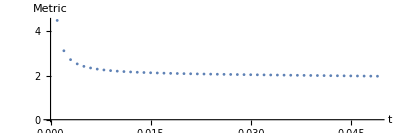

```mathematica
(*We now regard these variables as tangent space coordinates at a point in the Hitchin section.*)
x=({{x11, x12, x13, x14}, {x21, x22, x23, x24}});
y=({{y11, y12}, {y21, y22}, {y31, y32}, {y41, y42}});
A={λ1,λ2,λ3,λ4,({{h, e}, {f, -h}})};(*Arbitrary element of Lie algebra*)
(*Define the Lie algebra action*)
algActx[A_,x_]:=Table[A[[5]].x[[All,i]]-x[[All,i]]A[[i]],{i,1,4}]ᵀ
algActy[A_,y_]:=Table[A[[i]]y[[i,All]]-y[[i,All]].A[[5]],{i,1,4}]


(*Ensures orthogonality to the instantaneous group action*)
actionCondition=Table[Tr[algActx[A,xNumerical[[i]]].xᵀ]+Tr[algActy[A,yNumerical[[i]]].yᵀ]==0,{i,1,n}];
(*Do I need a conjugate transpose here?  I think not, because we're solving for a C-subspace, not an R-subspace*)


(*Restricts to the kernel of dμC*)
dμCx=Map[D[μC[x,y], #]&,x,{2}]/.Thread[Flatten[y]->Flatten[#]]&/@yNumerical;
dμCy=Map[D[μC[x,y], #]&,y,{2}]/.Thread[Flatten[x]->Flatten[#]]&/@xNumerical;
μCCondition=Table[Total[x dμCx[[i]],{1,2}]+Total[y dμCy[[i]],{1,2}]==0,{i,1,n}];


(*Restricts to the kernel of dμSL*)
dμSLx=Map[D[μSL[x,y], #]&,x,{2}]/.Thread[Flatten[y]->Flatten[#]]&/@yNumerical;
dμSLy=Map[D[μSL[x,y], #]&,y,{2}]/.Thread[Flatten[x]->Flatten[#]]&/@xNumerical;
μSL2Condition=Table[Total[x dμSLx[[i]],{1,2}]+Total[y dμSLy[[i]],{1,2}]==0,{i,1,n}];


(*It's computationally easier to handle this one dimension at a time.  Linearity makes this possible*)
vars=Join[Flatten[x],Flatten[y]];
justλ1={λ2->0,λ3->0,λ4->0,e->0,f->0,h->0};
justλ2={λ1->0,λ3->0,λ4->0,e->0,f->0,h->0};
justλ3={λ1->0,λ2->0,λ4->0,e->0,f->0,h->0};
justλ4={λ1->0,λ2->0,λ3->0,e->0,f->0,h->0};
juste={λ1->0,λ2->0,λ3->0,λ4->0,f->0,h->0};
justf={λ1->0,λ2->0,λ3->0,λ4->0,e->0,h->0};
justh={λ1->0,λ2->0,λ3->0,λ4->0,e->0,f->0};

TanSpaceRules=Table[Solve[{actionCondition[[i]]/.justλ1,
actionCondition[[i]]/.justλ2,
actionCondition[[i]]/.justλ3,
actionCondition[[i]]/.justλ4,
actionCondition[[i]]/.juste,
actionCondition[[i]]/.justf,
actionCondition[[i]]/.justh,
μSL2Condition[[i]],μCCondition[[i]]
},vars],{i,1,n}]//Quiet;

(*This is the HP tangent space given as a subspace of Rep(Q) parameterized by x11 and x13*)
xSpaces=Table[Chop[x/.TanSpaceRules[[i,1]]],{i,1,n}];
ySpaces=Table[Chop[y/.TanSpaceRules[[i,1]]],{i,1,n}];

xMetric=Tr[#.#ᵀ]&/@xSpaces;
yMetric=Tr[#.#ᵀ]&/@ySpaces;
metric=xMetric+yMetric;


(*As a sanity check, I approximate dx/dt and dy/dt at t0 to confirm it belongs to the tangent space--amazingly, it lands in the line x13=0!*)
t0=1;
dxdt=Table[(xNumerical[[i+1]]-xNumerical[[i]])/Δt,{i,1,n-1}];
dydt=Table[(yNumerical[[i+1]]-yNumerical[[i]])/Δt,{i,1,n-1}];

xSpaces[[t0]]//MatrixForm
ySpaces[[t0]]//MatrixForm
dxdt[[t0]]//MatrixForm
dydt[[t0]]//MatrixForm

xSpaces[[t0]]/.{x11->dxdt[[t0,1,1]],x13->0}//MatrixForm
ySpaces[[t0]]/.{x11->dxdt[[t0,1,1]],x13->0}//MatrixForm

(*We saw that x11 points in the (∂x/∂t, ∂y/∂t) direction, but it won't be the right length in general.  The variable rescaledMetric fixes this.*)
rescaledMetric=Table[metric[[i]]/.{x11->dxdt[[i,1,1]],x13->0},{i,1,n-1}];
metricPlot=ListPlot[
{(*{tvals,metric/.{x11->1,x13->0}}ᵀ,{tvals,metric/.{x11->0,x13->1}}ᵀ,*){Drop[tvals,-1],rescaledMetric}ᵀ},
PlotStyle->PointSize[0.005],
AxesLabel->{"t","Metric"},
PlotLegends->{"(x_11)^2-coefficient","(x_13)^2-coefficient","Rescaled (x_11)^2-coefficient"},
PlotRange->Full,
AspectRatio->1/3
]
```

### Parameterization by Height

```mathematica
x=({{x11, x12, 0, 0}, {0, 0, x23, x24}});
y=({{0, y12}, {0, y22}, {y31, 0}, {y41, 0}});
vars=DeleteCases[Flatten[{x,y}],0];
Ivars={x11,x12,y12,y22};
Icvars={x23,x24,y31,y41};
Realify=Refine[#,#∈Reals&/@vars]&;

(*This represents the height of the hyperpolygon, which should be exactly half of ΦU1*)
ΦmaxI=2(βTest[[3]]+βTest[[4]]);
height[t_]=ΦmaxI+2Abs[t];
sols=Solve[{μU1[x,y][[1;;2]]==βTest[[1;;2]],μSL[x,y]==0,Norm[{x11,y12,x12,y22}]^2==height[t]}/.Thread[Icvars->0],{x11,x12,y12,y22},Reals][[1]];
sols=Solve[{μU1[x,y][[3;;4]]==βTest[[3;;4]],μSL[x,y]==0,Norm[{x23,y31,x24,y41}]^2==height[t]}/.Thread[Ivars->0],{x23,x24,y31,y41},Reals][[1]];
sols=Solve[{μU1[x,y]==βTest,μSU2[x,y]==0,μSL[x,y]==0,Norm[{x23,y31,x24,y41}]^2==height[t]},vars,Reals]//Last;

Δt=0.1; n=50;
tList=Table[i Δt,{i,1,n}];
xList=Table[x/.sols/.t->i Δt,{i,1,n}];
yList=Table[y/.sols/.t->i Δt,{i,1,n}];

x=({{x11, x12, x13, x14}, {x21, x22, x23, x24}});y=({{y11, y12}, {y21, y22}, {y31, y32}, {y41, y42}});

GraphicsRow[{ListPlot[{tList,#}ᵀ&/@((Flatten/@xList)ᵀ),PlotLabels->Flatten[x]],ListPlot[{tList,#}ᵀ&/@((Flatten/@yList)ᵀ),PlotLabels->Flatten[y]]}]

ΦExtra=2Table[Sum[yList[[i,j,1]]^2,{j,3,4}],{i,1,n}];(*This turns out to be exactly t*)
resTerms=2Table[Sum[xList[[i,2,j]]^2 yList[[i,j,1]]^2/(2βTest[[j]]),{j,3,4}],{i,1,n}];
ListPlot[{tList,#}ᵀ&/@{ΦmaxI+ΦExtra,ΦmaxI+resTerms},PlotLabels->{Φ,"residue norms"}]
```

-Graphics-

-Graphics-

## Section 5 - Taylor Series about

### First Order Behavior at

```mathematica
x=({{x11, x12, x13, x14}, {x21, x22, x23, x24}});
y=({{y11, y12}, {y21, y22}, {y31, y32}, {y41, y42}});
x0=Simplify[({{x11, x12, 0, 0}, {0, 0, x23, x24}})/.fixedPt1,chamberAssumptions];
y0=Simplify[({{0, y12}, {0, y22}, {0, 0}, {0, 0}})/.fixedPt1,chamberAssumptions];
A={λ1,λ2,λ3,λ4,({{h, e}, {f, -h}})};(*Arbitrary element of Lie algebra*)
(*Define the Lie algebra action*)
algActx[A_,x_]:=Table[A[[5]].x[[All,i]]-x[[All,i]]A[[i]],{i,1,4}]ᵀ
algActy[A_,y_]:=Table[A[[i]]y[[i,All]]-y[[i,All]].A[[5]],{i,1,4}]

actionSpan=Tr[algActx[A,x0].xᵀ]+Tr[algActy[A,y0].yᵀ];

dμCx=Map[D[μC[x,y], #]&,x,{2}]/.Thread[Flatten[y]->Flatten[y0]] ;
dμCy=Map[D[μC[x,y], #]&,y,{2}]/.Thread[Flatten[x]->Flatten[x0]];
kerdμC=Total[x dμCx,{1,2}]+Total[y dμCy,{1,2}];

dμSLx=Map[D[μSL[x,y], #]&,x,{2}]/.Thread[Flatten[y]->Flatten[y0]];
dμSLy=Map[D[μSL[x,y], #]&,y,{2}]/.Thread[Flatten[x]->Flatten[x0]];
kerdμSL2=Total[x dμSLx,{1,2}]+Total[y dμSLy,{1,2}];

sl2Basis={λ1,λ2,λ3,λ4,e,f,h};
fullRules=Thread[sl2Basis->0];
ruleSets=Table[Drop[fullRules,{i}],{i,1,7}];

vars=Join[Flatten[x],Flatten[y]];
firstOrderRules=Solve[{(actionSpan/.ruleSets)==0,kerdμC==0,kerdμSL2==0},vars]//Simplify//Quiet;
x/.firstOrderRules[[1]]//MatrixForm
y/.firstOrderRules[[1]]//MatrixForm
u=%%/.x13->0;
v=%%/.y31->-1;
(*Turns out, x23/.fixedPt1[[1]] and x24/.fixedPt1[[1]] are both 1, so this is consistent with our parameterization in complex gauge in Section 3*)
```

(0 | 0 | x13 | -(x13 √β3)/(√β4)
0 | 0 | 0 | 0)

(0 | 0
0 | 0
y31 | 0
-(y31 √β3)/(√β4) | 0)

### Order K Behavior at

$Aborted

((-2 β4 (β1-β2+β3+β4) (β1+β2+β3+β4)+t^2 (β1^2-β2^2-(β3+β4)^2))/(2 √2 β4 √((β3+β4) (β1-β2+β3+β4) (β1+β2+β3+β4))) | -(t^2 (β1^2-β2^2+(β3+β4)^2)+2 β4 (-β1^2+(β2+β3+β4)^2))/(2 √2 β4 √((β3+β4) (-β1+β2+β3+β4) (β1+β2+β3+β4))) | 0 | 0
0 | 0 | -(t^2+4 β3)/(2 √2 √β3) | -(t^2 β3+4 β4^2)/(2 √2 β4^(3/2)))

(0 | (2 β2^2 β4-2 β4 (-β1+β3+β4)^2+t^2 (β1^2-β2^2-(β3+β4)^2))/(2 √2 β4 √((β3+β4) (-β1-β2+β3+β4) (-β1+β2+β3+β4)))
0 | (t^2 (β1^2-β2^2+(β3+β4)^2)+2 β4 (-β1^2+(-β2+β3+β4)^2))/(2 √2 β4 √((β3+β4) (-β1-β2+β3+β4) (β1-β2+β3+β4)))
-t | 0
t √(β3/β4) | 0)

((β3+β4) (2 β3 β4^2 (-β1-β2+β3+β4) (β1-β2+β3+β4) (-β1+β2+β3+β4) (β1+β2+β3+β4)+t^2 (β1^4 (β3^2-5 β3 β4+β4^2)-2 β1^2 (β3^4+β3^3 β4+β3 β4^3+β4^4+β2^2 (β3^2-5 β3 β4+β4^2))+(β2-β3-β4) (β2+β3+β4) (β2^2 (β3^2-5 β3 β4+β4^2)-(β3+β4)^2 (β3^2+3 β3 β4+β4^2)))))/(2 β3 β4^3 (-β1-β2+β3+β4) (β1-β2+β3+β4) (-β1+β2+β3+β4) (β1+β2+β3+β4))

2+(192666 t^2)/13585

-Graphics-

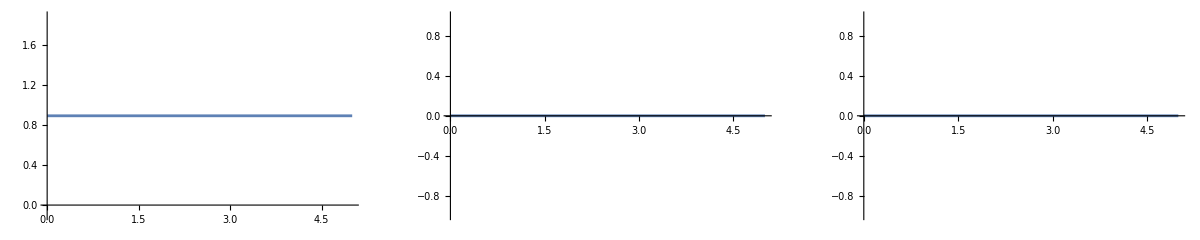

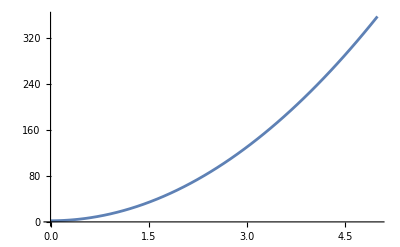

```mathematica
(*Define Variables*)
K=3;
XSymbols=Table[Subscript[X, i,j,k],{i,0,K},{j,1,2},{k,1,4}];
YSymbols=Table[Subscript[Y, i,j,k],{i,0,K},{j,1,4},{k,1,2}];
vars=Flatten[{XSymbols,YSymbols,t}];
zeroHOT=Thread[Flatten[{XSymbols,YSymbols}]->0];
Realify=Refine[#,#∈Reals&/@vars]&;
xSeries[t_]=FromDigits[Reverse[XSymbols],t];
ySeries[t_]=FromDigits[Reverse[YSymbols],t];
ϕSeries[t_]=∑_(i=1)^4 ({xSeries[t][[All,i]]}ᵀ.{ySeries[t][[i,All]]})/(z-p[[i]]);
xPlotsTaylor={};yPlotsTaylor={};

(*The first line is for plugging in values we already know, second line comes from which entries of x will be identically 0.*)
taylorRules=Thread[Flatten[{XSymbols[[{1,2},All,All]],YSymbols[[{1,2},All,All]]}]->Flatten[{x0,u,y0,v}]];
taylorRules=Join[taylorRules,Thread[XSymbols[[All,1,3]]->0],Thread[XSymbols[[All,1,4]]->0],Thread[XSymbols[[All,2,1]]->0],Thread[XSymbols[[All,2,2]]->0],Thread[YSymbols[[All,1,1]]->0],Thread[YSymbols[[All,2,1]]->0],Thread[YSymbols[[All,3,2]]->0],Thread[YSymbols[[All,4,2]]->0]];

For[i=2,i<=K,i++,
(*Calculate derivative in t and solve for t^i coefficients.  The last condition is to make the parameterization the right "speed".*)
ithOrderRules=Solve[({
D[Realify[μU1[xSeries[t],ySeries[t]]],{t,i}],
D[Realify[μC[xSeries[t],ySeries[t]]],{t,i}],
D[Realify[μSU2[xSeries[t],ySeries[t]]],{t,i}],
D[Realify[μSL[xSeries[t],ySeries[t]]],{t,i}],
D[Det[ϕSeries[t]],{t,i}]}/.t->0/.taylorRules)==0,vars][[1]]//Quiet;
taylorRules=Join[taylorRules,ithOrderRules];
xTaylor[t_]=Simplify[xSeries[t]/.taylorRules/.zeroHOT,chamberAssumptions];
yTaylor[t_]=Simplify[ySeries[t]/.taylorRules/.zeroHOT,chamberAssumptions];
ϕTaylor[t_]=∑_(i=1)^4 ({xTaylor[t][[All,i]]}ᵀ.{yTaylor[t][[i,All]]})/(z-p[[i]]);
AppendTo[xPlotsTaylor,Plot[Evaluate@Flatten[xTaylor[t]/.Thread[β->βTest]],{t,0,n Δt}]];
AppendTo[yPlotsTaylor,Plot[Evaluate@Flatten[yTaylor[t]/.Thread[β->βTest]],{t,0,n Δt}]];

]

FullSimplify[xTaylor[t],chamberAssumptions]//MatrixForm
FullSimplify[yTaylor[t],chamberAssumptions]//MatrixForm
metricTaylor=FullSimplify[Tr[D[xTaylor[t]ᵀ, t].D[xTaylor[t], t]]+Tr[D[yTaylor[t]ᵀ, t].D[yTaylor[t], t]],chamberAssumptions]
metricTaylorNumerical=metricTaylor/.Thread[β->{1/4,1/3,1/2,1/2}]//FullSimplify

GraphicsGrid[{Show[xPlotNumerical,#]&/@xPlotsTaylor,Show[yPlotNumerical,#]&/@yPlotsTaylor}]

(*Derivatives of the (4,1)-entry of yTaylor*)
GraphicsRow[
Table[
Show[ListPlot[{Drop[tvals,-i],Differences[yNumerical[[All,4,1]]/Δt^i,i]}ᵀ],Plot[D[yTaylor[t][[4,1]]/.Thread[β->βTest],{t,i}]/.t->s,{s,0,n Δt}],PlotRange->All],{i,1,K}]]

Plot[metricTaylorNumerical,{t,0,n Δt}]

(*We may need to be careful here, because the metric will only behave this way if the tangent spaces we've found are orthogonal to the unitary action.  That's probably true because of the realness assumption, but I should double check that.*)
```

## Section 6 - Higgs Bundles

```mathematica
vars={a,b,t,p0};
Dz=1/2(D[#, a]-ⅈ D[#, b])&; Dzbar=1/2(D[#, a]+ⅈ D[#, b])&;
Realify=FullSimplify[#,Thread[vars∈Reals]]&;
ϕ=ϕTaylor[t]/.Thread[β->βTest];
ϕ0=ϕ/.{t->0,z->(a+ⅈ b)};
ϕ1=D[ϕ, t]/.t->0;
ϕ0//MatrixForm
ϕ1//MatrixForm

betterAbs=√(# #*)&;
h={{betterAbs[a+ⅈ b -p[[1]]]^2 betterAbs[a+ⅈ b -p[[2]]]^2 λ[a,b],0},{0,λ[a,b]^-1}};
ϕ0adj=Realify[Inverse[h].ϕ0†.h];
ϕ0adj//MatrixForm
ϕ0.ϕ0adj-ϕ0adj.ϕ0//Realify//MatrixForm

logh=Realify[{{Log[h[[1,1]]],0},{0,Log[h[[2,2]]]}}]
Realify@Dzbar@Dz[logh]
```

(0 | -(√13585)/(288 (1+a+ⅈ b))+(√13585)/(288 (a+ⅈ b-p0))
0 | 0)

(0 | 0
-1/(-1+z)+1/z | 0)

(0 | 0
1/288 √13585 (1+a+ⅈ b) (a+ⅈ b-p0) (1+p0) λ[a,b]^2 | 0)

((13585 (1+p0)^2 λ[a,b]^2)/82944 | 0
0 | -(13585 (1+p0)^2 λ[a,b]^2)/82944)

{{Log[((1+a)^2+b^2) (b^2+(a-p0)^2) λ[a,b]],0},{0,Log[1/λ[a,b]]}}

{{-((λ^(0,1)[a,b])^2+(λ^(1,0)[a,b])^2-λ[a,b] (λ^(0,2)[a,b]+λ^(2,0)[a,b]))/(4 λ[a,b]^2),0},{0,((λ^(0,1)[a,b])^2+(λ^(1,0)[a,b])^2-λ[a,b] (λ^(0,2)[a,b]+λ^(2,0)[a,b]))/(4 λ[a,b]^2)}}

## Section 7 - Metric on Polygon Space

### At basepoint of exterior sphere

```mathematica
x=({{x11, x12, x13, x14}, {0, 0, x23, x24}});y=({{0, 0}, {0, 0}, {0, 0}, {0, 0}});
vars={x11,x12,x13,x14,x23,x24};
Realify=FullSimplify[#,Thread[vars∈Reals]]&;
A={λ1,λ2,λ3,λ4,({{h, e}, {f, -h}})};(*Arbitrary element of Lie algebra*)
(*Define the Lie algebra action*)
algActx[A_,x_]:=Table[A[[5]].x[[All,i]]-x[[All,i]]A[[i]],{i,1,4}]ᵀ
algActy[A_,y_]:=Table[A[[i]]y[[i,All]]-y[[i,All]].A[[5]],{i,1,4}]

basePoint=Solve[Realify[{μU1[x,y],μSU2[x,y]}]=={β,0},vars]//Last;
x0=x/.basePoint;
y0=y/.basePoint;
x=({{x11, x12, x13, x14}, {x21, x22, x23, x24}});y=({{y11, y12}, {y21, y22}, {y31, y32}, {y41, y42}});
vars=Flatten[{x,y}];
Realify=FullSimplify[#,Thread[vars∈Reals]]&;

dμC=Total[Flatten[{x,y}](D[Realify[μC[x,y]],#]&/@vars/.Thread[vars->Flatten[{x0,y0}]])];
dμSL2=Total[Flatten[{x,y}](D[Realify[μSL[x,y]],#]&/@vars/.Thread[vars->Flatten[{x0,y0}]])];
actionSpan=Total[x algActx[A,x0],{1,2}]+Total[y algActy[A,y0],{1,2}];
oneByOneRules=Table[Drop[Thread[{λ1,λ2,λ3,λ4,e,f,h}->0],{i}],{i,1,7}];
firstOrderRules=Solve[{dμC,dμSL2,actionSpan/.oneByOneRules}==0,vars][[1]]//Quiet;
x1=x/.firstOrderRules;
y1=y/.firstOrderRules;
x1//MatrixForm
y1//MatrixForm
(*Up to possible rescaling, this should exponentiate to action-angle coordinates*)
```

(0 | 0 | 0 | 0
x21 | -(x21 √β1)/(√β2) | 0 | 0)

(0 | y12
0 | -(y12 √β1)/(√β2)
0 | 0
0 | 0)

## Section 8 - Tangent Space at Hitchin Section in Complex Gauge (Ignore)

This probably needs to be revised because we can’t properly differentiate moment maps with conjugates unless we do so with respect to real variables, which means each matrix entry should by of the form x11 + ⅈ ix11 or something.  More importantly, this won’t be accurate unless the differentiation occurs after putting it in unitary gauge.

```mathematica
(*Disable:
actx[A_,x_]:=Table[A[[5]].x[[All,i]]-x[[All,i]]A[[i]],{i,1,4}]ᵀ
acty[A_,y_]:=Table[A[[i]]y[[i,All]]-y[[i,All]].A[[5]],{i,1,4}](*Define the Lie algebra action*)
x=({{x11, x12, x13, x14}, {x21, x22, x23, x24}});
y=({{y11, y12}, {y21, y22}, {y31, y32}, {y41, y42}});
hitchinRules={x13->0,x14->0,x21->0,x22->0,y11->0,y21->0,y32->0,y42->0,y31->x24 t,y41->-x23 t};(*(x,y) belongs to Hitchin section--see end of Section 2*)
x0=x/.hitchinRules;
y0=y/.hitchinRules;



A={λ1,λ2,λ3,λ4,({{h, e}, {f, -h}})};(*Arbitrary element of Lie algebra*)
groupSpanx=actx[A,x0];
groupSpany=acty[A,y0];(*Subspace generated by instantaneous action*)
xSpace=({{q11, q12, q13, q14}, {q21, q22, q23, q24}});
ySpace=({{p11, p12}, {p21, p22}, {p31, p32}, {p41, p42}});(*Tangent space variables*)
actionCondition=Tr[groupSpanx.xSpaceᵀ]+Tr[groupSpany.ySpaceᵀ]==0;(*Tangent space should be orthogonal (wrt natural hermitian metric) to the instantaneous action*)



dμSLx=Table[∂_x[[i,j]] μSL[x,y],{i,1,2},{j,1,4}]/.hitchinRules;(*Exterior derivative of μSL; (ij)th entry denotes dxij coefficient*)
dμSLy=Table[∂_y[[i,j]] μSL[x,y],{i,1,4},{j,1,2}]/.hitchinRules;(*(ij)th entry denotes dyij coefficient*)
μSLCondition=Total[xSpace dμSLx,{1,2}]+Total[ySpace dμSLy,{1,2}]==0;(*Tangent space should be in the kernel of dμSL*)



dμCx=Table[∂_x[[i,j]] μC[x,y],{i,1,2},{j,1,4}]/.hitchinRules;(*Exterior derivative of μC; indexing as before*)
dμCy=Table[∂_y[[i,j]] μC[x,y],{i,1,4},{j,1,2}]/.hitchinRules;
μCCondition=Total[xSpace dμCx,{1,2}]+Total[ySpace dμCy,{1,2}]==0;(*Tangent space should be in the kernel of dμC*)



justλ1={λ2->0,λ3->0,λ4->0,e->0,f->0,h->0};(*Want to focus on 1-dim subspace of Lie algebra at a time*)
justλ2={λ1->0,λ3->0,λ4->0,e->0,f->0,h->0};
justλ3={λ1->0,λ2->0,λ4->0,e->0,f->0,h->0};
justλ4={λ1->0,λ2->0,λ3->0,e->0,f->0,h->0};
juste={λ1->0,λ2->0,λ3->0,λ4->0,f->0,h->0};
justf={λ1->0,λ2->0,λ3->0,λ4->0,e->0,h->0};
justh={λ1->0,λ2->0,λ3->0,λ4->0,e->0,f->0};

vars={q11,q12,q13,q14,q21,q22,q23,q24,p11,p12,p21,p22,p31,p32,p41,p42};
tanSpaceRules=Solve[{actionCondition/.justλ1,
actionCondition/.justλ2,
actionCondition/.justλ3,
actionCondition/.justλ4,
actionCondition/.juste,
actionCondition/.justf,
actionCondition/.justh,(*it's computationally easier to handle this one dimension at a time--linearity makes this possible*)
μSLCondition,μCCondition
},vars]//FullSimplify;

xSpace/.tanSpaceRules[[1]];
ySpace/.tanSpaceRules[[1]];
(*Things change drastically when t=0.  Is that because it's a singular point?  The tangent space dimension doesn't increase though.*)

xTan=FullSimplify[%%/.fixedPt1[[1]]];
yTan=FullSimplify[%%/.fixedPt1[[1]]];(*Resulting tangent spaces at the explicit coordinates of the Hitchin section--depends on parabolic weights*)

(*Next we compute the induced real symplectic form on the complex 2D tangent space*)
ωR[w1_,w2_]=Re[w1].Im[w2]-Im[w1].Re[w2];(*Since the tangent space is a complex subspace of the original affine space, the formula is the same*)
u=Join[Flatten[xTan],Flatten[yTan]]/.{q11->u1+ⅈ v1,q13->u2+ⅈ v2};(*see below for general t*)
z=Join[Flatten[xTan],Flatten[yTan]]/.{q11->z1+ⅈ w1,q13->z2+ⅈ w2};
(*u and z are 2 different elements of the tangent space, flattened into 16-dim complex vectors*)
Refine[ωR[u,z],Assumptions->{u1∈Reals,u2∈Reals,v1∈Reals,v2∈Reals,z1∈Reals,z2∈Reals,w1∈Reals,w2∈Reals,t∈Reals,t!=0}]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

(2 (105+1093 t^2) (168 u1 w1-168 v1 z1+361 t^2 (u2 w2-v2 z2)))/(37905 t^2)

The above is the explicit description of the real symplectic form for the parabolic parameters β = {1,1,2,3} and for real nonzero values of t.  Below is the actual tangent space parameterized by q11 and q13, and then the symplectic form for t=1 just to show how clean the answers are for numerical parameters.

```mathematica
(*Disable
xTan//MatrixForm
yTan//MatrixForm
u=Join[Flatten[xTan],Flatten[yTan]]/.{q11->u1+ⅈ v1,q13->u2+ⅈ v2};
z=Join[Flatten[xTan],Flatten[yTan]]/.{q11->z1+ⅈ w1,q13->z2+ⅈ w2};
FullSimplify[ωR[u,z]/.t->1,Assumptions->{u1∈Reals,u2∈Reals,v1∈Reals,v2∈Reals,z1∈Reals,z2∈Reals,w1∈Reals,w2∈Reals}]
```

(q11 | q11 | q13 | -(√6 q13 (2+3 t^2))/(6+4 t^2)
(5 q13 t (1+t^2))/(3+2 t^2) | -(5 q13 t (1+t^2))/(3+2 t^2) | (√(7/2) q11 (3+2 t^2))/(5 (1+t^2)) | (√(7/3) q11 (2+3 t^2))/(5 (1+t^2)))

(-(5 √(3/7) q13 t (1+t^2))/(3+2 t^2) | √(7/3) q11
-(5 √(3/7) q13 t (1+t^2))/(3+2 t^2) | -√(7/3) q11
(√(7/3) q11 (3+2 t^2))/(5 (t+t^3)) | -√(3/2) q13 t
-(√(7/2) q11 (2+3 t^2))/(5 (t+t^3)) | -(q13 t (2+3 t^2))/(3+2 t^2))

115/84 (7 u1 w1+12 u2 w2-7 v1 z1-12 v2 z2)

```mathematica
(*Disable
Solve[{actionCondition/.justλ1,
actionCondition/.justλ2,
actionCondition/.justλ3,
actionCondition/.justλ4,
actionCondition/.juste,
actionCondition/.justf,
actionCondition/.justh,(*it's computationally easier to handle this one dimension at a time--linearity makes this possible*)
μSLCondition,μCCondition
}/.t->0,vars]//FullSimplify
xTan/.%[[1]]//MatrixForm
yTan/.%%[[1]]//MatrixForm
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{q11→0,q12→0,q14→-(q13 x23)/x24,q21→0,q22→0,q23→0,q24→0,p11→0,p12→0,p21→0,p22→0,p32→0,p41→-(p31 x23)/x24,p42→0}}

(0 | 0 | q13 | -(√6 q13 (2+3 t^2))/(6+4 t^2)
(5 q13 t (1+t^2))/(3+2 t^2) | -(5 q13 t (1+t^2))/(3+2 t^2) | 0 | 0)

(-(5 √(3/7) q13 t (1+t^2))/(3+2 t^2) | 0
-(5 √(3/7) q13 t (1+t^2))/(3+2 t^2) | 0
0 | -√(3/2) q13 t
0 | -(q13 t (2+3 t^2))/(3+2 t^2))

```mathematica
(*Disable
f[r](ⅆ x^2+ⅆ y^2)
```

(ⅆ{{x11^2,x12^2,x13^2,x14^2},{x21^2,x22^2,x23^2,x24^2}}+ⅆ{{y11^2,y12^2},{y21^2,y22^2},{y31^2,y32^2},{y41^2,y42^2}}) f[r]

```mathematica
sols[[1]]/.s->1
```

{μ1→1/65 ((72 Root-2.19Root[13585-40755 #1^2-96333 #1^4-84770 #1^6-96333 #1^8-40755 #1^10+13585 #1^12&,1]-2.193621909265707)/(-1+(Root-2.19Root[13585-40755 #1^2-96333 #1^4-84770 #1^6-96333 #1^8-40755 #1^10+13585 #1^12&,1]-2.193621909265707)^2)-√(13585+(5184 (Root-2.19Root[13585-40755 #1^2-96333 #1^4-84770 #1^6-96333 #1^8-40755 #1^10+13585 #1^12&,1]-2.193621909265707)^2)/((-1+(Root-2.19Root[13585-40755 #1^2-96333 #1^4-84770 #1^6-96333 #1^8-40755 #1^10+13585 #1^12&,1]-2.193621909265707)^2)^2))),μ2→1/55 ((96 Root-2.19Root[13585-40755 #1^2-96333 #1^4-84770 #1^6-96333 #1^8-40755 #1^10+13585 #1^12&,1]-2.193621909265707)/(-1+(Root-2.19Root[13585-40755 #1^2-96333 #1^4-84770 #1^6-96333 #1^8-40755 #1^10+13585 #1^12&,1]-2.193621909265707)^2)-√(13585+(9216 (Root-2.19Root[13585-40755 #1^2-96333 #1^4-84770 #1^6-96333 #1^8-40755 #1^10+13585 #1^12&,1]-2.193621909265707)^2)/((-1+(Root-2.19Root[13585-40755 #1^2-96333 #1^4-84770 #1^6-96333 #1^8-40755 #1^10+13585 #1^12&,1]-2.193621909265707)^2)^2))),μ3→Root-2.19Root[13585-40755 #1^2-96333 #1^4-84770 #1^6-96333 #1^8-40755 #1^10+13585 #1^12&,1]-2.193621909265707,μ4→Root-2.19Root[13585-40755 #1^2-96333 #1^4-84770 #1^6-96333 #1^8-40755 #1^10+13585 #1^12&,1]-2.193621909265707}

## Section 9 - Numerical Flow to Central Sphere

### 2D Version

```mathematica
β={β1,β2,β3,β4};
βTest={1/9,1/6,1/5,1/4};
x=({{1, 1, 0, -1}, {0, 1, 1, 1}});
y=({{y11, y12}, {y21, y22}, {y31, y32}, {y41, y42}});
traceFree[A_]:=A-Tr[A]/2 IdentityMatrix[2];
groupActx[g_,x_]:=g[[1]].x .Inverse[g[[2]]];
groupActy[g_,y_]:=g[[2]].y.Inverse[g[[1]]];
(*g should be a list {A,λ} where λ is a diagonal matrix*)
A=({{a11, a12}, {a21, a22}});λ=DiagonalMatrix[{1,λ2,λ3,λ4}];
g={A,λ};

vars=DeleteCases[Flatten[{g}],_Integer];
Realify=FullSimplify[#,Thread[vars∈Reals]]&;

y0=ConstantArray[0,{4,2}];
Solve[{Realify@μU1[groupActx[g,x],y0]==βTest,Realify@μSU2[groupActx[g,x],y0]==0},vars]//Last//Quiet;
g0=g/.%;
x=groupActx[g0,x]//N
```

{{0.471405,0.48142,0.157669,-0.49893},{0.,0.318698,0.612487,0.501068}}

(0.471405 | 0.48142 | 0.157669 | -0.49893
0. | 0.318698 | 0.612487 | 0.501068)

(0 | t
0.470948 t | -0.711405 t
-0.4901 t | 0.126164 t
0.299541 t | 0.298263 t)

(2.12132 | 1.86624 | 0.788448 | 2.94839
-2.76552 | -0.535162 | 0.215191 | 3.29243)

(0. | 1.
0.470948 | -0.711405
-0.4901 | 0.126164
0.299541 | 0.298263)

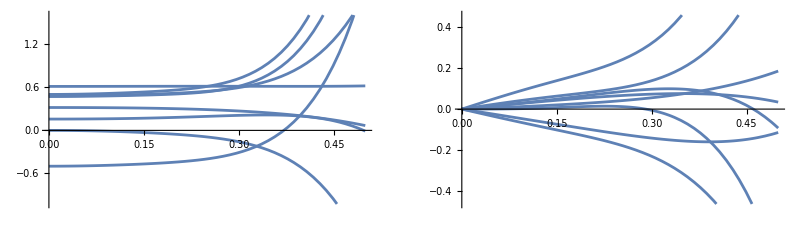

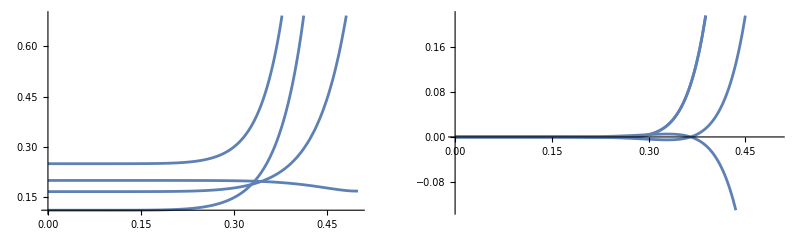

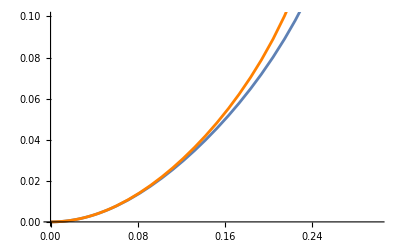

```mathematica
y=({{0, t}, {y21, y22}, {y31, y32}, {y41, y42}});
Solve[{μC[x,y]==0,μSL[x,y]==0},DeleteCases[DeleteCases[Flatten[y],t],0]][[1]]//Chop;
y=y/.%;
x//MatrixForm
y//MatrixForm

vars={a11,a12,a21,a22,t,λ1,λ2,λ3,λ4};
Realify=Refine[#,Thread[vars∈Reals]]&;

g={({{1, 0}, {0, 1}}),IdentityMatrix[4]};
n=6;
Do[
g=g+{t^i({{a11, a12}, {a21, -a11}}),t^i DiagonalMatrix[{λ1,λ2,λ3,λ4}]};
dμU1=D[Realify@μU1[groupActx[g,x],groupActy[g,y]],{t,i}]/.t->0//Simplify;
dμSU2=D[Realify@μSU2[groupActx[g,x],groupActy[g,y]],{t,i}]/.t->0//Simplify;
sol=Solve[{dμU1==0,dμSU2==0},{a11,a12,a21,a22,λ1,λ2,λ3,λ4}][[1]]//Quiet;
g=g/.sol/.Thread[{a11,a12,a21,a22,λ1,λ2,λ3,λ4}->1],
{i,2,n}(*Starts at 2 because first order part is automatically 0*)
]

g=g/.Thread[{a11,a12,a21,a22,λ1,λ2,λ3,λ4}->1];

(*g=g+{t^7({{a11, a12}, {a21, -a11}}),t^7 DiagonalMatrix[{λ1,λ2,λ3,λ4}]};
dμU1=D[Realify@μU1[groupActx[g,x],groupActy[g,y]],{t,7}]/.t->0//Simplify;
dμSU2=D[Realify@μSU2[groupActx[g,x],groupActy[g,y]],{t,7}]/.t->0//Simplify;
sol=Solve[{dμU1==0,dμSU2==0},{a11,a12,a21,a22,λ1,λ2,λ3,λ4}][[1]]//Quiet*)


xt=groupActx[g,x]+O[t]^(n+1)//Normal;
yt=groupActy[g,y]+O[t]^(n+1)//Normal;

D[xt, t,t]/.t->0//MatrixForm
D[yt, t]/.t->0//MatrixForm

xPlot=Plot[Flatten[xt],{t,0,.5}];
yPlot=Plot[Flatten[yt],{t,0,.5}];
GraphicsRow[{xPlot,yPlot}]

μU1Plot=Plot[μU1[xt,yt],{t,0,.5}];
μSU2Plot=Plot[μSU2[xt,yt],{t,0,.5}];
GraphicsRow[{μU1Plot,μSU2Plot}]

(*Residue norm vs U(1)-moment map*)
ΦU1[yin_]:=1/2 Tr[yinᵀ.yin];
ΦU1Plot=Plot[2ΦU1[yt],{t,0,.5}];

ϕList=Table[xt[[All,i;;i]].yt[[i;;i,All]],{i,1,4}]//Chop;
calcResultPlot=Plot[Sum[Tr[ϕList[[i]]ᵀ.ϕList[[i]]]/(2βTest[[i]]),{i,1,4}],{t,0,.5},PlotStyle->Orange];
Show[{ΦU1Plot,calcResultPlot},PlotRange->{{0,.3},{0,0.1}}]
```

```mathematica
v=Simplify@Table[traceFree[xt[[All,i;;i]].xt[[All,i;;i]]ᵀ],{i,1,4}];
w=Simplify@Table[traceFree[yt[[i;;i,All]]ᵀ.yt[[i;;i,All]]],{i,1,4}];
F[B_]:={Tr[({{ⅈ, 0}, {0, -ⅈ}}).(ⅈ B)](*,Tr[({{0, 1}, {-1, 0}}).(ⅈ B)]*),Tr[({{0, ⅈ}, {ⅈ, 0}}).(ⅈ B)]};

vertices={{0,0(*,0*)}};
Do[AppendTo[vertices,Last[vertices]+F[v[[i]]]];
AppendTo[vertices,Last[vertices]-F[w[[i]]]],
{i,1,4}]

hyperpolygon={};
Do[AppendTo[hyperpolygon,Red];
AppendTo[hyperpolygon,Line[{vertices[[i]],vertices[[i+1]]}]];
AppendTo[hyperpolygon,Blue];
AppendTo[hyperpolygon,Line[{vertices[[i+1]],vertices[[i+2]]}]],
{i,1,7,2}];
Manipulate[Graphics[{Thickness[.008],Chop[hyperpolygon/.t->t0]},Background->White,PlotRange->{{-.7,.2},{-.7,.2}}],{t0,0,.3}]
```

### 3D Version

#### Finding the Polygon

```mathematica
β={β1,β2,β3,β4};
βTest={1/9,1/6,1/5,1/4};
traceFree[A_]:=A-Tr[A]/2 IdentityMatrix[2];
groupActx[g_,x_]:=g[[1]].x .Inverse[g[[2]]];
groupActy[g_,y_]:=g[[2]].y.Inverse[g[[1]]];
(*g should be a list {A,λ} where λ is a diagonal matrix*)

(*x=({{√(2βTest[[1]]), 1, 0, -1}, {0, ⅈ, 1, 1}});*)x=({{√(2βTest[[1]]), 0, 1, 1}, {0, 1, 1, c+ⅈ d}});y0=ConstantArray[0,{4,2}];
A=({{1, a12+ⅈ b12}, {0, a22}});λ=DiagonalMatrix[{1,λ2,λ3,λ4}];
g={A,λ};

vars={a12,b12,a22,λ2,λ3,λ4};
Realify=Simplify[#,TransformationFunctions->ComplexExpand]&;

Clear[c0,d0];
x=({{√(2βTest[[1]]), 0, 1, 1}, {0, 1, 1, c+ⅈ d}});
(*Manipulate[*)
parameterRules=(*{c->c0,d->d0}*){c->0,d->1};
momentMapEqns=
FullSimplify@Realify@Re@μU1[groupActx[g,x]/.parameterRules,y0]==βTest&&(*Imaginary part is already 0*)
FullSimplify@Realify@Re@μSU2[groupActx[g,x]/.parameterRules,y0]==0&&
FullSimplify@Realify@Im@μSU2[groupActx[g,x]/.parameterRules,y0]==0;

sol=NSolve[momentMapEqns/.parameterRules,vars,Reals][[1]]//Quiet;
x0=groupActx[g,x]/.parameterRules/.sol;

v=Simplify@Table[traceFree[x0[[All,i;;i]].x0[[All,i;;i]]†],{i,1,4}];
F[B_]:={Tr[({{ⅈ, 0}, {0, -ⅈ}}).(ⅈ B)],Tr[({{0, 1}, {-1, 0}}).(ⅈ B)],Tr[({{0, ⅈ}, {ⅈ, 0}}).(ⅈ B)]};
vertices={{0,0,0}};
Do[AppendTo[vertices,Last[vertices]+F[v[[i]]]],{i,1,4}];
polygon=Line[vertices];
Graphics3D[{Thickness[.008],Line[vertices]},Background->White](*,
{c0,0,2},{d0,1,2}]*)


y=({{0, t}, {y21, y22}, {y31, y32}, {y41, y42}});
Solve[μC[x0,y]==0&&μSL[x0,y]==0,DeleteElements[Flatten[y],{t,0}]][[1]];
yt=y/.%//Chop;
yt//MatrixForm
```

-Graphics3D-

(0 | t
(0.+0.596174 ⅈ) t | (-0.314679-0.190829 ⅈ) t
(0.341754-0.341754 ⅈ) t | (0.504564-0.143788 ⅈ) t
(0.266134-0.266134 ⅈ) t | (-0.282346-0.111973 ⅈ) t)

#### Visualizing Three Parameters

```mathematica
A=({{1, a12+ⅈ b12}, {0, a22}});λ=DiagonalMatrix[{λ1,λ2,λ3,λ4}];
g={A,λ};
Manipulate[
g={A,λ};
sol=NSolve[(FullSimplify@Chop@Realify@μU1[groupActx[g,x],groupActy[g,y]]==βTest)/.{t->t0,a12->s2,b12->s3,a22->s4},{λ1,λ2,λ3,λ4},Reals][[1]]//Quiet;
g=g/.sol;
xTemp=Chop@groupActx[g,x]/.{t->t0,a12->s2,b12->s3,a22->s4};
yTemp=Chop@groupActy[g,y]/.{t->t0,a12->s2,b12->s3,a22->s4};
v=Simplify@Table[traceFree[xTemp[[All,i;;i]].xTemp[[All,i;;i]]†],{i,1,4}];
w=Simplify@Table[traceFree[yTemp[[i;;i,All]]†.yTemp[[i;;i,All]]],{i,1,4}];
F[B_]:=Chop[{Tr[({{ⅈ, 0}, {0, -ⅈ}}).(ⅈ B)],Tr[({{0, 1}, {-1, 0}}).(ⅈ B)],Tr[({{0, ⅈ}, {ⅈ, 0}}).(ⅈ B)]}];
vertices={{0,0,0}};
Do[AppendTo[vertices,Last[vertices]+F[v[[i]]]];
AppendTo[vertices,Last[vertices]-F[w[[i]]]],
{i,1,4}];

hyperpolygon={};
Do[AppendTo[hyperpolygon,Red];
AppendTo[hyperpolygon,Line[{vertices[[i]],vertices[[i+1]]}]];
AppendTo[hyperpolygon,Blue];
AppendTo[hyperpolygon,Line[{vertices[[i+1]],vertices[[i+2]]}]],
{i,1,7,2}];
Graphics3D[{Thickness[.008],hyperpolygon},Background->White,Axes->True,AxesLabel->{z1,z2,z3}],
{t0,0,2},{s2,0,1},{s3,0,1},{s4,1,2}]
```

ReplaceAll::reps: {{0.111111,0.5/λ2^2,(0.+0. ⅈ)+1./λ3^2,(0.+0. ⅈ)+(1.+c Plus[«2»]+1. Power[«2»])/(2 λ4^2)}=={1/9,1/6,1/5,1/4}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

Inverse::matsq: Argument {{{1,a12+ⅈ b12},{0,a22}},{{1,0,0,0},{0,λ2,0,0},{0,0,λ3,0},{0,0,0,λ4}}} at position 1 is not a non-empty square matrix.

Inverse::matsq: Argument {{{1,0.+0. ⅈ},{0,1.}},{{1,0,0,0},{0,λ2,0,0},{0,0,λ3,0},{0,0,0,λ4}}} at position 1 is not a non-empty square matrix.

Dot::dotsh: Tensors {{{1,0.+0. ⅈ},{0,1.}}} and {{(√2)/3,0,1,1}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 2 in Inverse[{0.111111,0.5/λ2^2,1./λ3^2,(1.+1. c^2+1. d^2)/(2 λ4^2)}=={1/9,1/6,1/5,1/4}].

Part::take: Cannot take positions 3 through 3 in {{{1,0.+0. ⅈ},{0,1.}},{{1,0,0,0},{0,λ2,0,0},{0,0,λ3,0},{0,0,0,λ4}}}.

General::stop: Further output of Part::take will be suppressed during this calculation.

Inverse::matsq: Argument {{{1,0},{0,1.}},{{1,0,0,0},{0,λ2,0,0},{0,0,λ3,0},{0,0,0,λ4}}} at position 1 is not a non-empty square matrix.

General::stop: Further output of Inverse::matsq will be suppressed during this calculation.

#### Solving for Parameters

```mathematica
A=({{1, a12+ⅈ b12}, {0, a22}});λvec={λ1,λ2,λ3,λ4};λ=DiagonalMatrix[λvec];
g={A,λ};
Realify=Simplify[#,TransformationFunctions->ComplexExpand]&;

νvec={ν1,ν2,ν3,ν4};
λtoνRules={λ1->√ν1,λ2->√ν2,λ3->√ν3,λ4->√ν4};(*Solving for Subscript[ν, i]=Subscript[μ, i]^2 is more numerically stable*)

μU1Simplified=FullSimplify@Chop@Realify@μU1[groupActx[g,x0],groupActy[g,yt]]/.λtoνRules;
sols={};
Do[AppendTo[sols,Solve[νvec[[i]]μU1Simplified[[i]]==νvec[[i]]βTest[[i]],νvec[[i]]]]//Quiet,{i,1,4}];
solsTrimmed=Extract[Flatten[sols],{{2},{3},{5},{7}}];
g=g/.λtoνRules/.solsTrimmed//FullSimplify;

tMin=.1;tMax=10;Δt=1;
xVals={};yVals={};
Do[
parameterRules={t->t0,a12->0,b12->0,a22->1};

proj1=Tr[ⅈ({{0, ⅈ}, {ⅈ, 0}}).#]&;proj2=Tr[ⅈ({{0, 1}, {-1, 0}}).#]&;proj3=Tr[ⅈ({{ⅈ, 0}, {0, -ⅈ}}).#]&;
projections={proj1,proj2,proj3};

parameters={a12,b12,a22};updatedParameterRules=parameterRules;gApprox=g;
Do[
Do[
updatedParameterRules=Delete[updatedParameterRules,2];
gApprox=g/.updatedParameterRules;
newRule=FindMinimum[Abs@projections[[i]][μSU2[groupActx[g,x0],groupActy[g,yt]]/.updatedParameterRules],parameters[[i]]]//Quiet;
updatedParameterRules=Join[updatedParameterRules,newRule[[2]]],
{i,1,3}],
2];
AppendTo[xVals,Chop@groupActx[g,x0]/.updatedParameterRules];
AppendTo[yVals,Chop@groupActy[g,yt]/.updatedParameterRules],
{t0,tMin,tMax,Δt}]
xInterp=Table[ListInterpolation[xVals[[All,i,j]],{tMin,tMax}],{i,1,2},{j,1,4}];
xReInterp=Comap[xInterp,#,{2}]&;
yInterp=Table[ListInterpolation[yVals[[All,i,j]],{tMin,tMax}],{i,1,4},{j,1,2}];
yReInterp=Comap[yInterp,#,{2}]&;

vInterp=Table[xReInterp[#][[All,i;;i]].xReInterp[#][[All,i;;i]]†,{i,1,4}]&;
wInterp=Table[yReInterp[#][[i;;i,All]]†.yReInterp[#][[i;;i,All]],{i,1,4}]&;

F[B_]:=Chop[{Tr[ⅈ({{0, ⅈ}, {ⅈ, 0}}).B],Tr[ⅈ({{0, 1}, {-1, 0}}).B],Tr[ⅈ({{ⅈ, 0}, {0, -ⅈ}}).B]}]

Manipulate[
vertices={{0,0,0}};
Do[AppendTo[vertices,Last[vertices]+F[vInterp[t][[i]]]];
AppendTo[vertices,Last[vertices]-F[wInterp[t][[i]]]],
{i,1,4}];

hyperpolygon={};
Do[AppendTo[hyperpolygon,Red];
AppendTo[hyperpolygon,Line[{vertices[[i]],vertices[[i+1]]}]];
AppendTo[hyperpolygon,Blue];
AppendTo[hyperpolygon,Line[{vertices[[i+1]],vertices[[i+2]]}]],
{i,1,7,2}];
Graphics3D[{Thickness[.008],hyperpolygon},Background->White,Axes->True,AxesLabel->{z1,z2,z3},PlotRange->(1+3t/4)/10{{-tMax,tMax},{-tMax,tMax},{-tMax,tMax}}],
{t,tMin,tMax}]
```

#### All Combined

```mathematica
β={β1,β2,β3,β4};
βTest={1/9,1/6,1/5,1/4};
traceFree[A_]:=A-Tr[A]/2 IdentityMatrix[2];
groupActx[g_,x_]:=g[[1]].x .Inverse[g[[2]]];
groupActy[g_,y_]:=g[[2]].y.Inverse[g[[1]]];
(*g should be a list {A,λ} where λ is a diagonal matrix*)

(*x=({{√(2βTest[[1]]), 1, 0, -1}, {0, ⅈ, 1, 1}});*)x=({{√(2βTest[[1]]), 0, 1, 1}, {0, 1, 1, c+ⅈ d}});y0=ConstantArray[0,{4,2}];
A=({{1, a12+ⅈ b12}, {0, a22}});λ=DiagonalMatrix[{1,λ2,λ3,λ4}];
g={A,λ};

vars={a12,b12,a22,λ2,λ3,λ4};
Realify=Simplify[#,TransformationFunctions->ComplexExpand]&;

x=({{√(2βTest[[1]]), 0, 1, 1}, {0, 1, 1, c+ⅈ d}});y=({{0, t}, {y21, y22}, {y31, y32}, {y41, y42}});
λvec={λ1,λ2,λ3,λ4};λ=DiagonalMatrix[{λ1,λ2,λ3,λ4}];
g={A,λ};

νvec={ν1,ν2,ν3,ν4};
λtoνRules={λ1->√ν1,λ2->√ν2,λ3->√ν3,λ4->√ν4};(*Solving for Subscript[ν, i]=Subscript[μ, i]^2 is more numerically stable*)

proj1=Tr[ⅈ({{0, ⅈ}, {ⅈ, 0}}).#]&;proj2=Tr[ⅈ({{0, 1}, {-1, 0}}).#]&;proj3=Tr[ⅈ({{ⅈ, 0}, {0, -ⅈ}}).#]&;
projections={proj1,proj2,proj3};
F[B_]:=Chop[{Tr[ⅈ({{0, ⅈ}, {ⅈ, 0}}).B],Tr[ⅈ({{0, 1}, {-1, 0}}).B],Tr[ⅈ({{ⅈ, 0}, {0, -ⅈ}}).B]}];

tMin=.1;tMax=2;Δt=.5;
Manipulate[
parameterRules={c->c0,d->d0};
g0=g/.λ1->1;
momentMapEqns=
FullSimplify@Realify@Re@μU1[groupActx[g0,x]/.parameterRules,y0]==βTest&&(*Imaginary part is already 0*)
FullSimplify@Realify@Re@μSU2[groupActx[g0,x]/.parameterRules,y0]==0&&
FullSimplify@Realify@Im@μSU2[groupActx[g0,x]/.parameterRules,y0]==0;

xSol=NSolve[momentMapEqns/.parameterRules,{a12,b12,a22,λ2,λ3,λ4},Reals][[1]]//Quiet;
x0=groupActx[g0,x]/.parameterRules/.xSol;

ySol=Solve[μC[x0,y]==0&&μSL[x0,y]==0,DeleteElements[Flatten[y],{t,0}]][[1]];
yt=y/.ySol//Chop;


μU1Simplified=FullSimplify@Chop@Realify@μU1[groupActx[g,x0],groupActy[g,yt]]/.λtoνRules;

sols={};
Do[AppendTo[sols,Solve[νvec[[i]]μU1Simplified[[i]]==νvec[[i]]βTest[[i]],νvec[[i]]]]//Quiet,{i,1,4}];
solsTrimmed=Extract[Flatten[sols],{{2},{3},{5},{7}}];
g0=g/.λtoνRules/.solsTrimmed//FullSimplify;


xVals={};yVals={};
Do[
parameterRules={t->t0,a12->0,b12->0,a22->1};

parameters={a12,b12,a22};updatedParameterRules=parameterRules;gApprox=g0;
Do[
Do[
updatedParameterRules=Delete[updatedParameterRules,2];
gApprox=g0/.updatedParameterRules;
newRule=FindMinimum[Abs@projections[[i]][μSU2[groupActx[g0,x0],groupActy[g0,yt]]/.updatedParameterRules],parameters[[i]]]//Quiet;
updatedParameterRules=Join[updatedParameterRules,newRule[[2]]],
{i,1,3}],
2];
AppendTo[xVals,Chop@groupActx[g0,x0]/.updatedParameterRules];
AppendTo[yVals,Chop@groupActy[g0,yt]/.updatedParameterRules],
{t0,tMin,tMax,Δt}];
xInterp=Table[ListInterpolation[xVals[[All,i,j]],{tMin,tMax}],{i,1,2},{j,1,4}]//Quiet;
xReInterp=Comap[xInterp,#,{2}]&;
yInterp=Table[ListInterpolation[yVals[[All,i,j]],{tMin,tMax}],{i,1,4},{j,1,2}]//Quiet;
yReInterp=Comap[yInterp,#,{2}]&;

vInterp=Table[xReInterp[#][[All,i;;i]].xReInterp[#][[All,i;;i]]†,{i,1,4}]&;
wInterp=Table[yReInterp[#][[i;;i,All]]†.yReInterp[#][[i;;i,All]],{i,1,4}]&;

Manipulate[
vertices={{0,0,0}};
Do[AppendTo[vertices,Last[vertices]+F[vInterp[tManip][[i]]]];
AppendTo[vertices,Last[vertices]-F[wInterp[tManip][[i]]]],
{i,1,4}];

hyperpolygon={};
Do[AppendTo[hyperpolygon,Red];
AppendTo[hyperpolygon,Line[{vertices[[i]],vertices[[i+1]]}]];
AppendTo[hyperpolygon,Blue];
AppendTo[hyperpolygon,Line[{vertices[[i+1]],vertices[[i+2]]}]],
{i,1,7,2}];
Graphics3D[{Thickness[.008],hyperpolygon},Background->White,Axes->True,AxesLabel->{z1,z2,z3},PlotRange->(1+tManip)/4{{-tMax,tMax},{-tMax,tMax},{-tMax,tMax}}],
{tManip,tMin,tMax}],
{c0,0,2},{d0,1/2,2}]
```

#### Interpolation for Polygons

```mathematica
β={β1,β2,β3,β4};
βTest={1/6,1/7,1/7,1/10};
TraceFree[A_]:=A-Tr[A]/2 IdentityMatrix[2];
groupActx[g_,x_]:=g[[1]].x .Inverse[g[[2]]];
groupActy[g_,y_]:=g[[2]].y.Inverse[g[[1]]];
(*g should be a list {A,λ} where λ is a diagonal matrix*)

x=({{√(2βTest[[1]]), 0, 1, 1}, {0, 1, 1, c+ⅈ d}});y=({{0, t}, {y21, y22}, {y31, y32}, {y41, y42}});yisZero=ConstantArray[0,{4,2}];
A=({{1, a12+ⅈ b12}, {0, a22}});λvec={λ1,λ2,λ3,λ4};λ=DiagonalMatrix[λvec];
g={A,λ};

Realify=Simplify[#,TransformationFunctions->ComplexExpand]&;


νvec={ν1,ν2,ν3,ν4};
λtoνRules={λ1->√ν1,λ2->√ν2,λ3->√ν3,λ4->√ν4};(*Solving for Subscript[ν, i]=Subscript[μ, i]^2 is more numerically stable*)

proj1=Tr[ⅈ({{0, ⅈ}, {ⅈ, 0}}).#]&;proj2=Tr[ⅈ({{0, 1}, {-1, 0}}).#]&;proj3=Tr[ⅈ({{ⅈ, 0}, {0, -ⅈ}}).#]&;
projections={proj1,proj2,proj3};
F[B_]:=Chop[{Tr[ⅈ({{0, ⅈ}, {ⅈ, 0}}).B],Tr[ⅈ({{0, 1}, {-1, 0}}).B],Tr[ⅈ({{ⅈ, 0}, {0, -ⅈ}}).B]}];

g0=g/.λ1->1;

momentMaps=
{FullSimplify@Realify@μU1[groupActx[g0,x],yisZero],(*Imaginary part is already 0*)
FullSimplify@Realify@Re@μSU2[groupActx[g0,x],yisZero],
FullSimplify@Realify@Im@μSU2[groupActx[g0,x],yisZero]};

cMin=-5;cMax=5;Δc=.9;cDim=Floor[(cMax-cMin)/Δc+1];
dMin=-5;dMax=5;Δd=.9;dDim=Floor[(dMax-dMin)/Δd+1];
x0Vals=ConstantArray[0,{cDim,dDim}];
ytVals=ConstantArray[0,{cDim,dDim}];


Module[{cIndex,dIndex=1},
Do[
cIndex=1;
Do[
parameterRules={c->cIter,d->dIter};
xSol=NSolve[(momentMaps/.parameterRules)=={βTest,0,0},{a12,b12,a22,λ2,λ3,λ4},Reals][[1]];
x0Vals[[cIndex,dIndex]]=groupActx[g0,x]/.parameterRules/.xSol;
ySol=Solve[μC[x0Vals[[cIndex,dIndex]],y]==0&&μSL[x0Vals[[cIndex,dIndex]],y]==0,DeleteElements[Flatten[y],{t,0}]][[1]];
ytVals[[cIndex,dIndex]]=y/.ySol//Chop;
cIndex++,
{cIter,cMin,cMax,Δc}];
dIndex++,
{dIter,dMin,dMax,Δd}]
]


x0Interp=Table[ListInterpolation[x0Vals[[All,All,i,j]],{{cMin,cMax},{dMin,dMax}}],{i,1,2},{j,1,4}]//Quiet;
FeedTwoInputs[in1_,in2_]:=#@@{in1,in2}&;
x0ReInterp=Map[FeedTwoInputs[#1,#2],x0Interp,{2}]&;
ytInterp=Table[ListInterpolation[ytVals[[All,All,i,j]],{{cMin,cMax},{dMin,dMax}}],{i,1,4},{j,1,2}]//Quiet;
ytReInterp=Comap[ytInterp,#,{2}]&; 

v0Interp=Table[x0ReInterp[#1,#2][[All,i;;i]].x0ReInterp[#1,#2][[All,i;;i]]†,{i,1,4}]&;

Manipulate[
vertices={{0,0,0}};
Do[AppendTo[vertices,Last[vertices]+F[v0Interp[cManip,dManip][[i]]]],
{i,1,4}];
hyperpolygon={};
Do[AppendTo[hyperpolygon,Red];
AppendTo[hyperpolygon,Line[{vertices[[i]],vertices[[i+1]]}]],
{i,1,4}];
Graphics3D[{Thickness[.008],hyperpolygon},Background->White,Axes->True],
{cManip,cMin,cMax},{dManip,dMin,dMax}]



tMin=.1;tMax=2;Δt=.5;
```

### Full Moduli Space

#### Initialize Functions

```mathematica
β={β1,β2,β3,β4};
βTest={1/6,1/7,1/7,1/10};
groupActx[g_,x_]:=g[[1]].x .Inverse[g[[2]]];
groupActy[g_,y_]:=g[[2]].y.Inverse[g[[1]]];
(*g should be a list {A,λ} where λ is a diagonal matrix*)
Realify=Simplify[#,TransformationFunctions->ComplexExpand]&;

x=({{√(2βTest[[1]]), 0, 1, 1}, {0, 1, 1, c+ⅈ d}});(*y=({{0, t}, {y21, y22}, {y31, y32}, {y41, y42}});*)
y=({{y11, y12}, {y21, y22}, {y31, y32}, {y41, t}});yisZero=ConstantArray[0,{4,2}];
Getcdt[x_,y_]:={Re[x[[2,4]]],Im[x[[2,4]]],y[[1,2]]};(*This recovers the values of c,d after using ReplaceAll*)

y=y/.Solve[μC[x,y]==0&&μSL[x,y]==0,DeleteElements[Flatten[y],{t,0}]][[1]];

A=({{1, a12+ⅈ b12}, {0, a22}});λvec={λ1,λ2,λ3,λ4};λ=DiagonalMatrix[λvec];
g={A,λ};


νvec={ν1,ν2,ν3,ν4};
λtoνRules=Thread[λvec->√νvec];(*Solving for Subscript[ν, i]=Subscript[μ, i]^2 is more numerically stable*)
μU1Simplified=FullSimplify[Realify@μU1[groupActx[g,x],groupActy[g,y]]/.λtoνRules,{{c,d,t,a12,b12,a22}∈Reals,ν1>0,ν2>0,ν3>0,ν4>0}];
νSols={};solutionPicker={2,1,1,1};
Do[AppendTo[νSols,Solve[μU1Simplified[[i]]==βTest[[i]],νvec[[i]]][[solutionPicker[[i]],1]]],{i,1,4}];(*The positivity assumptions above mean only some solutions count*)
gReduced=FullSimplify[g/.λtoνRules/.νSols];(*gReduced fails to be accurate for |t|<0.1 and |d|<0.2*)
proj1=Tr[ⅈ/2({{0, ⅈ}, {ⅈ, 0}}).#]&;proj2=Tr[ⅈ/2({{0, 1}, {-1, 0}}).#]&;proj3=Tr[ⅈ/2({{ⅈ, 0}, {0, -ⅈ}}).#]&;
projections={proj1,proj2,proj3};
F[B_]:=Chop[{Tr[ⅈ({{0, ⅈ}, {ⅈ, 0}}).B],Tr[ⅈ({{0, 1}, {-1, 0}}).B],Tr[ⅈ({{ⅈ, 0}, {0, -ⅈ}}).B]}];

g0=g/.λ1->1;

momentMaps=
{FullSimplify@Realify@μU1[groupActx[g0,x],yisZero],(*Imaginary part is already 0*)
FullSimplify@Realify@Re@μSU2[groupActx[g0,x],yisZero],
FullSimplify@Realify@Im@μSU2[groupActx[g0,x],yisZero]};

ProducePolygon=Function[{c0,d0},
Module[{parameterRules={c->c0,d->d0},xSol,xTemp,ySol,yTemp},
xSol=NSolve[(momentMaps/.parameterRules)=={βTest,0,0},{a12,b12,a22,λ2,λ3,λ4},Reals][[1]]//Quiet;
xTemp=groupActx[g0,x]/.parameterRules/.xSol;
xTemp
]
];

(*Uses torus action on numerical input to solve μU1==βTest*)
FixμU1=Function[{xin,yin},
Module[{λ1,λ2,λ3,λ4,λVec,g,parameterIsolationRules,λSols},
λVec={λ1,λ2,λ3,λ4};g={({{1, 0}, {0, 1}}),DiagonalMatrix[λVec]};parameterIsolationRules=Thread[λVec->0];
λSols=Table[FindInstance[((μU1[groupActx[g,xin],groupActy[g,yin]][[i]]/.Delete[parameterIsolationRules,i])==βTest[[i]])&&λVec[[i]]>0,λVec[[i]],WorkingPrecision->∞][[1,1]],{i,1,4}];
gNew=g/.λSols;
{groupActx[g/.λSols,xin],groupActy[g/.λSols,yin]}
]
];

(*This one won't evaluate unless inputs are numeric*)
FixμU1V2[xin_?ArrayOfNumericsQ,yin_?ArrayOfNumericsQ]:=FixμU1[xin,yin];

(*This μSU2Isolated needs to only evaluate when given numeric inputs in order for FindMinimum[] to work on it*)
ArrayOfNumericsQ=AllTrue[Flatten[#],NumericQ]&;
μSU2Isolated[xin_?ArrayOfNumericsQ,yin_?ArrayOfNumericsQ]:=μSU2@@FixμU1[xin,yin];

(*Converts output of μSU2[] into coordinates in Reals^3*)
ToCoordinates[B_]:=1/2{Tr[ⅈ({{0, ⅈ}, {ⅈ, 0}}).B],Tr[ⅈ({{0, 1}, {-1, 0}}).B],Tr[ⅈ({{ⅈ, 0}, {0, -ⅈ}}).B]};

MeasureAccuracy=Function[{xin,yin},Max@Abs@Flatten[{μU1[xin,yin]-βTest,μSU2[xin,yin]}]];

Measure2Norm=Function[{xin,yin},Norm@ToCoordinates@μSU2[xin,yin]];


TOLERANCE=0.001;
(*Tests accuracy of a hyperpolygon*)
IsAccurate=Function[{xin,yin},MeasureAccuracy[xin,yin]<=TOLERANCE];

(*Used below to pick the hyperpolygon with smallest error*)
PickBestIndex=Max[1,FirstPosition[#,Min@Abs[#]][[1]]-1]&;

(*Most stable version for when MakeHyperpolygonMoreStable[] fails*)
MakeHyperpolygonMostStable=Function[{cin,din,tin},
Module[{specializationRules,xTemp,yTemp,a12,b12,a22,gSimple,gApprox,parameters,parameterRules,searchMin,searchMax,counter,i,distances,newRule},
specializationRules={c->cin,d->din,t->tin};
xTemp=x/.specializationRules;
yTemp=y/.specializationRules;

parameters={a12,b12,a22};parameterRules=Thread[parameters->{0,0,1}];
gSimple={({{1, a12+ⅈ b12}, {0, a22}}),IdentityMatrix[4]};

searchMin={-1,-1,0.01};searchMax={1,1,2};counter=1;
distances={Measure2Norm@@(FixμU1[xTemp,yTemp])};

While[Last@distances>TOLERANCE&&counter<=12,
i=Mod[counter,3,1];
gApprox=gSimple/.Delete[parameterRules,i];
newRule=FindMinimum[{Re@Abs@projections[[i]][μSU2Isolated[groupActx[gApprox,xTemp],groupActy[gApprox,yTemp]]],searchMin[[i]]<parameters[[i]]<searchMax[[i]]},parameters[[i]],AccuracyGoal->1,PrecisionGoal->2][[2,1]]//Quiet;
AppendTo[distances,Measure2Norm@@(FixμU1V2[groupActx[gApprox,xTemp],groupActy[gApprox,yTemp]]/.newRule)];
If[distances[[-1]]<=distances[[-2]],
xTemp=groupActx[gApprox,xTemp]/.newRule;
yTemp=groupActy[gApprox,yTemp]/.newRule;
];
counter++;
];
(*While[Last@distances>TOLERANCE&&counter<=6,
i=Mod[counter,3,1];
gApprox=gSimple/.Delete[parameterIsolationRules,i];
newRule=FindMinimum[{Re@Abs@projections[[i]][μSU2Isolated[groupActx[gApprox,xSpecialized],groupActy[gApprox,ySpecialized]]],searchMin[[i]]<parameters[[i]]<searchMax[[i]]},parameters[[i]],AccuracyGoal->1,PrecisionGoal->2][[2,1]]//Quiet;
AppendTo[distances,MeasureAccuracy@@(FixμU1V2[groupActx[gApprox,xSpecialized],groupActy[gApprox,ySpecialized]]/.newRule)];
If[distances[[-1]]<=distances[[-2]],parameterIsolationRules[[i]]=newRule];
gApprox=gSimple/.parameterIsolationRules;
AppendTo[gHistory,gApprox];
counter++;
];*)
(*FixμU1@@{groupActx[gHistory[[PickBestIndex[distances]]],xSpecialized],groupActy[gHistory[[PickBestIndex[distances]]],ySpecialized]}*)
FixμU1[xTemp,yTemp]
]
];

(*Fallback option when MakeHyperpolygon[] fails to satisfactorily approximate the solutions (typically around t=0, d=0, and c=0 or c=1)*)
MakeHyperpolygonMoreStable=Function[{cin,din,tin},
Module[{specializationRules,xSpecialized,ySpecialized,gSpecialized,a12,b12,a22,λ1,λ2,λ3,λ4,ν1,ν2,ν3,ν4,νVec,λtoνRules,g,gReduced,gApprox,parameters,parameterIsolationRules,searchMin,searchMax,μU1Specialized,νSols,solutionPicker,newRule,output},
g={({{1, a12+ⅈ b12}, {0, a22}}),DiagonalMatrix[{λ1,λ2,λ3,λ4}]};νVec={ν1,ν2,ν3,ν4};λtoνRules=Thread[{λ1,λ2,λ3,λ4}->√νVec];
parameters={a12,b12,a22};parameterIsolationRules=Thread[parameters->{0,0,1}];
specializationRules={c->cin,d->din,t->tin};
xSpecialized=x/.specializationRules;
ySpecialized=y/.specializationRules;
gSpecialized=g/.specializationRules;
μU1Specialized=Realify@μU1[groupActx[gSpecialized,xSpecialized],groupActy[gSpecialized,ySpecialized]]/.λtoνRules;
solutionPicker={-1,-1,-1,1};(*The positivity assumptions above mean only some solutions count*)
νSols={};
Do[AppendTo[νSols,Solve[μU1Specialized[[i]]==βTest[[i]],νVec[[i]]][[solutionPicker[[i]],1]]//Quiet],{i,1,4}];
gReduced=gSpecialized/.λtoνRules/.νSols;
searchMin={-5,-5,0.01};searchMax={5,5,5};
Do[
Do[
(*parameterIsolationRules=Delete[parameterIsolationRules,1];*)
gApprox=gReduced/.Delete[parameterIsolationRules,i];
newRule=FindMinimum[{Abs@projections[[i]][μSU2[groupActx[gApprox,xSpecialized],groupActy[gApprox,ySpecialized]]],searchMin[[i]]<parameters[[i]]<searchMax[[i]]},{#,.25}]&[parameters[[i]]]//Quiet;
parameterIsolationRules[[i]]=newRule[[2,1]],
{i,1,3}],
2];
gApprox=gApprox/.parameterIsolationRules;
output={groupActx[gApprox,xSpecialized],groupActy[gApprox,ySpecialized]};
If[IsAccurate@@output,output,MakeHyperpolygonMostStable[cin,din,tin]]
]
];

MakeHyperpolygon=Function[{cin,din,tin},
If[din==0||cin==0||cin==1||tin==0,MakeHyperpolygon[cin+0.002,din+0.002,tin+0.002],
(*If[tin==0||(din==0&&(cin==0||cin==1)),MakeHyperpolygonMoreStable[cin,din,tin],*)
Module[{specializationRules,xSpecialized,ySpecialized,gSpecialized,gApprox,parameters,parameterIsolationRules,newRule,output},
parameters={a12,b12,a22};parameterIsolationRules=Thread[parameters->{0,0,1}];
specializationRules={c->cin,d->din,t->tin};
xSpecialized=x/.specializationRules;
ySpecialized=y/.specializationRules;
gSpecialized=gReduced/.specializationRules;
Do[
Do[
parameterIsolationRules=Delete[parameterIsolationRules,1];
gApprox=gSpecialized/.parameterIsolationRules;
newRule=FindMinimum[Abs@projections[[i]][μSU2[groupActx[gApprox,xSpecialized],groupActy[gApprox,ySpecialized]]/.parameterIsolationRules],parameters[[i]]]//Quiet;
parameterIsolationRules=Join[parameterIsolationRules,newRule[[2]]],
{i,1,3}],
2];
gApprox=gApprox/.parameterIsolationRules;
output=Chop@{groupActx[gApprox,xSpecialized],groupActy[gApprox,ySpecialized]};
If[IsAccurate@@output,output,MakeHyperpolygonMoreStable[cin,din,tin]]
]

]
];

PlotHyperpolygon=Function[{x,y},
Module[{v,w,vertices,hyperpolygon},
v=Table[x[[All,i;;i]].x[[All,i;;i]]†,{i,1,4}];
w=Table[y[[i;;i,All]]†.y[[i;;i,All]],{i,1,4}];

vertices={{0,0,0}};
Do[AppendTo[vertices,Last[vertices]+ToCoordinates[v[[i]]]];
AppendTo[vertices,Last[vertices]-ToCoordinates[w[[i]]]],
{i,1,4}];
hyperpolygon={};
Do[AppendTo[hyperpolygon,Red];
AppendTo[hyperpolygon,Line[{vertices[[i]],vertices[[i+1]]}]];
AppendTo[hyperpolygon,Blue];
AppendTo[hyperpolygon,Line[{vertices[[i+1]],vertices[[i+2]]}]],
{i,1,7,2}];
Graphics3D[{Thickness[.008],hyperpolygon},Background->White,Axes->True,AxesLabel->{z1,z2,z3},PlotRange->Full]
]
];

(*
FeedTwoInputs[in1_,in2_]:=#@@{in1,in2}&;

AbsoluteTiming[
polygonVals=Parallelize@Apply[ProducePolygon,Table[{c,d},{c,cVals},{d,dVals}],{2}];
]

x0Interp=Table[ListInterpolation[polygonVals[[All,All,i,j]],{{cMin,cMax},{dMin,dMax}}],{i,1,2},{j,1,4}]//Quiet;
x0ReInterp=Map[FeedTwoInputs[#1,#2],x0Interp,{2}]&;
x0ReInterp[.5,.8]

Manipulate[PlotHyperpolygon[x0ReInterp[cManip,dManip],yisZero],
{cManip,cMin,cMax},{dManip,dMin,dMax}]
*)
```

0.000666949

#### Write hyperpolygonData

```mathematica
cMin=-4;cMax=4;Δc=.1;cDim=Floor[(cMax-cMin)/Δc+1];
dMin=-4;dMax=4;Δd=.1;dDim=Floor[(dMax-dMin)/Δd+1];
tMin=0;tMax=1;Δt=.1;tDim=Floor[(tMax-tMin)/Δt+1];
cVals=Range[cMin,cMax,Δc];
dVals=Range[dMin,dMax,Δd];
tVals=Range[tMin,tMax,Δt];
cdtVals=Chop@ToPackedArray@Table[{c,d,t},{c,cVals},{d,dVals},{t,tVals}];

ApplyMakeHyperpolygon=MakeHyperpolygon@@#&;

AbsoluteTiming[
hyperpolygonData=ParallelMap[ApplyMakeHyperpolygon,cdtVals,{3},Method->"FinestGrained"]; 
]

SetDirectory[NotebookDirectory[]];
{{cMin,cMax,Δc},{dMin,dMax,Δd},{tMin,tMax,Δt},hyperpolygonData}>>"hyperpolygonData"
```

{28753.4,Null}

```mathematica
2717/60//N
% 4 4 6/3
%/60
```

45.2833

1449.07

24.1511

#### Load hyperpolygonData

```mathematica
SetDirectory[NotebookDirectory[]];
hyperpolygonData=ToExpression[Import["hyperpolygonData","String"],TraditionalForm];
(*Position[hyperpolygonData,Missing[]]
inputVals=hyperpolygonData[[All,1]];
{cMin,dMin,tMin}=inputVals[[1]];
{cMax,dMax,tMax}=inputVals[[-1]];

xVals=hyperpolygonData[[All,2,1]];
yVals=hyperpolygonData[[All,2,2]];*)

{cRange,dRange,tRange,hyperpolygonVals}=hyperpolygonData;

{cMin,cMax,Δc}=cRange;
{dMin,dMax,Δd}=dRange;
{tMin,tMax,Δt}=tRange;
xVals=hyperpolygonVals[[All,All,All,1]];
yVals=hyperpolygonVals[[All,All,All,2]];


xInterp=Table[ListInterpolation[xVals[[All,All,All,i,j]],{{cMin,cMax},{dMin,dMax},{tMin,tMax}}],{i,1,2},{j,1,4}];
yInterp=Table[ListInterpolation[yVals[[All,All,All,i,j]],{{cMin,cMax},{dMin,dMax},{tMin,tMax}}],{i,1,4},{j,1,2}];


(*Converts function-valued arrays to array-valued functions*)
FeedThreeInputs[in1_,in2_,in3_]:=#@@{in1,in2,in3}&;
xReInterp=Map[FeedThreeInputs[#1,#2,#3],xInterp,{2}]&;
yReInterp=Map[FeedThreeInputs[#1,#2,#3],yInterp,{2}]&; 

vInterp=Table[xReInterp[#1,#2,#3][[All,i;;i]].xReInterp[#1,#2,#3][[All,i;;i]]†,{i,1,4}]&;
wInterp=Table[yReInterp[#1,#2,#3][[i;;i,All]]†.yReInterp[#1,#2,#3][[i;;i,All]],{i,1,4}]&;

Manipulate[PlotHyperpolygon[xReInterp[cManip,dManip,tManip],yReInterp[cManip,dManip,tManip]],
{cManip,cMin,cMax},{dManip,dMin,dMax},{tManip,tMin,tMax}]
```

Part::take: Cannot take positions 1 through 1 in -3.06.

Part::take: Cannot take positions 2 through 2 in -3.06.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 1 in -3.06.

Part::take: Cannot take positions 2 through 2 in -3.06.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 1 in -3.06.

Part::take: Cannot take positions 2 through 2 in -3.06.

General::stop: Further output of Part::take will be suppressed during this calculation.

#### To Do:

Use (r, θ) coordinates rather than c+ⅈd

Extend to r=∞ using r/(1-r)?

Display picture of moduli space

### Polar Coordinates Version

```mathematica
β={β1,β2,β3,β4};
βTest={1/6,1/7,1/7,1/10};
groupActx[g_,x_]:=g[[1]].x .Inverse[g[[2]]];
groupActy[g_,y_]:=g[[2]].y.Inverse[g[[1]]];
(*g should be a list {A,λ} where λ is a diagonal matrix*)
Realify=Simplify[#,TransformationFunctions->ComplexExpand]&;

x=({{√(2βTest[[1]]), 0, 1, 1}, {0, 1, 1, r ⅇ^(ⅈ θ)}});(*y=({{0, t}, {y21, y22}, {y31, y32}, {y41, y42}});*)
y=({{y11, y12}, {y21, y22}, {y31, y32}, {y41, t}});yisZero=ConstantArray[0,{4,2}];
Getcdt[x_,y_]:={Re[x[[2,4]]],Im[x[[2,4]]],y[[1,2]]};(*This recovers the values of c,d after using ReplaceAll*)

y=y/.Solve[μC[x,y]==0&&μSL[x,y]==0,DeleteElements[Flatten[y],{t,0}]][[1]];

A=({{1, a12+ⅈ b12}, {0, a22}});λvec={λ1,λ2,λ3,λ4};λ=DiagonalMatrix[λvec];
g={A,λ};


νvec={ν1,ν2,ν3,ν4};
λtoνRules=Thread[λvec->√νvec];(*Solving for Subscript[ν, i]=Subscript[μ, i]^2 is more numerically stable*)
μU1Simplified=FullSimplify[Realify@μU1[groupActx[g,x],groupActy[g,y]]/.λtoνRules,{{θ,t,a12,b12,a22}∈Reals,r>0,ν1>0,ν2>0,ν3>0,ν4>0}];
νSols={};solutionPicker={2,1,1,1};
Do[AppendTo[νSols,Solve[μU1Simplified[[i]]==βTest[[i]],νvec[[i]]][[solutionPicker[[i]],1]]],{i,1,4}];(*The positivity assumptions above mean only some solutions count*)
gReduced=FullSimplify[g/.λtoνRules/.νSols];(*gReduced fails to be accurate for |t|<0.1 and |d|<0.2*)
proj1=Tr[ⅈ/2({{0, ⅈ}, {ⅈ, 0}}).#]&;proj2=Tr[ⅈ/2({{0, 1}, {-1, 0}}).#]&;proj3=Tr[ⅈ/2({{ⅈ, 0}, {0, -ⅈ}}).#]&;
projections={proj1,proj2,proj3};
F[B_]:=Chop[{Tr[ⅈ({{0, ⅈ}, {ⅈ, 0}}).B],Tr[ⅈ({{0, 1}, {-1, 0}}).B],Tr[ⅈ({{ⅈ, 0}, {0, -ⅈ}}).B]}];

g0=g/.λ1->1;

momentMaps=
{FullSimplify@Realify@μU1[groupActx[g0,x],yisZero],(*Imaginary part is already 0*)
FullSimplify@Realify@Re@μSU2[groupActx[g0,x],yisZero],
FullSimplify@Realify@Im@μSU2[groupActx[g0,x],yisZero]};

ProducePolygon=Function[{r0,θ0},
Module[{parameterRules={r->r0,θ->θ0},xSol,xTemp,ySol,yTemp},
xSol=NSolve[(momentMaps/.parameterRules)=={βTest,0,0},{a12,b12,a22,λ2,λ3,λ4},Reals][[1]]//Quiet;
xTemp=groupActx[g0,x]/.parameterRules/.xSol;
xTemp
]
];

(*Uses torus action on numerical input to solve μU1==βTest*)
FixμU1=Function[{xin,yin},
Module[{λ1,λ2,λ3,λ4,λVec,g,parameterIsolationRules,λSols,gNew},
λVec={λ1,λ2,λ3,λ4};g={({{1, 0}, {0, 1}}),DiagonalMatrix[λVec^2]};parameterIsolationRules=Thread[λVec->0];
(*λSols=Table[FindInstance[((μU1[groupActx[g,xin],groupActy[g,yin]][[i]]/.Delete[parameterIsolationRules,i])==βTest[[i]])&&λVec[[i]]>0,λVec[[i]],WorkingPrecision->∞][[1,1]],{i,1,4}];
gNew=g/.λSols;*)
λSols=FindRoot[μU1[groupActx[g,xin],groupActy[g,yin]]-βTest,{{λ1,1},{λ2,1},{λ3,1},{λ4,1}}];
{groupActx[g/.λSols,xin],groupActy[g/.λSols,yin]}
]
];

(*This one won't evaluate unless inputs are numeric*)
FixμU1V2[xin_?ArrayOfNumericsQ,yin_?ArrayOfNumericsQ]:=FixμU1[xin,yin];

(*This μSU2Isolated needs to only evaluate when given numeric inputs in order for FindMinimum[] to work on it*)
ArrayOfNumericsQ=AllTrue[Flatten[#],NumericQ]&;
μSU2Isolated[xin_?ArrayOfNumericsQ,yin_?ArrayOfNumericsQ]:=μSU2@@FixμU1[xin,yin];

(*Converts output of μSU2[] into coordinates in Reals^3*)
ToCoordinates[B_]:=1/2{Tr[ⅈ({{0, ⅈ}, {ⅈ, 0}}).B],Tr[ⅈ({{0, 1}, {-1, 0}}).B],Tr[ⅈ({{ⅈ, 0}, {0, -ⅈ}}).B]};

MeasureAccuracy=Function[{xin,yin},Max@Abs@Flatten[{μU1[xin,yin]-βTest,μSU2[xin,yin]}]];

Measure2Norm=Function[{xin,yin},Norm@ToCoordinates@μSU2[xin,yin]];


TOLERANCE=0.001;MAXITERATIONS=18;
(*Tests accuracy of a hyperpolygon*)
IsAccurate=Function[{xin,yin},MeasureAccuracy[xin,yin]<=TOLERANCE];

(*Used below to pick the hyperpolygon with smallest error*)
PickBestIndex=Max[1,FirstPosition[#,Min@Abs[#]][[1]]-1]&;

(*Most stable version for when MakeHyperpolygonMoreStable[] fails*)
MakeHyperpolygonMostStable=Function[{rin,θin,tin},
Module[{specializationRules,xTemp,yTemp,a12,b12,a22,gSimple,gApprox,parameters,parameterRules,searchMin,searchMax,counter,i,distances,newRule},
specializationRules={r->rin,θ->θin,t->tin};
xTemp=x/.specializationRules;
yTemp=y/.specializationRules;

parameters={a12,b12,a22};parameterRules=Thread[parameters->{0,0,1}];
gSimple={({{1, a12+ⅈ b12}, {0, a22}}),IdentityMatrix[4]};

searchMin={-1,-1,0.01};searchMax={1,1,2};counter=1;
distances={Measure2Norm@@(FixμU1[xTemp,yTemp])};

While[Last@distances>TOLERANCE&&counter<=MAXITERATIONS,
i=Mod[counter,3,1];
gApprox=gSimple/.Delete[parameterRules,i];
newRule=FindMinimum[{Re@Abs@projections[[i]][μSU2Isolated[groupActx[gApprox,xTemp],groupActy[gApprox,yTemp]]],searchMin[[i]]<parameters[[i]]<searchMax[[i]]},parameters[[i]],AccuracyGoal->1,PrecisionGoal->2][[2,1]]//Quiet;
(*This version is wayyy faster but less stable*)
(*newRule=FindRoot[Re@Abs@projections[[i]][μSU2Isolated[groupActx[gApprox,xTemp],groupActy[gApprox,yTemp]]],{#,1/2},AccuracyGoal->3,PrecisionGoal->2]&[parameters[[i]]][[1]]//Quiet;*)
AppendTo[distances,Measure2Norm@@(FixμU1V2[groupActx[gApprox,xTemp],groupActy[gApprox,yTemp]]/.newRule)];
If[distances[[-1]]<=distances[[-2]],
xTemp=groupActx[gApprox,xTemp]/.newRule;
yTemp=groupActy[gApprox,yTemp]/.newRule;
];
counter++;
];
FixμU1[xTemp,yTemp]
]
];

(*Fallback option when MakeHyperpolygon[] fails to satisfactorily approximate the solutions (typically around t=0, d=0, and c=0 or c=1)*)
MakeHyperpolygonMoreStable=Function[{rin,θin,tin},
Module[{specializationRules,xSpecialized,ySpecialized,gSpecialized,a12,b12,a22,λ1,λ2,λ3,λ4,ν1,ν2,ν3,ν4,νVec,λtoνRules,g,gReduced,gApprox,parameters,parameterIsolationRules,searchMin,searchMax,μU1Specialized,νSols,solutionPicker,newRule,output},
g={({{1, a12+ⅈ b12}, {0, a22}}),DiagonalMatrix[{λ1,λ2,λ3,λ4}]};νVec={ν1,ν2,ν3,ν4};λtoνRules=Thread[{λ1,λ2,λ3,λ4}->√νVec];
parameters={a12,b12,a22};parameterIsolationRules=Thread[parameters->{0,0,1}];
specializationRules={r->rin,θ->θin,t->tin};
xSpecialized=x/.specializationRules;
ySpecialized=y/.specializationRules;
gSpecialized=g/.specializationRules;
μU1Specialized=Realify@μU1[groupActx[gSpecialized,xSpecialized],groupActy[gSpecialized,ySpecialized]]/.λtoνRules;
solutionPicker={-1,-1,-1,1};(*The positivity assumptions above mean only some solutions count*)
νSols={};
Do[AppendTo[νSols,Solve[μU1Specialized[[i]]==βTest[[i]],νVec[[i]]][[solutionPicker[[i]],1]]//Quiet],{i,1,4}];
gReduced=gSpecialized/.λtoνRules/.νSols;
searchMin={-5,-5,0.01};searchMax={5,5,5};
Do[
Do[
(*parameterIsolationRules=Delete[parameterIsolationRules,1];*)
gApprox=gReduced/.Delete[parameterIsolationRules,i];
newRule=FindMinimum[{Abs@projections[[i]][μSU2[groupActx[gApprox,xSpecialized],groupActy[gApprox,ySpecialized]]],searchMin[[i]]<parameters[[i]]<searchMax[[i]]},{#,.25}]&[parameters[[i]]]//Quiet;
parameterIsolationRules[[i]]=newRule[[2,1]],
{i,1,3}],
2];
gApprox=gApprox/.parameterIsolationRules;
output={groupActx[gApprox,xSpecialized],groupActy[gApprox,ySpecialized]};
If[IsAccurate@@output,output,MakeHyperpolygonMostStable[rin,θin,tin]]
]
];

MakeHyperpolygon=Function[{rin,θin,tin},
If[rin==0||tin==0,MakeHyperpolygon[rin+0.002,θin+0.002,tin+0.002],
(*If[tin==0||(din==0&&(cin==0||cin==1)),MakeHyperpolygonMoreStable[cin,din,tin],*)
Module[{specializationRules,xSpecialized,ySpecialized,gSpecialized,gApprox,parameters,parameterIsolationRules,newRule,output},
parameters={a12,b12,a22};parameterIsolationRules=Thread[parameters->{0,0,1}];
specializationRules={r->rin,θ->θin,t->tin};
xSpecialized=x/.specializationRules;
ySpecialized=y/.specializationRules;
gSpecialized=gReduced/.specializationRules;
Do[
Do[
parameterIsolationRules=Delete[parameterIsolationRules,1];
gApprox=gSpecialized/.parameterIsolationRules;
newRule=FindMinimum[Abs@projections[[i]][μSU2[groupActx[gApprox,xSpecialized],groupActy[gApprox,ySpecialized]]/.parameterIsolationRules],parameters[[i]]]//Quiet;
parameterIsolationRules=Join[parameterIsolationRules,newRule[[2]]],
{i,1,3}],
2];
gApprox=gApprox/.parameterIsolationRules;
output=Chop@{groupActx[gApprox,xSpecialized],groupActy[gApprox,ySpecialized]};
If[IsAccurate@@output,output,MakeHyperpolygonMoreStable[rin,θin,tin]]
]

]
];

PlotHyperpolygon=Function[{x,y},
Module[{v,w,vertices,hyperpolygon},
v=Table[x[[All,i;;i]].x[[All,i;;i]]†,{i,1,4}];
w=Table[y[[i;;i,All]]†.y[[i;;i,All]],{i,1,4}];

vertices={{0,0,0}};
Do[AppendTo[vertices,Last[vertices]+ToCoordinates[v[[i]]]];
AppendTo[vertices,Last[vertices]-ToCoordinates[w[[i]]]],
{i,1,4}];
hyperpolygon={};
Do[AppendTo[hyperpolygon,Red];
AppendTo[hyperpolygon,Line[{vertices[[i]],vertices[[i+1]]}]];
AppendTo[hyperpolygon,Blue];
AppendTo[hyperpolygon,Line[{vertices[[i+1]],vertices[[i+2]]}]],
{i,1,7,2}];
Graphics3D[{Thickness[.008],hyperpolygon},Background->White,Axes->True,AxesLabel->{z1,z2,z3},PlotRange->Full]
]
];
```

#### Testing Zone

```mathematica
TOLERANCE=0.005;MAXITERATIONS=9;
(*Tests accuracy of a hyperpolygon*)
IsAccurate=Function[{xin,yin},MeasureAccuracy[xin,yin]<=TOLERANCE];

(*Used below to pick the hyperpolygon with smallest error*)
PickBestIndex=Max[1,FirstPosition[#,Min@Abs[#]][[1]]-1]&;

MakeHyperpolygonMostStable=Function[{rin,θin,tin},
Module[{specializationRules,xTemp,yTemp,a12,b12,a11,gSimple,gApprox,parameters,parameterRules,searchMin,searchMax,counter,i,distances,newRule},
specializationRules={r->rin,θ->θin,t->tin};
xTemp=x/.specializationRules;
yTemp=y/.specializationRules;
{xTemp,yTemp}=FixμU1[xTemp,yTemp];

parameters={a12,b12,a11};parameterRules=Thread[parameters->{0,0,1}];
gSimple={({{a11, a12+ⅈ b12}, {0, a11^-1}}),IdentityMatrix[4]};

searchMin={-1,-1,0.01};searchMax={1,1,2};counter=1;
distances={Measure2Norm@@(FixμU1[xTemp,yTemp])};
gApprox=gSimple/.Delete[parameterRules,1];
p1=Re@N@projections[[1]][μSU2Isolated[xTemp,yTemp]];
p2=Re@N@projections[[2]][μSU2Isolated[xTemp,yTemp]];
p3=Re@N@projections[[3]][μSU2Isolated[xTemp,yTemp]];
Print@MatrixForm@N@μSU2Isolated[xTemp,yTemp];
Print@MatrixForm@N@(gApprox[[1]].μSU2Isolated[xTemp,yTemp].gApprox[[1]]†/.a12->p1/p3);
Print@MatrixForm@N@(μSU2[gApprox[[1]].xTemp,yTemp]/.a12->-p1/p3);
Print[p1];
Print[p2];
Print[p3];
newMatrix=μSU2@@{groupActx[gApprox,xTemp],groupActy[gApprox,yTemp]}/.a12->-p1/p3;
Print@MatrixForm@newMatrix;
Print@Re@N@projections[[1]][newMatrix];

Print[xTemp];
Print@MatrixForm@N@Realify[μSU2[gApprox[[1]].xTemp,yTemp]/.a12->p1/p3];
Print@MatrixForm@N@Realify@TraceFree[gApprox[[1]].μSU2[xTemp,yTemp].gApprox[[1]]†/.a12->p1/p3]

(*
While[Last@distances>TOLERANCE&&counter<=MAXITERATIONS,
i=Mod[counter,3,1];
gApprox=gSimple/.Delete[parameterRules,i];
newRule=FindMinimum[{Re@Abs@projections[[i]][μSU2Isolated[groupActx[gApprox,xTemp],groupActy[gApprox,yTemp]]],searchMin[[i]]<parameters[[i]]<searchMax[[i]]},parameters[[i]],AccuracyGoal->1,PrecisionGoal->2][[2,1]]//Quiet;
AppendTo[distances,Measure2Norm@@(FixμU1V2[groupActx[gApprox,xTemp],groupActy[gApprox,yTemp]]/.newRule)];
If[distances[[-1]]<=distances[[-2]],
xTemp=groupActx[gApprox,xTemp]/.newRule;
yTemp=groupActy[gApprox,yTemp]/.newRule;
];
counter++;
];
FixμU1[xTemp,yTemp]
*)
]
];

MakeHyperpolygonMostStable[1,2,0]
```

(0.0238095 | 0.101242-0.0909297 ⅈ
0.101242+0.0909297 ⅈ | -0.0238095)

(0.454311+0. ⅈ | 1.38778×10^-17-0.0909297 ⅈ
1.38778×10^-17+0.0909297 ⅈ | -0.0238095)

(4.37187+0. ⅈ | -2.14634-0.0909297 ⅈ
-2.14634+0.0909297 ⅈ | -4.37187+0. ⅈ)

-0.101242

-0.0909297

-0.0238095

(4.37187+0. ⅈ | -2.14634-0.0909297 ⅈ
-2.14634+0.0909297 ⅈ | -4.37187+0. ⅈ)

2.14634

{{1/(√3),0,1/(√7),1/(√10)},{0,√(2/7),1/(√7),ⅇ^(2 ⅈ)/(√10)}}

(5.23288+0. ⅈ | 2.34883-0.0909297 ⅈ
2.34883+0.0909297 ⅈ | -5.23288+0. ⅈ)

(0.23906+0. ⅈ | 1.38778×10^-17-0.0909297 ⅈ
1.38778×10^-17+0.0909297 ⅈ | -0.23906+0. ⅈ)

```mathematica
X=({{h1, e1+ⅈ e2}, {e1-ⅈ e2, h2}});Y=({{a, b}, {c, -a}});
LieBracket=#1.#2-#2.#1&;
gtest=({{a11, a12+ⅈ b12}, {0, a11^-1}});
h=projections[[3]][TraceFree@X]//FullSimplify
TraceFree[gtest.TraceFree[X].gtest†]/.{b12->0,a11->1}//Realify//FullSimplify//MatrixForm
%/.a12->-e1/h//MatrixForm
```

1/2 (-h1+h2)

(1/4 (4 a12 e1+2 (h1-h2)+a12^2 (-h1+h2)) | e1+ⅈ e2+1/2 a12 (-h1+h2)
e1-ⅈ e2+1/2 a12 (-h1+h2) | 1/4 (-4 a12 e1-2 h1+a12^2 (h1-h2)+2 h2))

(1/4 (2 (h1-h2)-(4 e1^2)/(-h1+h2)) | ⅈ e2
-ⅈ e2 | 1/4 (-2 h1+2 h2+(4 e1^2 (h1-h2))/(-h1+h2)^2+(8 e1^2)/(-h1+h2)))

```mathematica
MakeHyperpolygonMostStable=Function[{rin,θin,tin},
Module[{specializationRules,xTemp,yTemp,a12,b12,a22,gSimple,gApprox,parameters,parameterRules,searchMin,searchMax,counter,i,distances,newRule},
specializationRules={r->rin,θ->θin,t->tin};
xTemp=x/.specializationRules;
yTemp=y/.specializationRules;

parameters={a12,b12,a22};parameterRules=Thread[parameters->{0,0,1}];
gSimple={({{1, a12+ⅈ b12}, {0, a22}}),IdentityMatrix[4]};

searchMin={-1,-1,0.01};searchMax={1,1,2};counter=1;
distances={Measure2Norm@@(FixμU1[xTemp,yTemp])};

While[Last@distances>TOLERANCE&&counter<=12,
i=Mod[counter,3,1];
gApprox=gSimple/.Delete[parameterRules,i];
newRule=FindRoot[Re@Abs@projections[[i]][μSU2Isolated[groupActx[gApprox,xTemp],groupActy[gApprox,yTemp]]],{#,1/2},AccuracyGoal->2,PrecisionGoal->1,DampingFactor->2]&[parameters[[i]]][[1]]//Quiet;
Print[newRule];
AppendTo[distances,Measure2Norm@@(FixμU1V2[groupActx[gApprox,xTemp],groupActy[gApprox,yTemp]]/.newRule)];
If[distances[[-1]]<=distances[[-2]],
xTemp=groupActx[gApprox,xTemp]/.newRule;
yTemp=groupActy[gApprox,yTemp]/.newRule;
];
counter++;
];
FixμU1[xTemp,yTemp]
]
];
```

```mathematica
AbsoluteTiming[MakeHyperpolygonMostStable[0.1,0,0]]
Measure2Norm@@%[[2]]
```

a12$363384→-9.639

b12$363384→0.

a22$363384→2.75839

a12$363384→2.3951×10^47

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,0.,0.,0.},{0.,1.23598×10^48,0.,0.},{0.,0.,1.23598×10^48,0.},{0.,0.,0.,1.47728×10^47}} may contain significant numerical errors.

b12$363384→0.

a22$363384→1.00287

a12$363384→2.38944×10^47

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,0.,0.,0.},{0.,1.2366×10^48,0.,0.},{0.,0.,1.2366×10^48,0.},{0.,0.,0.,1.47802×10^47}} may contain significant numerical errors.

b12$363384→0.

a22$363384→1.00011

a12$363384→2.38922×10^47

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,0.,0.,0.},{0.,1.23662×10^48,0.,0.},{0.,0.,1.23662×10^48,0.},{0.,0.,0.,1.47805×10^47}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

b12$363384→0.

a22$363384→1.

{6.18735,{{{0.57735+0. ⅈ,0.+0. ⅈ,0.1817+0. ⅈ,0.431022+0. ⅈ},{0.+0. ⅈ,0.534522+0. ⅈ,0.502692+0. ⅈ,0.119247+0. ⅈ}},{{0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}}}}

0.142737

#### Better Version (needs fixing though)

```mathematica
MakeHyperpolygonTest=Function[{rin,θin,tin},
Module[{specializationRules,xTemp,yTemp,a12,b12,a22,gSimple,gApprox,parameters,parameterRules,searchMin,searchMax,counter,i,distances,newRule,output},
specializationRules={r->rin,θ->θin,t->tin};
xTemp=x/.specializationRules;
yTemp=y/.specializationRules;

parameters={a12,b12,a22};parameterRules=Thread[parameters->{0,0,1}];
gSimple={({{1, a12+ⅈ b12}, {0, a22^2}}),IdentityMatrix[4]};

searchMin={-1,-1,0.01};searchMax={1,1,2};counter=1;
distances={Measure2Norm@@(FixμU1[xTemp,yTemp])};


newRule=FindRoot[Table[Re@projections[[i]]@μSU2Isolated[groupActx[gSimple,xTemp],groupActy[gSimple,yTemp]],{i,1,3}],{{a12,0},{b12,0},{a22,1}},AccuracyGoal->1,PrecisionGoal->1];
output=FixμU1V2@@{groupActx[gSimple,xTemp],groupActy[gSimple,yTemp]}/.newRule;
If[IsAccurate@@output,output,MakeHyperpolygonMoreStable[rin,θin,tin]]
]
];
```

```mathematica
MakeHyperpolygonTest[.9,π/2,2]
Measure2Norm@@%
PlotHyperpolygon@@%%
```

{{{1.72472+0. ⅈ,-0.502182+0.501809 ⅈ,0.971726+0.432634 ⅈ,1.06208-0.407611 ⅈ},{0.+0. ⅈ,1.564+0. ⅈ,1.3484+0. ⅈ,0.+1.26946 ⅈ}},{{0.+0. ⅈ,-1.20801+1.08721 ⅈ},{-0.994304-1.10478 ⅈ,-0.67373-0.0357105 ⅈ},{0.+1.28143 ⅈ,0.411147-0.923464 ⅈ},{0.-1.225 ⅈ,1.02488-0.393333 ⅈ}}}

0.000425283

-Graphics3D-

#### Write hyperpolygonData

```mathematica
rMin=0;rMax=2;Δr=.1; rDim=Floor[(rMax-rMin)/Δr+1];
θMin=-π+0.01;θMax=π;Δθ=.1(2π);θDim=Floor[(θMax-θMin)/Δθ+1];
tMin=0;tMax=.5;Δt=.1;tDim=Floor[(tMax-tMin)/Δt+1];
rVals=Range[rMin,rMax,Δr];
θVals=Range[θMin,θMax,Δθ];
tVals=Range[tMin,tMax,Δt];
rθtVals=Chop@ToPackedArray@Table[{r,θ,t},{r,rVals},{θ,θVals},{t,tVals}];

ApplyMakeHyperpolygon=MakeHyperpolygonTest@@#&;

AbsoluteTiming[
hyperpolygonData=ParallelMap[ApplyMakeHyperpolygon,rθtVals,{3},Method->"FinestGrained"]; 
]

SetDirectory[NotebookDirectory[]];
{{rMin,rMax,Δr},{θMin,θMax,Δθ},{tMin,tMax,Δt},hyperpolygonData}>>"hyperpolygonData"
```

{793.652,Null}

#### Load hyperpolygonData

```mathematica
SetDirectory[NotebookDirectory[]];
hyperpolygonData=ToExpression[Import["hyperpolygonData","String"],TraditionalForm];

{rRange,θRange,tRange,hyperpolygonVals}=hyperpolygonData;

{rMin,rMax,Δr}=rRange;
{θMin,θMax,Δθ}=θRange;
{tMin,tMax,Δt}=tRange;
xVals=hyperpolygonVals[[All,All,All,1]];
yVals=hyperpolygonVals[[All,All,All,2]];


xInterp=Table[ListInterpolation[xVals[[All,All,All,i,j]],{{rMin,rMax},{θMin,θMax},{tMin,tMax}}],{i,1,2},{j,1,4}];
yInterp=Table[ListInterpolation[yVals[[All,All,All,i,j]],{{rMin,rMax},{θMin,θMax},{tMin,tMax}}],{i,1,4},{j,1,2}];


(*Converts function-valued arrays to array-valued functions*)
FeedThreeInputs[in1_,in2_,in3_]:=#@@{in1,in2,in3}&;
xReInterp=Map[FeedThreeInputs[#1,#2,#3],xInterp,{2}]&;
yReInterp=Map[FeedThreeInputs[#1,#2,#3],yInterp,{2}]&; 

vInterp=Table[xReInterp[#1,#2,#3][[All,i;;i]].xReInterp[#1,#2,#3][[All,i;;i]]†,{i,1,4}]&;
wInterp=Table[yReInterp[#1,#2,#3][[i;;i,All]]†.yReInterp[#1,#2,#3][[i;;i,All]],{i,1,4}]&;

Manipulate[PlotHyperpolygon[xReInterp[rManip,θManip,tManip],yReInterp[rManip,θManip,tManip]],
{rManip,rMin,rMax},{θManip,θMin,θMax},{tManip,tMin,tMax}]
```

### Full Moduli Space

#### Initialize Functions

```mathematica
β={β1,β2,β3,β4};
βTest={1/6,1/7,1/7,1/10};
(*g should be a list {A,λ} where λ is a diagonal matrix*)
groupActx[g_,x_]:=g[[1]].x .Inverse[g[[2]]];
groupActy[g_,y_]:=g[[2]].y.Inverse[g[[1]]];

Realify=Simplify[#,TransformationFunctions->ComplexExpand]&;

x=({{√(2βTest[[1]]), 0, 1, 1-r}, {0, 1, 1, r ⅇ^(ⅈ θ)}});y=({{y11, y12}, {y21, y22}, {y31, y32}, {y41, t/(1-t)}});yisZero=ConstantArray[0,{4,2}];

y=FullSimplify[(1-r)y/.Solve[μC[x,y]==0&&μSL[x,y]==0,{y11,y12,y21,y22,y31,y32,y41}][[1]]];


proj1=Tr[ⅈ/2({{0, ⅈ}, {ⅈ, 0}}).#]&;proj2=Tr[ⅈ/2({{0, 1}, {-1, 0}}).#]&;proj3=Tr[ⅈ/2({{ⅈ, 0}, {0, -ⅈ}}).#]&;
projections={proj1,proj2,proj3};
F[B_]:=Chop[{Tr[ⅈ({{0, ⅈ}, {ⅈ, 0}}).B],Tr[ⅈ({{0, 1}, {-1, 0}}).B],Tr[ⅈ({{ⅈ, 0}, {0, -ⅈ}}).B]}];

(*Uses torus action on numerical input to solve μU1==βTest*)
FixμU1=Function[{xin,yin},
Module[{λ1,λ2,λ3,λ4,λVec,g,parameterIsolationRules,λSols,gNew},
λVec={λ1,λ2,λ3,λ4};g={({{1, 0}, {0, 1}}),DiagonalMatrix[λVec^2]};parameterIsolationRules=Thread[λVec->0];
(*λSols=Table[FindInstance[((μU1[groupActx[g,xin],groupActy[g,yin]][[i]]/.Delete[parameterIsolationRules,i])==βTest[[i]])&&λVec[[i]]>0,λVec[[i]],WorkingPrecision->∞][[1,1]],{i,1,4}];
gNew=g/.λSols;*)
λSols=FindRoot[μU1[groupActx[g,xin],groupActy[g,yin]]-βTest,{{λ1,1},{λ2,1},{λ3,1},{λ4,1}}];
{groupActx[g/.λSols,xin],groupActy[g/.λSols,yin]}
]
];

(*This one won't evaluate unless inputs are numeric*)
FixμU1V2[xin_?ArrayOfNumericsQ,yin_?ArrayOfNumericsQ]:=FixμU1[xin,yin];

(*This μSU2Isolated needs to only evaluate when given numeric inputs in order for FindMinimum[] to work on it*)
ArrayOfNumericsQ=AllTrue[Flatten[#],NumericQ]&;
μSU2Isolated[xin_?ArrayOfNumericsQ,yin_?ArrayOfNumericsQ]:=μSU2@@FixμU1[xin,yin];

(*Converts output of μSU2[] into coordinates in Reals^3*)
ToCoordinates[B_]:=1/2{Tr[ⅈ({{0, ⅈ}, {ⅈ, 0}}).B],Tr[ⅈ({{0, 1}, {-1, 0}}).B],Tr[ⅈ({{ⅈ, 0}, {0, -ⅈ}}).B]};

MeasureAccuracy=Function[{xin,yin},Max@Abs@Flatten[{μU1[xin,yin]-βTest,μSU2[xin,yin]}]];

Measure2Norm=Function[{xin,yin},Norm@ToCoordinates@μSU2[xin,yin]];


TOLERANCE=0.001;MAXITERATIONS=18;
(*Tests accuracy of a hyperpolygon*)
IsAccurate=Function[{xin,yin},Measure2Norm[xin,yin]<=TOLERANCE];

(*Used below to pick the hyperpolygon with smallest error*)
PickBestIndex=Max[1,FirstPosition[#,Min@Abs[#]][[1]]-1]&;

(*Stable but slower version for when MakeHyperpolygon[] fails*)
MakeHyperpolygonStable=Function[{rin,θin,tin},
Module[{specializationRules,xTemp,yTemp,a12,b12,a22,gSimple,gApprox,parameters,parameterRules,searchMin,searchMax,counter,i,distances,newRule},
specializationRules={r->rin,θ->θin,t->tin};
xTemp=x/.specializationRules;
yTemp=y/.specializationRules;

parameters={a12,b12,a22};parameterRules=Thread[parameters->{0,0,1}];
gSimple={({{1, a12+ⅈ b12}, {0, a22}}),IdentityMatrix[4]};

searchMin={-1,-1,0.01};searchMax={1,1,2};counter=1;
distances={Measure2Norm@@(FixμU1[xTemp,yTemp])};

While[Last@distances>TOLERANCE&&counter<=MAXITERATIONS,
i=Mod[counter,3,1];
gApprox=gSimple/.Delete[parameterRules,i];
newRule=FindMinimum[{Re@Abs@projections[[i]][μSU2Isolated[groupActx[gApprox,xTemp],groupActy[gApprox,yTemp]]],searchMin[[i]]<parameters[[i]]<searchMax[[i]]},parameters[[i]],AccuracyGoal->1,PrecisionGoal->2][[2,1]]//Quiet;
AppendTo[distances,Measure2Norm@@(FixμU1V2[groupActx[gApprox,xTemp],groupActy[gApprox,yTemp]]/.newRule)];
If[distances[[-1]]<=distances[[-2]],
xTemp=groupActx[gApprox,xTemp]/.newRule;
yTemp=groupActy[gApprox,yTemp]/.newRule;
];
counter++;
];
FixμU1[xTemp,yTemp]
]
];

MakeHyperpolygon=Function[{rin,θin,tin},
Module[{specializationRules,xTemp,yTemp,a12,b12,a22,gSimple,sol,output},
specializationRules={r->rin,θ->θin,t->tin};
xTemp=x/.specializationRules;
yTemp=y/.specializationRules;

gSimple={({{1, a12+ⅈ b12}, {0, a22^2}}),IdentityMatrix[4]};

sol=FindRoot[Table[Re@projections[[i]]@μSU2Isolated[groupActx[gSimple,xTemp],groupActy[gSimple,yTemp]],{i,1,3}],{{a12,0},{b12,0},{a22,1}},AccuracyGoal->6,PrecisionGoal->2];
output=FixμU1V2@@{groupActx[gSimple,xTemp],groupActy[gSimple,yTemp]}/.sol;
If[IsAccurate@@output,output,MakeHyperpolygonStable[rin,θin,tin]]
]
];

PlotHyperpolygon=Function[{x,y},
Module[{v,w,vertices,hyperpolygon},
v=Table[x[[All,i;;i]].x[[All,i;;i]]†,{i,1,4}];
w=Table[y[[i;;i,All]]†.y[[i;;i,All]],{i,1,4}];

vertices={{0,0,0}};
Do[AppendTo[vertices,Last[vertices]+ToCoordinates[v[[i]]]];
AppendTo[vertices,Last[vertices]-ToCoordinates[w[[i]]]],
{i,1,4}];
hyperpolygon={};
Do[AppendTo[hyperpolygon,Red];
AppendTo[hyperpolygon,Line[{vertices[[i]],vertices[[i+1]]}]];
AppendTo[hyperpolygon,Blue];
AppendTo[hyperpolygon,Line[{vertices[[i+1]],vertices[[i+2]]}]],
{i,1,7,2}];
Graphics3D[{Thickness[.008],hyperpolygon},Background->White,Axes->True,AxesLabel->{z1,z2,z3},PlotRange->Full]
]
];
```

#### Write hyperpolygonData

```mathematica
rMin=0;rMax=1;Δr=.01; rDim=Floor[(rMax-rMin)/Δr+1];
θMin=-π;θMax=π;Δθ=.01(2π);θDim=Floor[(θMax-θMin)/Δθ+1];
tMin=0;tMax=1-0.01;Δt=.05;tDim=Floor[(tMax-tMin)/Δt+1];
rVals=Range[rMin,rMax,Δr];
θVals=Range[θMin,θMax,Δθ];
tVals=Range[tMin,tMax,Δt];
rθtVals=Chop@ToPackedArray@Table[{r,θ,t},{r,rVals},{θ,θVals},{t,tVals}];

ApplyMakeHyperpolygon=MakeHyperpolygon@@#&;

AbsoluteTiming[
hyperpolygonData=ParallelMap[ApplyMakeHyperpolygon,rθtVals,{3},Method->"FinestGrained"]; 
]

SetDirectory[NotebookDirectory[]];
{{rMin,rMax,Δr},{θMin,θMax,Δθ},{tMin,tMax,Δt},hyperpolygonData}>>"hyperpolygonData"
```

{1359.22,Null}

#### Load hyperpolygonData

```mathematica
SetDirectory[NotebookDirectory[]];
hyperpolygonData=ToExpression[Import["hyperpolygonData","String"],TraditionalForm];

{rRange,θRange,tRange,hyperpolygonVals}=hyperpolygonData;

{rMin,rMax,Δr}=rRange;
{θMin,θMax,Δθ}=θRange;
{tMin,tMax,Δt}=tRange;
xVals=hyperpolygonVals[[All,All,All,1]];
yVals=hyperpolygonVals[[All,All,All,2]];


xInterp=Table[ListInterpolation[xVals[[All,All,All,i,j]],{{rMin,rMax},{θMin,θMax},{tMin,tMax}}],{i,1,2},{j,1,4}];
yInterp=Table[ListInterpolation[yVals[[All,All,All,i,j]],{{rMin,rMax},{θMin,θMax},{tMin,tMax}}],{i,1,4},{j,1,2}];


(*Converts function-valued arrays to array-valued functions*)
FeedThreeInputs[in1_,in2_,in3_]:=#@@{in1,in2,in3}&;
xReInterp=Map[FeedThreeInputs[#1,#2,#3],xInterp,{2}]&;
yReInterp=Map[FeedThreeInputs[#1,#2,#3],yInterp,{2}]&; 

vInterp=Table[xReInterp[#1,#2,#3][[All,i;;i]].xReInterp[#1,#2,#3][[All,i;;i]]†,{i,1,4}]&;
wInterp=Table[yReInterp[#1,#2,#3][[i;;i,All]]†.yReInterp[#1,#2,#3][[i;;i,All]],{i,1,4}]&;

Manipulate[PlotHyperpolygon[xReInterp[rManip,θManip,tManip],yReInterp[rManip,θManip,tManip]],
{rManip,rMin,rMax},{θManip,θMin,θMax},{tManip,tMin,tMax}]
```

Part::take: Cannot take positions 1 through 1 in 0.323.

Part::take: Cannot take positions 2 through 2 in 0.323.

General::stop: Further output of Part::take will be suppressed during this calculation.

## Section 10 - Application to Higgs Bundles

#### Messing Around

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

{{1.08525+3.52801×10^-20 ⅈ,-0.0765769+0.00855101 ⅈ},{-0.0765769-0.00855101 ⅈ,0.92692+4.20771×10^-22 ⅈ}}

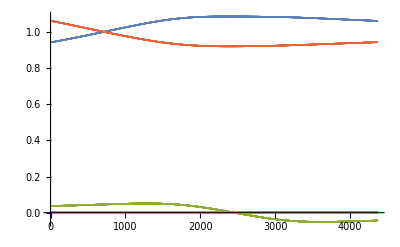

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue -0.5 (-6.93889×10^-18 Log[Abs[(0.-2. ⅈ)+z]]+1. √(0.0204082 Log[«1»]^2-0.0360388 Log[Abs[«1»]] Log[Abs[«1»]]+(0.0204082-2.1684×10^-19 ⅈ) Log[«1»]^2+0.00618505 Log[Abs[«1»]] Log[Abs[«1»]]+0.00681517 Log[Abs[«1»]] Log[Abs[«1»]]+0.01 Log[«1»]^2-0.0109626 Log[Abs[«1»]] Log[Abs[«1»]]-0.0115927 Log[Abs[«1»]] Log[Abs[«1»]]-0.0330002 Log[Abs[«1»]] Log[Abs[«1»]]+0.0277778 Log[«1»]^2)) with multiplicity 1.

MatrixExp::matsq: Argument … at position 1 is not a non-empty square matrix.

GraphicsGrid::list: MatrixExp[{,}] is not a list of lists.

GraphicsGrid[MatrixExp[{-Graphics3D-,-Graphics3D-}]]

```mathematica
x0=MakeHyperpolygon[2,3,0][[1]];
v0=Table[TraceFree[x0[[All,i;;i]].x0[[All,i;;i]]†],{i,1,4}];
(*w0=Table[TraceFree[y0[[i;;i,All]]†.y0[[i;;i,All]]],{i,1,4}];*)

p={-2.5,0,1.6,2ⅈ};R=.5;
H[z_]=MatrixExp@∑_(i=1)^4 R Log@Abs[z-p[[i]]]v0[[i]]//Quiet;

HData=ParallelTable[H[a+ⅈ b][[1,1]],{a,-3.01,3,.1},{b,-3.01,3,.1}]//Quiet;
ListPlot3D[Re@HData,PlotRange->All]

(*This part isn't correct because it uses delbar del log, which is inaccurate when the summands don't commute*)
LogHData=ParallelTable[MatrixLog[H[a+ⅈ b]][[1,2]],{a,-5.01,5,.1},{b,-5.01,5,.1}]//Quiet;
ListPlot3D[Re@LogHData,PlotRange->All]
DaLogH=(Differences[LogHData,{2,0}]/.1)[[All,2;;-2]];
DbLogH=(Differences[LogHData,{0,2}]/.1)[[2;;-2,All]];
ListPlot3D[Im[DaLogH+DbLogH],PlotRange->{All,All,{-.001,.001}}]


(*This part does it correctly without the delbar del log.  It shows that as R->0 the distinction doesn't matter.*)
DaH=(Differences[HData,{1,0}]/.1)[[All,1;;-2]];
DbH=(Differences[HData,{0,1}]/.1)[[1;;-2,All]];
AH=1/2(DaH-ⅈ DbH);
DaAH=(Differences[AH,{1,0}]/.1)[[All,2;;-1]];
DbAH=(Differences[AH,{0,1}]/.1)[[2;;-1,All]];
FH=1/2(DaAH+ⅈ DbAH);
ListPlot3D[Re@FH,PlotRange->{All,All,{-.01,.01}}]

(*Dz=1/2(∂_a #-ⅈ∂_b #)&; Dzbar=1/2(∂_a #+ⅈ∂_b #)&;
Dzbar@MatrixLog[H[a+ⅈ b]]*)

H[1.2]
Table[Flatten@{Re@H[z+ⅈ],Im@H[z+ⅈ]},{z,-1.9,2.9,.0011}];
ListPlot[%ᵀ]
GraphicsGrid@Map[ComplexPlot3D[Flatten@#,{z,-1.5-ⅈ,2.5+1.5ⅈ},PlotRange->Full,MaxRecursion->2]&,H[z],{2}]
```

#### Flowing Down Comparison

```mathematica
{x1,y1}=Chop@MakeHyperpolygon[.5,π/3,.7];
y0=ConstantArray[0,{4,2}];
g0={({{1, a12+ⅈ b12}, {0, a22^1}}),DiagonalMatrix[{λ1,λ2,λ3,λ4}^2]};
sol=FindRoot[Flatten[{μU1[groupActx[g0,x1],y0]-βTest,Table[projections[[i]][μSU2[groupActx[g0,x1],y0]],{i,1,3}]}],{{a12,0},{b12,0},{a22,1},{λ1,1},{λ2,1},{λ3,1},{λ4,1}}];
g0=g0/.sol;
x0=Chop@groupActx[g0,x1];
MakeHyperpolygon[2,π/3,0];(*these are the same lol but the first is more accurate*)

v1=Table[TraceFree[x1[[All,i;;i]].x1[[All,i;;i]]†],{i,1,4}];
w1=Table[TraceFree[y1[[i;;i,All]]†.y1[[i;;i,All]]],{i,1,4}];
v0=Table[TraceFree[x0[[All,i;;i]].x0[[All,i;;i]]†],{i,1,4}];

p={-1,0,2,3ⅈ};
ϕ[z_]:=Sum[(x1[[All,i;;i]].y1[[i;;i,All]])/(z-p[[i]]),{i,1,4}];
H[z_?NumericQ]:=MatrixExp@∑_(i=1)^4 Log@Abs[z-p[[i]]]v0[[i]];

(*Tr[Inverse[H[r ⅇ^(ⅈ θ)]].ϕ[r ⅇ^(ⅈ θ)]†.H[r ⅇ^(ⅈ θ)].ϕ[r ⅇ^(ⅈ θ)]]/.{r->.1,θ->0}*)
(*Plot[Tr[Inverse[H[r ⅇ^(ⅈ θ)]].ϕ[r ⅇ^(ⅈ θ)]†.H[r ⅇ^(ⅈ θ)].ϕ[r ⅇ^(ⅈ θ)]]/.r->.5,{θ,-π,π}]*)

H2[z_]=MatrixExp[R Log@Abs[z-p[[2]]]v0[[2]]];
ϕ2[z_]=(x1[[All,2;;2]].y1[[2;;2,All]])/(z-p[[2]]);
ϕNorm[z_]=Tr[Inverse[H2[z]].(ϕ2[z])†.H2[z].ϕ2[z]];

FullSimplify[R ϕNorm[r],r>0]
Chop[%,10^-12]
Chop[%,10^-1]
Integrate[%r,r](*Sometimes this goes to 0 as r->0, but other times there's extra terms which make it diverge*)
%/.r->.1/.R->0(*Same value regardless of r=δ>0*)
π/2(y1[[2;;2,All]].y1[[2;;2,All]]†)[[1,1]]

(*This is kind of concerning.  Any time h doesn't line up with ϕ, we pick up extra terms which make the integral diverge.  This actually makes a lot of sense, because I really should be using a metric compatible with the same flag when measuring ϕ.  I'll have to reassess my approach.*)

{A,λ}=g0;
H2New[z_]=A†.MatrixExp[R Log@Abs[z-p[[2]]]v0[[2]]].A;
ϕNorm[z_]=Tr[Inverse[H2New[z]].(ϕ2[z])†.H2New[z].ϕ2[z]];
Chop@FullSimplify[R ϕNorm[r],r>0]
Integrate[%r,r]
(y1[[2;;2,All]].y1[[2;;2,All]]†)[[1,1]]
yTilde=groupActy[g0,y1];
(yTilde[[2;;2,All]].yTilde[[2;;2,All]]†)[[1,1]]

Sum[TraceFree[x0[[All,i;;i]].x0[[All,i;;i]]†],{i,1,4}]
Sum[TraceFree[yTilde[[i;;i,All]]†.yTilde[[i;;i,All]]],{i,1,4}]//Chop//MatrixForm
```

(((0.0000451821+4.33681×10^-19 ⅈ)+(0.00951191+8.67362×10^-18 ⅈ) r^(0.285714 R)+(0.500621+1.21431×10^-17 ⅈ) r^(0.571429 R)) R)/(r^2. ((5.55112×10^-17-4.8768×10^-18 ⅈ)+1. r^(0.285714 R)-(9.64901×10^-35+7.68266×10^-18 ⅈ) r^(0.571429 R)))

1. r^(-2.-0.285714 R) (0.0000451821+0.00951191 r^(0.285714 R)+0.500621 r^(0.571429 R)) R

0.500621 r^(-2.+0.285714 R) R

1.75217 r^(0.285714 R)

1.75217

0.91979+0. ⅈ

0.513897 r^(-2.+0.285714 R) R

1.79864 r^(0.285714 R)

0.585556+0. ⅈ

1.79864+0. ⅈ

{{8.32667×10^-17+0. ⅈ,1.38778×10^-17+2.77556×10^-17 ⅈ},{1.38778×10^-17-2.77556×10^-17 ⅈ,-2.77556×10^-17+0. ⅈ}}

(0.738542 | 0.+0.963606 ⅈ
0.-0.963606 ⅈ | -0.738542)

```mathematica
H[z_?NumericQ]:=Product[Abs[z-p[[i]]]^(1/2),{i,1,4}]MatrixExp@∑_(i=1)^4 R Log@Abs[z-p[[i]]]v0[[i]];
HNorm[v_,z_]:=Tr[v†.H[z].v]
(*
Plot[{HNorm[x0[[All,2;;2]],r]/r^(1/2(1+2R βTest[[2]]))}/.R->1,{r,0.0000001,.1},PlotRange->{All,{0,All}}](*This section decays in norm like r^Subscript[β, 2]*)
Plot[{HNorm[{{0},{1}},r]/r^(1/2(1-2R βTest[[2]]))}/.R->1,{r,0.0000001,.001},PlotRange->{All,{0,All}}](*This section decays in norm like r^(-Subscript[β, 2])...  Sorta?*)
*)

vTest=({{1}, {a}});
Manipulate[Plot3D[(HNorm[vTest,z]/Abs[z-p[[1]]]^(1/2(1+2R βTest[[1]])))/.R->R0,{z,-1,-1+.001},{a,-.1,.1},PlotRange->All,AxesLabel->Automatic],{R0,0,1}](* The fastest-decay vector ({{1}, {a}}) tilts as R changes*)


HTest=√t MatrixExp[.2R Log[t]({{1, 0}, {0, -1}})+R Log@Abs[t-10]({{0, 1}, {1, 0}})]//Simplify;
HTestNorm[v_]:=Tr[v†.HTest.v];
Plot3D[(HTestNorm[vTest]/t^(1/2(1+.2)))/.R->1,{t,0,.1},{a,-1,1}](*Not good...  The fastest-decay vector has tilted to ({{1}, {a}}) for a around -0.7*)
Manipulate[Plot3D[(HTestNorm[vTest]/t^(1/2(1-.2R)))/.R->R0,{t,0,.01},{a,-1,1}],{R0,0,2}](*This demonstrates that we'll still get what we want as R->0*)
```

-Graphics3D-

#### Global Model

```mathematica
p={-1,0,2,3ⅈ};
{x0,y0}=Chop@MakeHyperpolygon[0,0,.9];
x0//MatrixForm
y0//MatrixForm
v0=Table[TraceFree[x0[[All,i;;i]].x0[[All,i;;i]]†],{i,1,4}];
w0=Table[TraceFree[y0[[i;;i,All]]†.y0[[i;;i,All]]],{i,1,4}];
MatrixForm/@v0
N0=Table[v0[[i]]/Norm[x0[[All,i]]]^2,{i,1,4}];
Sum[(Log[(2βTest[[i]])/Norm[x0[[All,i]]]^2 Abs[z-p[[i]]]^(2R βTest[[i]])]+2 Norm[y0[[i,All]]]^2 Abs[z-p[[i]]]^(2R βTest[[i]]))N0[[i]],{i,2,4}];
%/.{z->-1,R->0}//MatrixForm
N0[[1]]
```

(0.583638 | -0.00148079 | 0.00148079 | 0.460156
0 | 0.53452 | 0.53452 | 0)

(0 | -0.0854396
0 | 0
0 | 0
0 | 0.108367)

{(0.170317 | 0.
0. | -0.170317),(-0.142855 | -0.000791515
-0.000791515 | 0.142855),(-0.142855 | 0.000791515
0.000791515 | 0.142855),(0.105872 | 0.
0. | -0.105872)}

(-0.0167856 | -9.22696×10^-19
-9.22696×10^-19 | 0.0167856)

{{0.5,0.},{0.,-0.5}}

```mathematica
βTest[[1]]/(2 Norm[x0[[All,1]]]^2)
```

0.25

### First Variations of Harmonic Metrics

#### Numerical Attempt

```mathematica
(*Makes D[] ignore conjugate*)
excluded="ExcludedFunctions"/.
("DifferentiationOptions"/.System`SystemOptions["DifferentiationOptions"])
System`SetSystemOptions["DifferentiationOptions"->"ExcludedFunctions"->Union[excluded,{Conjugate}]]
```

{Hold,HoldComplete,Less,LessEqual,Greater,GreaterEqual,Inequality,Unequal,Nand,Nor,Xor,Not,Element,Exists,ForAll,Implies,Positive,Negative,NonPositive,NonNegative,Replace,ReplaceAll,ReplaceRepeated}

DifferentiationOptions→{AlwaysThreadGradients→False,DifferentiateHeads→True,DifferentiateIteratorIndexed→True,DirectHighDerivatives→True,DirectHighDerivativeThreshold→10,ExcludedFunctions→{Conjugate,Element,Exists,ForAll,Greater,GreaterEqual,Hold,HoldComplete,Implies,Inequality,Less,LessEqual,Nand,Negative,NonNegative,NonPositive,Nor,Not,Positive,Replace,ReplaceAll,ReplaceRepeated,Unequal,Xor},ExitOnFailure→False,HighDerivativeMaxTerms→1000,SymbolicAutomaticDifferentiation→False}

```mathematica
p={-1,0,2,3ⅈ};
{x0,y0}=Chop@MakeHyperpolygon[.6,.4,.7];
x0//MatrixForm;
y0//MatrixForm;
x1=x0[[All,1;;1]];
y1=y0[[1;;1,All]];
(*xdot1=({{a}, {b}});ydot1=({{c, d}});*)
xdot1=y1†;ydot1=({{0, 0}});
(*sols=Solve[{ydot1.x1+y1.xdot1==0,x1†.xdot1-ydot1.y1†==0},{a,b,c,d}]//Quiet
testingRules={a->1,b->0}; (*This is the case where I already know the result holds*)
xdot1=xdot1/.sols[[1]]/.testingRules
ydot1=ydot1/.sols[[1]]/.testingRules*)
ϕ=x1.y1//Chop;
ϕdot1=x1.ydot1+xdot1.y1//Chop;
ϕdot1//MatrixForm

xx[t_]:=x1+t xdot1;
yy[t_]:=y1+t ydot1;

(*Shows that μU1 is solved up to first order*)
(*Plot[Norm[xx[t]]^2-Norm[yy[t]]^2,{t,0,.1}]*)

(*
v0=Table[TraceFree[x0[[All,i;;i]].x0[[All,i;;i]]†],{i,1,4}];
w0=Table[TraceFree[y0[[i;;i,All]]†.y0[[i;;i,All]]],{i,1,4}];
N0=Table[v0[[i]]/Norm[x0[[All,i]]]^2,{i,1,4}];
*)
N1=TraceFree[xx[t].xx[t]†]/Norm[xx[t]]^2//Chop;
λ[r_,R_,t_]=(2βTest[[1]] r^(2R βTest[[1]]))/(Norm[xx[t]]^2-Norm[yy[t]]^2 r^(4R βTest[[1]]));
D[Log[λ[r,R,t]], t]/.(D[Conjugate[t], t]->1)/.t->0//Chop
Ndot=D[N1, t]/.(Conjugate[t]->t)/.t->0//Chop;
Ndot//MatrixForm
ϕ/Norm[x1]^2//MatrixForm
ν[r_,R_]=Log[λ[r,R,0]]Ndot;
A01[r_,R_]=D[(ν[r,R]/.r->√(z zbar)), zbar]ⅆzbar/.z->r^2/zbar//FullSimplify
A01[0,1]//Chop
Norm[%zbar/ⅆzbar]^2//Chop
%+Norm[ϕdot1]^2

Norm[xdot1]^2
Norm[ϕdot1]^2

Manipulate[Plot[λ[r,R,t],{r,0,1},PlotRange->{All,{0,1}}],{R,0,1},{t,0,1}]
```

(0 | 0
0 | 0.340368)

0

(0 | 0.388737+0.595066 ⅈ
0.388737-0.595066 ⅈ | 0)

(0. | 0.388737+0.595066 ⅈ
0. | 0.)

{{0,(((-0.0647896-0.0991777 ⅈ)-(0.25648+0.392612 ⅈ)/(-1.97933+1. (r^2)^(R/3))) R ⅆzbar)/zbar},{(((-0.0647896+0.0991777 ⅈ)-(0.25648-0.392612 ⅈ)/(-1.97933+1. (r^2)^(R/3))) R ⅆzbar)/zbar,0}}

{{0,((0.0647896+0.0991777 ⅈ) ⅆzbar)/zbar},{((0.0647896-0.0991777 ⅈ) ⅆzbar)/zbar,0}}

0.0140339

0.129884

0.340368

0.11585

#### Symbolic Attempt

```mathematica
(*Makes D[] ignore conjugate*)
excluded="ExcludedFunctions"/.
("DifferentiationOptions"/.System`SystemOptions["DifferentiationOptions"])
System`SetSystemOptions["DifferentiationOptions"->"ExcludedFunctions"->Union[excluded,{Conjugate,ConjugateTranspose,Transpose,Tr}]]
```

{Conjugate,ConjugateTranspose,Element,Exists,ForAll,Greater,GreaterEqual,Hold,HoldComplete,Implies,Inequality,Less,LessEqual,Nand,Negative,NonNegative,NonPositive,Nor,Not,Positive,Replace,ReplaceAll,ReplaceRepeated,Transpose,Unequal,Xor}

DifferentiationOptions→{AlwaysThreadGradients→False,DifferentiateHeads→True,DifferentiateIteratorIndexed→True,DirectHighDerivatives→True,DirectHighDerivativeThreshold→10,ExcludedFunctions→{Conjugate,ConjugateTranspose,Element,Exists,ForAll,Greater,GreaterEqual,Hold,HoldComplete,Implies,Inequality,Less,LessEqual,Nand,Negative,NonNegative,NonPositive,Nor,Not,Positive,Replace,ReplaceAll,ReplaceRepeated,Tr,Transpose,Unequal,Xor},ExitOnFailure→False,HighDerivativeMaxTerms→1000,SymbolicAutomaticDifferentiation→False}

```mathematica
Clear[x1,y1,xdot1,ydot1,xx,yy,λ]
xx[t_]:=x1+t xdot1;
yy[t_]:=y1+t ydot1;
MyNorm[v_]=√Tr[ConjugateTranspose[v].v];
NN[t_]=TraceFree[xx[t].xx[t]†]/MyNorm[xx[t]]^2;
λ[r_,R_,t_]=(2βTest[[1]] r^(2R βTest[[1]]))/(MyNorm[xx[t]]^2-MyNorm[yy[t]]^2 r^(4R βTest[[1]]));

zeroFunc[a_]=0;
oneFunc[a_]=1;
derivativeRules=Thread[{ConjugateTranspose',Tr'}->oneFunc];
D[NN[t], t]/.derivativeRules/.t->0//FullSimplify//MatrixForm
D[(Log[λ[r,R,t]]), t]/.derivativeRules/.t->0//FullSimplify
```

D::ivar: 0 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

((∂_0 Tr[ConjugateTranspose[x1].x1] (-2 x1.ConjugateTranspose[x1]+Tr[x1.ConjugateTranspose[x1]])+(-∂_0 Tr[x1.ConjugateTranspose[x1]]+2 (x1.∂_0 ConjugateTranspose[x1]+xdot1.ConjugateTranspose[x1])) Tr[ConjugateTranspose[x1].x1])/(2 Tr[ConjugateTranspose[x1].x1]^2) | (-∂_0 Tr[ConjugateTranspose[x1].x1] x1.ConjugateTranspose[x1]+(x1.∂_0 ConjugateTranspose[x1]+xdot1.ConjugateTranspose[x1]) Tr[ConjugateTranspose[x1].x1])/Tr[ConjugateTranspose[x1].x1]^2
(-∂_0 Tr[ConjugateTranspose[x1].x1] x1.ConjugateTranspose[x1]+(x1.∂_0 ConjugateTranspose[x1]+xdot1.ConjugateTranspose[x1]) Tr[ConjugateTranspose[x1].x1])/Tr[ConjugateTranspose[x1].x1]^2 | (∂_0 Tr[ConjugateTranspose[x1].x1] (-2 x1.ConjugateTranspose[x1]+Tr[x1.ConjugateTranspose[x1]])+(-∂_0 Tr[x1.ConjugateTranspose[x1]]+2 (x1.∂_0 ConjugateTranspose[x1]+xdot1.ConjugateTranspose[x1])) Tr[ConjugateTranspose[x1].x1])/(2 Tr[ConjugateTranspose[x1].x1]^2))

D::ivar: 0 is not a valid variable.

(∂_0 Tr[ConjugateTranspose[x1].x1]-r^(2 R/3) ∂_0 Tr[ConjugateTranspose[y1].y1])/(-Tr[ConjugateTranspose[x1].x1]+r^(2 R/3) Tr[ConjugateTranspose[y1].y1])

#### Symbolic Reduced Case

```mathematica
Clear[x1,y1,xdot1,ydot1,xx,yy,λ]
x1=({{x11}, {0}});y1=({{0, y12}});
xdot1=y1†;
ydot1=({{0, 0}});
xx[t_]:=x1+t xdot1;
yy[t_]:=y1+t ydot1;
MyNorm[v_]:=√Tr[Transpose[v].v];
NN[t_]:=TraceFree[xx[t].xx[t]ᵀ]/MyNorm[xx[t]]^2;
λ[r_,R_,t_]:=(2β[[1]] r^(2R β[[1]]))/(MyNorm[xx[t]]^2-MyNorm[yy[t]]^2 r^(4R β[[1]]));

derivativeRules={D[Transpose[x1+t xdot1], t]->Transpose[xdot1],D[Tr[(x1+t xdot1).Transpose[x1+t xdot1]], t]->Tr[x1.Transpose[xdot1]+xdot1.Transpose[x1]]};
Ndot=D[NN[t], t]/.t->0
NdotPlus=(x1.y1)/MyNorm[x1]^2;
NdotMinus=(y1†.x1†)/MyNorm[x1]^2;
(*I think the log is incorrect here.  Exp[] doesn't behave this way on strictly lower triangular stuff*)
D[(Log[λ[r,R,t]]), t]/.derivativeRules/.t->0;

ν=Log[λ[r,R,0]]NdotMinus;
delbarν=(D[(Log[λ[r,R,0]]/.r->√(z zbar)), zbar]ⅆzbar/.(z->r^2/zbar))NdotMinus//FullSimplify;
delbarν//MatrixForm
hR=DiagonalMatrix[{λ[r,R,0],λ[r,R,0]^-1}];
Tr[delbarν.hR.delbarν†.Inverse[hR]/.{ⅆzbar->1,z->r,zbar->r}]//Realify
(4 r^(-2+4 R β1) R^2 y12^2 (x11^2)^2 β1^4)/(x11^2 (x11^2)^2 (x11^2)^2)
∫R^-1%r ⅆr
```

{{0,Conjugate[y12]/x11},{Conjugate[y12]/x11,0}}

(0 | 0
(R (x11^2+(r^2)^(2 R β1) y12^2) β1 Conjugate[x11] Conjugate[y12] ⅆzbar)/(x11^2 (x11^2-(r^2)^(2 R β1) y12^2) zbar) | 0)

(4 r^(-2+4 R β1) R^2 y12^2 (x11^2+(r^4)^(R β1) y12^2)^2 β1^4)/(x11^2 (x11^2-r^(4 R β1) y12^2)^2 (x11^2-(r^4)^(R β1) y12^2)^2)

(4 r^(-2+4 R β1) R^2 y12^2 β1^4)/x11^6

(r^(4 R β1) y12^2 β1^3)/x11^6

```mathematica
λ[r,R,0]
Clear[ν]
ν=(λ[r,R,0]^2-1)NdotMinus//Realify//FullSimplify;
ν//MatrixForm
delbarν=(D[(ν/.r->√(z zbar)), zbar]ⅆzbar/.(z->r^2/zbar))NdotMinus//Realify//FullSimplify;
delbarν//MatrixForm
delbarν[[2,1]]
hR=DiagonalMatrix[{λ[r,R,0],λ[r,R,0]^-1}];
R^-1 FullSimplify[Tr[delbarν.Inverse[hR].delbarνᵀ.hR/.{ⅆzbar->1,z->r,zbar->r}]//Realify,r>0]
R^-1 Tr[ν.Inverse[hR].delbarνᵀ.hR]//Realify
FullSimplify[%,{r>0,R>0,β1>0}]
FullSimplify[%/.r->0,{R>0,β1>0}]
%%%/.R->0//FullSimplify
%/.β1->1/2(x11^2-y12^2)
```

(2 r^(2 R β1) β1)/(x11^2-r^(4 R β1) y12^2)

(0 | 0
(y12 (-1+(4 r^(4 R β1) β1^2)/((x11^2-r^(4 R β1) y12^2)^2)))/x11 | 0)

(0 | 0
(8 R y12^2 ((r^4)^(R β1) x11^2-((r^4)^(2 R β1)-2 (r^8)^(R β1)) y12^2) β1^3 ⅆzbar)/(x11^2 (x11^2-(r^4)^(R β1) y12^2)^3 zbar) | 0)

(8 R y12^2 ((r^4)^(R β1) x11^2-((r^4)^(2 R β1)-2 (r^8)^(R β1)) y12^2) β1^3 ⅆzbar)/(x11^2 (x11^2-(r^4)^(R β1) y12^2)^3 zbar)

(16 r^(-2+4 R β1) R y12^4 (x11^2+r^(4 R β1) y12^2)^2 β1^4)/((x11^3-r^(4 R β1) x11 y12^2)^4)

(2 r^(-4 R β1) y12^3 (x11^2-r^(4 R β1) y12^2)^2 ((r^4)^(R β1) x11^2+(r^8)^(R β1) y12^2) β1 (-1+(4 r^(4 R β1) β1^2)/((x11^2-r^(4 R β1) y12^2)^2)) ⅆzbar)/(x11^3 (x11^2-(r^4)^(R β1) y12^2)^3 zbar)

-(2 y12^3 (x11^2+r^(4 R β1) y12^2) β1 (x11^4+r^(8 R β1) y12^4-2 r^(4 R β1) (x11^2 y12^2+2 β1^2)) ⅆzbar)/((x11^3-r^(4 R β1) x11 y12^2)^3 zbar)

-(2 y12^3 β1 ⅆzbar)/(x11^3 zbar)

-(2 y12^3 (x11^2+y12^2) β1 ((x11^2-y12^2)^2-4 β1^2) ⅆzbar)/((x11^3-x11 y12^2)^3 zbar)

0

```mathematica
MatrixExp[({{f, 0}, {0, -f}})+t({{0, a}, {a, 0}})];
∂_t %/.t->0//FullSimplify//MatrixForm

MatrixExp[t({{0, n}, {0, 0}})].MatrixExp[({{f, 0}, {0, -f}})].MatrixExp[t({{0, 0}, {n, 0}})];
∂_t %/.t->0//FullSimplify//MatrixForm
Solve[({{0, (a Sinh[f])/f}, {(a Sinh[f])/f, 0}})==({{0, ⅇ^-f n}, {ⅇ^-f n, 0}}),n]
n/.%[[1]]/.a->2f c
%/.f->Log[λ]
```

(0 | (a Sinh[f])/f
(a Sinh[f])/f | 0)

(0 | ⅇ^-f n
ⅇ^-f n | 0)

{{n→(a ⅇ^f Sinh[f])/f}}

2 c ⅇ^f Sinh[f]

c (-1+λ^2)

#### More General Case, Still “Diagonal”

```mathematica
Clear[x,y,x1,y1,xdot1,ydot1,xx,yy,λ]
x=({{x1}, {0}});y=({{0, y2}});
xdot=({{0}, {xdot2}});ydot=({{ydot1, 0}});
xx[t_]:=x+t xdot;
yy[t_]:=y+t ydot;
MyNorm[v_]:=√Tr[Transpose[v].v];
NN[t_]:=TraceFree[xx[t].xx[t]ᵀ]/MyNorm[xx[t]]^2;
λ[r_,R_,t_]:=(2β[[1]] r^(2R β[[1]]))/(MyNorm[xx[t]]^2-MyNorm[yy[t]]^2 r^(4R β[[1]]));

derivativeRules={D[Transpose[x+t xdot], t]->Transpose[xdot],D[Tr[(x+t xdot).Transpose[x+t xdot]], t]->Tr[x.Transpose[xdot]+xdot.Transpose[x]]};
Ndot=D[NN[t], t]/.t->0;
NdotPlus=ReplacePart[Ndot,{2,1}->0];
NdotMinus=ReplacePart[Ndot,{1,2}->0];

ν=(λ[r,R,0]^2-1)NdotMinus//Realify//FullSimplify;
delbarν=(D[(ν/.r->√(z zbar)), zbar]ⅆzbar/.(z->r^2/zbar))//FullSimplify;
hR=DiagonalMatrix[{λ[r,R,0],λ[r,R,0]^-1}];
(*R^-1 FullSimplify[Tr[delbarν.Inverse[hR].delbarνᵀ.hR/.{ⅆzbar->1,z->r,zbar->r}]//Realify,r>0]*)
R^-1 Tr[ν.Inverse[hR].delbarνᵀ.hR]//FullSimplify;
FullSimplify[%,{r>0,R>0,β1>0}]
FullSimplify[%/.r->0,{R>0,β1>0}]
%/.β1->1/2(x1^2-y2^2)/.ⅆzbar->-2π ⅈ zbar//Expand
%/.(xdot2^2 y2^2->x1^2 ydot1^2)

Print["----------------------------------------------------------------------------"]

ϕ=(x.y)/z;
ϕdot=(xdot.y+x.ydot)/z
Φ=ϕdot+LieBracket[ν,ϕ]//FullSimplify;
Φ//MatrixForm
FullSimplify[Φ/.r->0,{R>0,β1>0}]//MatrixForm(*0 using the ⅆ Subscript[μ, U(1)]=0 condition*)

FullSimplify[Tr[Inverse[hR].ϕdot.hR.Φ]/.z->r,x1 ydot1+xdot2 y2==0]
2π Integrate[R%r,r]
innerEdge=FullSimplify[%/.r->0,{R>0,β1>0}]
outerEdge=Limit[%%,R->0]
innerEdge/.β1->1/2(x1^2-y2^2)//Expand
outerEdge/.β1->1/2(x1^2-y2^2)//FullSimplify
FullSimplify[(outerEdge-innerEdge)/.β1->1/2(x1^2-y2^2)]
```

-(2 xdot2^2 (x1^2+r^(4 R β1) y2^2) β1 (x1^4+r^(8 R β1) y2^4-2 r^(4 R β1) (x1^2 y2^2+2 β1^2)) ⅆzbar)/(x1^2 (x1^2-r^(4 R β1) y2^2)^3 zbar)

-(2 xdot2^2 β1 ⅆzbar)/(x1^2 zbar)

2 ⅈ π xdot2^2-(2 ⅈ π xdot2^2 y2^2)/x1^2

2 ⅈ π xdot2^2-2 ⅈ π ydot1^2

----------------------------------------------------------------------------

{{(x1 ydot1)/z,0},{0,(xdot2 y2)/z}}

((x1 ydot1+xdot2 (y2-(4 r^(4 R β1) y2 β1^2)/((x1^2-r^(4 R β1) y2^2)^2)))/z | 0
0 | (4 r^(4 R β1) xdot2 y2 β1^2)/((x1^2-r^(4 R β1) y2^2)^2 z))

((xdot2 y2+x1 ydot1)/z | 0
0 | 0)

(8 r^(-2+4 R β1) x1^2 ydot1^2 β1^2)/((x1^2-r^(4 R β1) y2^2)^2)

(16 π R x1^2 ydot1^2 β1^2)/(4 R x1^2 y2^2 β1-4 r^(4 R β1) R y2^4 β1)

(4 π ydot1^2 β1)/y2^2

(4 π x1^2 ydot1^2 β1)/(x1^2 y2^2-y2^4)

-2 π ydot1^2+(2 π x1^2 ydot1^2)/y2^2

(2 π x1^2 ydot1^2)/y2^2

2 π ydot1^2

#### Fully General Case

```mathematica
Clear[x,y,x1,y1,xdot1,ydot1,xx,yy,λ]
x=({{x1}, {0}});y=({{0, y2}});
xdot=({{xdot1}, {xdot2}});ydot=({{ydot1, ydot2}});
xx[t_]:=x+t xdot;
yy[t_]:=y+t ydot;
MyNorm[v_]:=√Tr[Transpose[v].v];
NN[t_]:=TraceFree[xx[t].xx[t]ᵀ]/MyNorm[xx[t]]^2;
λ[r_,R_,t_]:=(2β[[1]] r^(2R β[[1]]))/(MyNorm[xx[t]]^2-MyNorm[yy[t]]^2 r^(4R β[[1]]));
hR=DiagonalMatrix[{λ[r,R,0],λ[r,R,0]^-1}];

derivativeRules={D[Transpose[x+t xdot], t]->Transpose[xdot],D[Tr[(x+t xdot).Transpose[x+t xdot]], t]->Tr[x.Transpose[xdot]+xdot.Transpose[x]]};
NN[t]//MatrixForm;
Ndot=D[NN[t], t]/.t->0;
NdotPlus=ReplacePart[Ndot,{2,1}->0];
NdotMinus=ReplacePart[Ndot,{1,2}->0];
ΛdotTerm1=2Log[λ[r,R,0]]Ndot;
ΛdotTerm2=2(D[Log[λ[r,R,t]], t] /.t->0 )NN[0]/.(xdot2 y2->-x1 ydot1);
Λdot=ΛdotTerm1+ΛdotTerm2;
Λdot//MatrixForm

FullSimplify[D[MatrixExp[({{f, 0}, {0, -f}})+t({{b, a*}, {a, -b}})], t]/.t->0]//MatrixForm
MatrixExp[t({{m, 0}, {n, -m}})†].MatrixExp[({{f, 0}, {0, -f}})].MatrixExp[t({{m, 0}, {n, -m}})];
∂_t %/.t->0//FullSimplify//MatrixForm
Solve[({{b ⅇ^f, (a Sinh[f])/f}, {(a Sinh[f])/f, b (-Cosh[f]+Sinh[f])}})==({{2 ⅇ^f m, ⅇ^-f n}, {ⅇ^-f n, -2 ⅇ^-f m}}),{n,m}];
(*Solve[({{b ⅇ^f, (a Sinh[f])/f}, {(a Sinh[f])/f, b (-Cosh[f]+Sinh[f])}})==({{2 ⅇ^f m, 2 n Cosh[f]}, {2 n Cosh[f], -2 ⅇ^-f m}}),{n,m}];*)
({{m, 0}, {n, -m}})/.%[[1]];
ν=%/.{b->Λdot[[1,1]],a->Λdot[[1,2]],f->Log[λ[r,R,0]]}//FullSimplify;
ν//MatrixForm
delbarν=FullSimplify[(D[(ν/.r->√(z zbar)), zbar]ⅆzbar/.(z->r^2/zbar)),r>0];
delbarν//MatrixForm
FullSimplify[-ⅈ R^-1 Tr[Inverse[hR].νᵀ.hR.delbarν]/.r->0,{R>0,β1>0}]
%/.β1->1/2(x1^2-y2^2)//Expand
metricTerm1=%/.(xdot2^2 y2^2->x1^2 ydot1^2)/.ⅆzbar->-2π ⅈ zbar;
Print["Integral of first term is: "metricTerm1]
Print["------------------------------------------------------"]

ϕ=(x.y)/z;
ϕdot=(xdot.y+x.ydot)/z;
Φ=ϕdot+LieBracket[ν,ϕ]//FullSimplify
FullSimplify[Φ/.r->0,{R>0,β1>0}]//MatrixForm(*diag is 0 using the ⅆ Subscript[μ, U(1)]=0 condition*)

Print["Value of trace is:"]
FullSimplify[-ⅈ R Tr[Inverse[hR].ϕdotᵀ.hR.Φ]/.z->r,x1 ydot1+xdot2 y2==0]
(2ⅈ)2π Integrate[%r,r](*The 2ⅈ is from converting to r dr dθ*)
innerEdge=FullSimplify[%/.r->0,{R>0,β1>0}]
outerEdge=Limit[%%,R->0];
Print["Inner edge is:"]
Expand[innerEdge/.β1->1/2(x1^2-y2^2)]/.(x1^2 ydot1^2->xdot2^2 y2^2)
Print["Outer edge is:"]
FullSimplify[outerEdge/.β1->1/2(x1^2-y2^2),x1 ydot1+xdot2 y2==0]
metricTerm2=FullSimplify[(outerEdge-innerEdge)/.β1->1/2(x1^2-y2^2),x1 ydot1+xdot2 y2==0];
%/.(x1^2 ydot1^2->-xdot2^2 y2^2)//FullSimplify
Print["Second term of integral is:"]
Print[metricTerm2]
Print["Total integral is:"]
FullSimplify[metricTerm1+metricTerm2,x1 ydot1+xdot2 y2==0]
```

(-(2 x1 xdot1-2 r^(4 R β1) y2 ydot2)/(x1^2-r^(4 R β1) y2^2) | (2 xdot2 Log[(2 r^(2 R β1) β1)/(x1^2-r^(4 R β1) y2^2)])/x1
(2 xdot2 Log[(2 r^(2 R β1) β1)/(x1^2-r^(4 R β1) y2^2)])/x1 | (2 x1 xdot1-2 r^(4 R β1) y2 ydot2)/(x1^2-r^(4 R β1) y2^2))

(b ⅇ^f | (Conjugate[a] Sinh[f])/f
(a Sinh[f])/f | b (-Cosh[f]+Sinh[f]))

(2 ⅇ^f Re[m] | ⅇ^-f Conjugate[n]
ⅇ^-f n | -2 ⅇ^-f Re[m])

((-x1 xdot1+r^(4 R β1) y2 ydot2)/(x1^2-r^(4 R β1) y2^2) | 0
(xdot2 (-1+(4 r^(4 R β1) β1^2)/((x1^2-r^(4 R β1) y2^2)^2)))/x1 | (x1 xdot1-r^(4 R β1) y2 ydot2)/(x1^2-r^(4 R β1) y2^2))

((2 r^(4 R β1) R x1 y2 (-xdot1 y2+x1 ydot2) β1 ⅆzbar)/((x1^2-r^(4 R β1) y2^2)^2 zbar) | 0
(8 r^(4 R β1) R xdot2 (x1^2+r^(4 R β1) y2^2) β1^3 ⅆzbar)/(x1 (x1^2-r^(4 R β1) y2^2)^3 zbar) | -(2 r^(4 R β1) R x1 y2 (-xdot1 y2+x1 ydot2) β1 ⅆzbar)/((x1^2-r^(4 R β1) y2^2)^2 zbar))

(2 ⅈ xdot2^2 β1 ⅆzbar)/(x1^2 zbar)

(ⅈ xdot2^2 ⅆzbar)/zbar-(ⅈ xdot2^2 y2^2 ⅆzbar)/(x1^2 zbar)

Integral of first term is:  (2 π xdot2^2-2 π ydot1^2)

------------------------------------------------------

{{(x1 ydot1+xdot2 (y2-(4 r^(4 R β1) y2 β1^2)/((x1^2-r^(4 R β1) y2^2)^2)))/z,((x1^2+r^(4 R β1) y2^2) (-xdot1 y2+x1 ydot2))/((x1^2-r^(4 R β1) y2^2) z)},{0,(4 r^(4 R β1) xdot2 y2 β1^2)/((x1^2-r^(4 R β1) y2^2)^2 z)}}

((xdot2 y2+x1 ydot1)/z | (-xdot1 y2+x1 ydot2)/z
0 | 0)

Value of trace is:

-(4 ⅈ r^(-2+4 R β1) R (r^(4 R β1) xdot1^2 y2^4-x1^4 (2 ydot1^2+ydot2^2)+x1^2 y2^2 (xdot1^2+r^(4 R β1) (2 ydot1^2-ydot2^2))) β1^2)/((-x1^2+r^(4 R β1) y2^2)^3)

(4 π (2 x1^4 ydot1^2-r^(4 R β1) y2^2 (xdot1^2 y2^2+x1^2 (2 ydot1^2-ydot2^2))) β1)/((x1^2 y2-r^(4 R β1) y2^3)^2)

(8 π ydot1^2 β1)/y2^2

Inner edge is:

4 π xdot2^2-4 π ydot1^2

Outer edge is:

(2 π (xdot1^2 y2^4-x1^2 (2 (x1-y2) (x1+y2) ydot1^2+y2^2 ydot2^2)))/(-x1^2 y2^2+y2^4)

(2 π (-y2^2 (xdot1^2+2 ydot1^2)+x1^2 (2 ydot1^2+ydot2^2)))/((x1-y2) (x1+y2))

Second term of integral is:

(2 π (-y2^2 (xdot1^2+2 ydot1^2)+x1^2 (2 ydot1^2+ydot2^2)))/((x1-y2) (x1+y2))

Total integral is:

(2 π (-y2^2 (xdot1^2+ydot1^2)+x1^2 (xdot2^2+ydot2^2)))/((x1-y2) (x1+y2))

```mathematica
(2 π (-y2^2 (xdot1^2+2 ydot1^2+ydot2^2)+x1^2 (2 ydot1^2+ydot2^2+xdot1^2)))/((x1-y2) (x1+y2))//FullSimplify
(2 π (-y2^2 (xdot1^2+ydot1^2+xdot2^2+ydot2^2)+x1^2 (xdot2^2+ydot2^2+xdot1^2+ydot1^2)))/((x1-y2) (x1+y2))//FullSimplify
```

2 π (xdot1^2+2 ydot1^2+ydot2^2)

2 π (xdot1^2+xdot2^2+ydot1^2+ydot2^2)

#### Integral Calculation No Shortcuts

```mathematica
Clear[x,y,x1,y1,xdot1,ydot1,xx,yy,λ]
x=({{x1}, {0}});y=({{0, y2}});
xdot=({{xdot1}, {xdot2}});ydot=({{ydot1, ydot2}});
xx[t_]:=x+t xdot;
yy[t_]:=y+t ydot;
MyNorm[v_]:=√Tr[v†.v];

λ[r_,R_]:=(2β[[1]] r^(2R β[[1]]))/(x1*x1-y2*y2 r^(4R β[[1]]));
hpure=DiagonalMatrix[{λpure,λpure^-1}];
ν11=1/2((y2*ydot2+y2 ydot2*)(r^(4 R β1)-1))/(x1*x1-y2*y2 r^(4 R β1));
ν21=(λpure^2-1)xdot2/x1;
ν=({{ν11, 0}, {ν21, -ν11}});

ϕ=(x.y)/z;
ϕdot=(xdot.y+x.ydot)/z;
Φ=ϕdot+LieBracket[({{ν11pure, 0}, {ν21, -ν11pure}}),ϕ]//FullSimplify;

Tr[Inverse[hpure].ϕdot†.hpure.Φ]/.z->r
Print["First two terms combine to a simple expression:"]
FullSimplify[(xdot2 y2 λpure^2 Conjugate[xdot2 y2])/(r Conjugate[r])+((xdot2 y2+x1 ydot1-xdot2 y2 λpure^2) Conjugate[x1 ydot1])/(r Conjugate[r]),{x1 ydot1+xdot2 y2==0,r>0}]
Print["This simplifies to"]
(x1 ydot1 λpure^2 (2Conjugate[x1 ydot1]))/r^2
Print["which integrates to"]
term1=Integrate[(2 x1 ydot1 λpure^2 Conjugate[x1 ydot1])/r^2 r/.λpure->λ[r,R],r]
Print["The inner edge r->0 gives"]
FullSimplify[%%/.r->0,{R>0,β1>0}];
Expand[%/.β1->1/2(x1*x1-y2*y2)]

Print["The outer edge R->0 is"]
FullSimplify[FullSimplify[R term1]/.R->0/.β1->1/2(x1*x1-y2*y2)]
outer1=Realify[%]

Print["Meanwhile, the last term splits into two parts:"]
FullSimplify[(λpure^2 Abs[xdot1 y2+x1 ydot2]^2)/(r Conjugate[r])/.λpure->λ[r,R],{r>0,x1 ydot1+xdot2 y2==0,x1*xdot1==y2*ydot2}]
FullSimplify[(2 λpure^2 x1 y2 ν11pure Conjugate[xdot1 y2+x1 ydot2])/(r Conjugate[r])/.{λpure->λ[r,R],ν11pure->ν11},{r>0}]
Print["These respectively integrate to:"]
term2=Integrate[%%%r,r]
term3=Integrate[%%%r,r]

Print["The inner edge contributions are:"]
Print["Second and third terms:"]
FullSimplify[R(term2+term3)/.r->0,{R>0,β1>0,x1 ydot1+xdot2 y2==0,x1*xdot1==y2*ydot2}]
Realify[%/.β1->1/2(x1*x1-y2*y2)]
FullSimplify[(y2^2 (x1^2-y2^2) ydot2 (xdot1 y2+x1 ydot2))/(x1^3 (2 x1^2-2 y2^2))+((x1^2-y2^2) (xdot1 y2+x1 ydot2)^2)/(2(x1 y2)^2),{x1 ydot1+xdot2 y2==0,x1 xdot1==y2 ydot2}]
Expand[%]

Print["Second term inner edge"]

FullSimplify[R term2/.r->0,{R>0,β1>0,x1 ydot1+xdot2 y2==0}]
FullSimplify[%/.β1->1/2(x1*x1-y2*y2),{R>0,x1 ydot1+xdot2 y2==0}]
Realify[%]
inner2=FullSimplify[((x1^2-y2^2) (xdot1 y2+x1 ydot2)^2)/(2 (x1 y2)^2),{x1 ydot1+xdot2 y2==0,x1 xdot1==y2 ydot2}]

Print["Second term outer edge:"]
FullSimplify[FullSimplify[R(term2)]/.R->0/.β1->1/2(x1*x1-y2*y2)]
outer2=Realify[%]

Print["Total term 2 integral:"]
totalIntegral2=FullSimplify[outer2-inner2,{x1 ydot1+xdot2 y2==0,x1 xdot1==y2 ydot2}]//Expand

Print["Third term inner edge:"]
FullSimplify[R(term3)/.r->0,{R>0,β1>0,x1 ydot1+xdot2 y2==0}]
FullSimplify[%/.β1->1/2(x1*x1-y2*y2),{R>0,x1 ydot1+xdot2 y2==0}]
inner3=FullSimplify[Realify[%],{x1 ydot1+xdot2 y2==0,x1 xdot1==y2 ydot2}]
(*FullSimplify[R(term1+term2+term3)/.r->0,{R>0,β1>0,x1 ydot1+xdot2 y2==0,x1*xdot1==y2*ydot2}];*)

Print["Third term outer edge:"]
outer3=FullSimplify[R(term3)/.R->0]
totalIntegral3=outer3-inner3;

Print["Sum of term 2 and 3 integrals:"]
FullSimplify[totalIntegral2+totalIntegral3,{x1 ydot1+xdot2 y2==0,x1 xdot1==y2 ydot2}]
```

(xdot2 y2 λpure^2 Conjugate[xdot2 y2])/(r Conjugate[r])+((xdot2 y2+x1 ydot1-xdot2 y2 λpure^2) Conjugate[x1 ydot1])/(r Conjugate[r])+(λpure^2 (xdot1 y2+x1 ydot2+2 x1 y2 ν11pure) Conjugate[xdot1 y2+x1 ydot2])/(r Conjugate[r])

First two terms combine to a simple expression:

(x1 ydot1 λpure^2 (-Conjugate[xdot2] Conjugate[y2]+Conjugate[x1 ydot1]))/r^2

This simplifies to

(2 x1 ydot1 λpure^2 Conjugate[x1 ydot1])/r^2

which integrates to

(8 x1 ydot1 β1^2 Conjugate[x1 ydot1])/(4 R x1 y2 β1 Conjugate[x1] Conjugate[y2]-4 r^(4 R β1) R y2^2 β1 Conjugate[y2]^2)

The inner edge r->0 gives

(x1 ydot1 Conjugate[x1] Conjugate[ydot1])/(R Abs[y2]^2)-(y2 ydot1 Conjugate[y2] Conjugate[ydot1])/(R Abs[y2]^2)

The outer edge R->0 is

(x1 ydot1 Conjugate[x1] Conjugate[ydot1])/Abs[y2]^2

(x1^2 ydot1^2)/y2^2

Meanwhile, the last term splits into two parts:

(4 r^(-2+4 R β1) β1^2 Abs[xdot1 y2+x1 ydot2]^2)/((Abs[x1]^2-r^(4 R β1) y2 Conjugate[y2])^2)

-(4 r^(-2+4 R β1) (-1+r^(4 R β1)) x1 y2 β1^2 (ydot2 Conjugate[y2]+y2 Conjugate[ydot2]) Conjugate[xdot1 y2+x1 ydot2])/((-x1 Conjugate[x1]+r^(4 R β1) y2 Conjugate[y2])^3)

These respectively integrate to:

(4 β1^2 Abs[xdot1 y2+x1 ydot2]^2)/(4 R y2 β1 Abs[x1]^2 Conjugate[y2]-4 r^(4 R β1) R y2^2 β1 Conjugate[y2]^2)

-((-1+r^(4 R β1))^2 x1 y2 β1 (ydot2 Conjugate[y2]+y2 Conjugate[ydot2]) Conjugate[xdot1 y2+x1 ydot2])/(2 R (-x1 Conjugate[x1]+y2 Conjugate[y2]) (-x1 Conjugate[x1]+r^(4 R β1) y2 Conjugate[y2])^2)

The inner edge contributions are:

Second and third terms:

(β1 Abs[xdot1 y2+x1 ydot2]^2)/Abs[x1 y2]^2+(x1 y2 β1 (ydot2 Conjugate[y2]+y2 Conjugate[ydot2]) Conjugate[xdot1 y2+x1 ydot2])/(Abs[x1]^4 (2 x1 Conjugate[x1]-2 y2 Conjugate[y2]))

(y2^2 (x1^2-y2^2) ydot2 (xdot1 y2+x1 ydot2))/(x1^3 (2 x1^2-2 y2^2))+((x1^2-y2^2) Abs[xdot1 y2+x1 ydot2]^2)/(2 Abs[x1 y2]^2)

((x1^2+y2^2) ydot2^2)/(2 y2^2)

ydot2^2/2+(x1^2 ydot2^2)/(2 y2^2)

Second term inner edge

(β1 Abs[xdot1 y2+x1 ydot2]^2)/Abs[x1 y2]^2

(Abs[xdot1 y2+x1 ydot2]^2 (Abs[x1]^2-y2 Conjugate[y2]))/(2 Abs[x1 y2]^2)

((x1^2-y2^2) Abs[xdot1 y2+x1 ydot2]^2)/(2 Abs[x1 y2]^2)

((x1-y2) (x1+y2) (xdot1 y2+x1 ydot2)^2)/(2 x1^2 y2^2)

Second term outer edge:

((xdot1 y2+x1 ydot2) Conjugate[xdot1 y2+x1 ydot2])/(2 Abs[y2]^2)

(xdot1 y2+x1 ydot2)^2/(2 y2^2)

Total term 2 integral:

(xdot1^2 y2^2)/(2 x1^2)+(xdot1 y2 ydot2)/x1+ydot2^2/2

Third term inner edge:

(x1 y2 β1 (ydot2 Conjugate[y2]+y2 Conjugate[ydot2]) Conjugate[xdot1 y2+x1 ydot2])/(Abs[x1]^4 (2 x1 Conjugate[x1]-2 y2 Conjugate[y2]))

(x1 y2 (ydot2 Conjugate[y2]+y2 Conjugate[ydot2]) Conjugate[xdot1 y2+x1 ydot2])/(4 Abs[x1]^4)

(y2^2 ydot2 (xdot1 y2+x1 ydot2))/(2 x1^3)

Third term outer edge:

0

Sum of term 2 and 3 integrals:

((x1^2+y2^2) ydot2^2)/(2 x1^2)

```mathematica
FullSimplify[(y2^2 (x1^2-y2^2) ydot2 (xdot1 y2+x1 ydot2))/(x1^3 (2 x1^2-2 y2^2)),{x1 ydot1+xdot2 y2==0,x1 xdot1==y2 ydot2}]
FullSimplify[((x1^2-y2^2) (xdot1 y2+x1 ydot2)^2)/(2(x1 y2)^2),{x1 ydot1+xdot2 y2==0,x1 xdot1==y2 ydot2}]
Integrate[((r^(4R β1)-1)r^(4R β1-1))/((x1*x1-y2*y2 r^(4R β1))^3),r]
Realify[%]
FullSimplify[%/.r->0,{R>0,β1>0}]
```

(y2^2 ydot2 (xdot1 y2+x1 ydot2))/(2 x1^3)

((x1-y2) (x1+y2) (xdot1 y2+x1 ydot2)^2)/(2 x1^2 y2^2)

((-1+r^(4 R β1))^2)/(8 R β1 (x1 Conjugate[x1]-y2 Conjugate[y2]) (x1 Conjugate[x1]-r^(4 R β1) y2 Conjugate[y2])^2)

((-1+r^(4 R β1))^2)/(8 R (x1^2-y2^2) (x1^2-r^(4 R β1) y2^2)^2 β1)

1/(8 R x1^6 β1-8 R x1^4 y2^2 β1)

#### Different Choice of ν

```mathematica
Clear[x,y,x1,y1,xdot1,ydot1,xx,yy,λ]
x=({{x1}, {0}});y=({{0, y2}});
xdot=({{xdot1}, {xdot2}});ydot=({{ydot1, ydot2}});
xx[t_]:=x+t xdot;
yy[t_]:=y+t ydot;
MyNorm[v_]:=√Tr[Transpose[v].v];
NN[t_]:=TraceFree[xx[t].xx[t]ᵀ]/MyNorm[xx[t]]^2;
λ[r_,R_,t_]:=(2β[[1]] r^(2R β[[1]]))/(MyNorm[xx[t]]^2-MyNorm[yy[t]]^2 r^(4R β[[1]]));
hR=DiagonalMatrix[{λ[r,R,0],λ[r,R,0]^-1}];

derivativeRules={D[Transpose[x+t xdot], t]->Transpose[xdot],D[Tr[(x+t xdot).Transpose[x+t xdot]], t]->Tr[x.Transpose[xdot]+xdot.Transpose[x]]};
NN[t]//MatrixForm;
Ndot=D[NN[t], t]/.t->0;
NdotPlus=ReplacePart[Ndot,{2,1}->0];
NdotMinus=ReplacePart[Ndot,{1,2}->0];
ΛdotTerm1=2Log[λ[r,R,0]]Ndot;
ΛdotTerm2=2(D[Log[λ[r,R,t]], t] /.t->0 )NN[0]/.(xdot2 y2->-x1 ydot1);
Λdot=ΛdotTerm1+ΛdotTerm2;

FullSimplify[D[MatrixExp[({{f, 0}, {0, -f}})+t({{b, a*}, {a, -b}})], t]/.t->0]//MatrixForm
MatrixExp[t({{m, n}, {n, -m}})*].MatrixExp[({{f, 0}, {0, -f}})].MatrixExp[t({{m, n}, {n, -m}})];
∂_t %/.t->0//FullSimplify//MatrixForm
Solve[({{b ⅇ^f, (a Sinh[f])/f}, {(a Sinh[f])/f, b (-Cosh[f]+Sinh[f])}})==({{2 ⅇ^f m, ⅇ^f n+ⅇ^-f n}, {ⅇ^-f n+ⅇ^f n, -2 ⅇ^-f m}}),{n,m}];
(*Solve[({{b ⅇ^f, (a Sinh[f])/f}, {(a Sinh[f])/f, b (-Cosh[f]+Sinh[f])}})==({{2 ⅇ^f m, 2 n Cosh[f]}, {2 n Cosh[f], -2 ⅇ^-f m}}),{n,m}];*)
({{m, n}, {n, -m}})/.%[[1]]
ν=%/.{b->Λdot[[1,1]],a->Λdot[[1,2]],f->Log[λ[r,R,0]]}//FullSimplify
delbarν=FullSimplify[(D[(ν/.r->√(z zbar)), zbar]ⅆzbar/.(z->r^2/zbar)),r>0];
delbarν//MatrixForm
FullSimplify[-ⅈ R^-1 Tr[Inverse[hR].νᵀ.hR.delbarν]/.r->0,{R>0,β1>0}]
%/.β1->1/2(x1^2-y2^2)//Expand
metricTerm1=%/.(xdot2^2 y2^2->x1^2 ydot1^2)/.ⅆzbar->-2π ⅈ zbar;
Print["Integral of first term is: "metricTerm1]
Print["------------------------------------------------------"]

ϕ=(x.y)/z;
ϕdot=(xdot.y+x.ydot)/z
Φ=FullSimplify[ϕdot+LieBracket[ν,ϕ],x1 ydot1+xdot2 y2==0]

Print["Value of trace is:"]
FullSimplify[-ⅈ R Tr[Inverse[hR].ϕdotᵀ.hR.Φ]/.z->r,x1 ydot1+xdot2 y2==0]
(2ⅈ)2π Integrate[%r,r](*The 2ⅈ is from converting to r dr dθ*)
innerEdge=FullSimplify[%/.r->0,{R>0,β1>0}]
outerEdge=Limit[%%,R->0];
Print["Inner edge is:"]
Expand[innerEdge/.β1->1/2(x1^2-y2^2)]/.(x1^2 ydot1^2->xdot2^2 y2^2)
FullSimplify[outerEdge/.β1->1/2(x1^2-y2^2),x1 ydot1+xdot2 y2==0]
metricTerm2=FullSimplify[(outerEdge-innerEdge)/.β1->1/2(x1^2-y2^2),x1 ydot1+xdot2 y2==0];
%/.(x1^2 ydot1^2->-xdot2^2 y2^2)//FullSimplify
Print["Second term of integral is:"]
Print[metricTerm2]
Print["Total integral is:"]
FullSimplify[metricTerm1+metricTerm2,x1 ydot1+xdot2 y2==0]
```

(b ⅇ^f | (Conjugate[a] Sinh[f])/f
(a Sinh[f])/f | b (-Cosh[f]+Sinh[f]))

(2 ⅇ^f Re[m] | ⅇ^f n+ⅇ^-f Conjugate[n]
ⅇ^-f n+ⅇ^f Conjugate[n] | -2 ⅇ^-f Re[m])

{{b/2,(a ⅇ^f Sinh[f])/((1+ⅇ^(2 f)) f)},{(a ⅇ^f Sinh[f])/((1+ⅇ^(2 f)) f),-b/2}}

{{(-x1 xdot1+r^(4 R β1) y2 ydot2)/(x1^2-r^(4 R β1) y2^2),(xdot2 (-1+(8 r^(4 R β1) β1^2)/(x1^4+r^(8 R β1) y2^4+2 r^(4 R β1) (-x1^2 y2^2+2 β1^2))))/x1},{(xdot2 (-1+(8 r^(4 R β1) β1^2)/(x1^4+r^(8 R β1) y2^4+2 r^(4 R β1) (-x1^2 y2^2+2 β1^2))))/x1,(x1 xdot1-r^(4 R β1) y2 ydot2)/(x1^2-r^(4 R β1) y2^2)}}

((2 r^(4 R β1) R x1 y2 (-xdot1 y2+x1 ydot2) β1 ⅆzbar)/((x1^2-r^(4 R β1) y2^2)^2 zbar) | -(16 r^(4 R β1) R xdot2 (-x1^4+r^(8 R β1) y2^4) β1^3 ⅆzbar)/(x1 zbar (x1^4+r^(8 R β1) y2^4+2 r^(4 R β1) (-x1^2 y2^2+2 β1^2))^2)
-(16 r^(4 R β1) R xdot2 (-x1^4+r^(8 R β1) y2^4) β1^3 ⅆzbar)/(x1 zbar (x1^4+r^(8 R β1) y2^4+2 r^(4 R β1) (-x1^2 y2^2+2 β1^2))^2) | -(2 r^(4 R β1) R x1 y2 (-xdot1 y2+x1 ydot2) β1 ⅆzbar)/((x1^2-r^(4 R β1) y2^2)^2 zbar))

(4 ⅈ xdot2^2 β1 ⅆzbar)/(x1^2 zbar)

(2 ⅈ xdot2^2 ⅆzbar)/zbar-(2 ⅈ xdot2^2 y2^2 ⅆzbar)/(x1^2 zbar)

Integral of first term is:  (4 π xdot2^2-4 π ydot1^2)

------------------------------------------------------

{{(x1 ydot1)/z,(xdot1 y2+x1 ydot2)/z},{0,(xdot2 y2)/z}}

{{(8 r^(4 R β1) x1 ydot1 β1^2)/(z (x1^4+r^(8 R β1) y2^4+2 r^(4 R β1) (-x1^2 y2^2+2 β1^2))),((x1^2+r^(4 R β1) y2^2) (-xdot1 y2+x1 ydot2))/((x1^2-r^(4 R β1) y2^2) z)},{0,(8 r^(4 R β1) xdot2 y2 β1^2)/(z (x1^4+r^(8 R β1) y2^4+2 r^(4 R β1) (-x1^2 y2^2+2 β1^2)))}}

Value of trace is:

-4 ⅈ r^(-2+4 R β1) R β1^2 (((x1^2+r^(4 R β1) y2^2) (-xdot1 y2+x1 ydot2) (xdot1 y2+x1 ydot2))/((x1^2-r^(4 R β1) y2^2)^3)+(2 xdot2^2 y2^2)/(x1^4+r^(8 R β1) y2^4+2 r^(4 R β1) (-x1^2 y2^2+2 β1^2))+(2 x1^2 ydot1^2)/(x1^4+r^(8 R β1) y2^4+2 r^(4 R β1) (-x1^2 y2^2+2 β1^2)))

4 π ((r^(4 R β1) (-xdot1^2 y2^2+x1^2 ydot2^2) β1)/((x1^2-r^(4 R β1) y2^2)^2)+((xdot2^2 y2^2+x1^2 ydot1^2) ArcTan[(-x1^2 y2^2+r^(4 R β1) y2^4+2 β1^2)/(2 β1 √(x1^2 y2^2-β1^2))])/(√(x1^2 y2^2-β1^2)))

(4 π (xdot2^2 y2^2+x1^2 ydot1^2) ArcCot[(2 β1 √(x1^2 y2^2-β1^2))/(-x1^2 y2^2+2 β1^2)])/(√((x1 y2-β1) (x1 y2+β1)))

Inner edge is:

(8 π xdot2^2 y2^2 √((x1 y2+1/2 (x1^2-y2^2)) (x1 y2+1/2 (-x1^2+y2^2))) ArcCot[((x1^2-y2^2) √(x1^2 y2^2-1/4 (x1^2-y2^2)^2))/(-x1^2 y2^2+1/2 (x1^2-y2^2)^2)])/((x1 y2+1/2 (x1^2-y2^2)) (x1 y2+1/2 (-x1^2+y2^2)))

2 π ((-xdot1^2 y2^2+x1^2 ydot2^2)/(x1^2-y2^2)+(8 x1^2 ydot1^2 ArcTan[(x1^2-3 y2^2)/(√(-x1^4+6 x1^2 y2^2-y2^4))])/(√(-x1^4+6 x1^2 y2^2-y2^4)))

2 π ((-xdot1^2 y2^2+x1^2 ydot2^2)/(x1^2-y2^2)+(8 xdot2^2 y2^2 (ArcCot[((x1-y2) (x1+y2) √(-x1^4+6 x1^2 y2^2-y2^4))/(x1^4-4 x1^2 y2^2+y2^4)]-ArcTan[(x1^2-3 y2^2)/(√(-x1^4+6 x1^2 y2^2-y2^4))]))/(√(-x1^4+6 x1^2 y2^2-y2^4)))

Second term of integral is:

2 π ((-xdot1^2 y2^2+x1^2 ydot2^2)/(x1^2-y2^2)+(8 x1^2 ydot1^2 (-ArcCot[((x1-y2) (x1+y2) √(-x1^4+6 x1^2 y2^2-y2^4))/(x1^4-4 x1^2 y2^2+y2^4)]+ArcTan[(x1^2-3 y2^2)/(√(-x1^4+6 x1^2 y2^2-y2^4))]))/(√(-x1^4+6 x1^2 y2^2-y2^4)))

Total integral is:

2 π (2 xdot2^2-2 ydot1^2+(-xdot1^2 y2^2+x1^2 ydot2^2)/(x1^2-y2^2)+(8 x1^2 ydot1^2 (-ArcCot[((x1-y2) (x1+y2) √(-x1^4+6 x1^2 y2^2-y2^4))/(x1^4-4 x1^2 y2^2+y2^4)]+ArcTan[(x1^2-3 y2^2)/(√(-x1^4+6 x1^2 y2^2-y2^4))]))/(√(-x1^4+6 x1^2 y2^2-y2^4)))